# Import packages

## Installing and loading the package

```mathematica
SetDirectory["/Users/gangchen/Documents/GitHub/kinematicHopfAlgebra"]
Get["KiHA.wl"]
SetDirectory[NotebookDirectory[]]
Get["MultiVariateApart.wl"]
```

/Users/gangchen/Documents/GitHub/kinematicHopfAlgebra

KiHA(v6.0),Copyright 2022,author Gang Chen. It is licensed under the GNU General Public License v3.0. 
 KiHA is based on the work of Kinematic Hopf Algebra in CTP of Queen Mary University of London. It generates the duality all-n numerator for colour-kinematic duality and double copy in heavy mass effective 
 theory(HEFT), YM, YM-Scalar, YM-fermion, F3+F4 theory and DF2+YM theory. KiHA is built on some basic functions written by Gustav Mogull and Gregor Kaelin.
 use ?KiHA`* for help and a series of papers (2111.15649, 2208.05519, 2208.05886,2310.11943) for more reference.

/Users/gangchen/Documents/GitHub/MinActionKerr

MultivariateApart -- Multivariate partial fractions. By Matthias Heller (maheller@students.uni-mainz.de) and Andreas von Manteuffel (vmante@msu.edu). Version 2021-01-18. Please see ?MultivariateApart and ?MultivariateApart`* for help.

```mathematica
Unprotect[p,F,ϵ,v];
declareVector[{x,y,a}];
(* x is the general coordingate; y is the local normal coordinate; a is the spin vector;*)
declareVectorHead[{p,q,l,ϵ,v,w,k,β}]
declareTensorHead[{F,g,dg,S,R,Te,h,EX,DZ,VB,DVB},{"rank"-> 2}] (*EX is the vielbein from local normal coordinate general coordinate *)
declareTensorHead[{Rt,DRt,NT,Γ,DΓ},{"rank"-> 4}]
(* Rt: Rieman tensor; DRt: derivartive of Rieman tensor; NT: normal tensor; Γ: connections; DΓ: derivative of the connections; *)
declareAntiTensorHead[{F,S}]
Protect[p,F,ϵ,v];
```

x undeclared as a tensor.

x declared as a 4-dimensional vector.

y undeclared as a tensor.

y declared as a 4-dimensional vector.

a undeclared as a tensor.

a declared as a 4-dimensional vector.

p undeclared as a tensor header.

p declared as a 4-dimensional vector header.

q undeclared as a tensor header.

q declared as a 4-dimensional vector header.

ϵ undeclared as a tensor header.

ϵ declared as a 4-dimensional vector header.

v undeclared as a tensor header.

v declared as a 4-dimensional vector header.

k undeclared as a tensor header.

k declared as a 4-dimensional vector header.

β undeclared as a tensor header.

β declared as a 4-dimensional vector header.

F declared as a 4-dimensional rank-2 tensor header.

g declared as a 4-dimensional rank-2 tensor header.

dg declared as a 4-dimensional rank-2 tensor header.

S declared as a 4-dimensional rank-2 tensor header.

R declared as a 4-dimensional rank-2 tensor header.

Te declared as a 4-dimensional rank-2 tensor header.

h declared as a 4-dimensional rank-2 tensor header.

EX declared as a 4-dimensional rank-2 tensor header.

DZ declared as a 4-dimensional rank-2 tensor header.

VB declared as a 4-dimensional rank-2 tensor header.

DVB declared as a 4-dimensional rank-2 tensor header.

Rt declared as a 4-dimensional rank-4 tensor header.

DRt declared as a 4-dimensional rank-4 tensor header.

NT declared as a 4-dimensional rank-4 tensor header.

Γ declared as a 4-dimensional rank-4 tensor header.

DΓ declared as a 4-dimensional rank-4 tensor header.

# SubFunctions

## Einstein Equation and Riemann Tensors

```mathematica
ClearAll[xQ]
xQ[f_]:=Module[{res},Which[MemberQ[{dot,ten,gvalue,g,DSym,DSymV},Head[f]],If[MemberQ[Join[(f/.{dot->List,ten->List,gvalue->List,g->List,DSym->List,DSymV->List}//Reduce`FreeVariables),Head/@(f/.{dot->List,ten->List,gvalue->List,g->List,DSym->List,DSymV->List}//Reduce`FreeVariables)],x],res=True,res=False],Head[f]===x,res=True,f===x,res=True]]
```

```mathematica
ClearAll[DSym] (* Mind the order of the Distributive*)
SetAttributes[DSym,{NHoldAll}];
DSym[f_Times,x[mui_]]:=Module[{res,flist},flist=List@@f; Sum[DSym[flist[[ii]],x[mui]]Times@@Delete[flist,ii],{ii,Length@flist}]]
DSym[Power[f_,od_],x[mui_]]:=od Power[f,od-1]DSym[f,x[mui]]
DSym[f_?NumericQ,x[mui_]]:=0
DSym[f_DΓ,x[mu_]]:=(f/.DΓ[ids__,{divids__}]:>DΓ[ids,{divids,mu}])
DSym[f_Γ,x[mu_]]:=(f/.Γ[ids__]:>DΓ[ids,{mu}])
DSym[f_DZ,x[mu_]]:=(f/.DZ[ids__]:>DZ[ids,mu])
DSym[f_VB,x[mu_]]:=(f/.VB[ids__]:>DVB[ids,{mu}])
DSym[f_DVB,x[mu_]]:=(f/.DVB[ids__,{divids__}]:>DVB[ids,{divids,mu}])
DSym[f_dg,x[mu_]]:=(f/.dg[ids__,{divids__}]:>dg[ids,{divids,mu}])
DSym[f_g,x[mu_]]:=(f/.g[ids__]:>dg[ids,{mu}])
DSym[f_Times,y[mui_]]:=Module[{res,flist},flist=List@@f; Sum[DSym[flist[[ii]],y[mui]]Times@@Delete[flist,ii],{ii,Length@flist}]]
DSym[Power[f_,od_],y[mui_]]:=od Power[f,od-1]DSym[f,y[mui]]
DSym[f_?NumericQ,y[mui_]]:=0
DSym[f_DΓ,y[di[mu_]]]:=(f/.DΓ[ids__,{divids__}]:>DΓ[ids,{divids,di[Subscript[σ, mu]]}]EX[di[mu],ui[Subscript[σ, mu]]] )
DSym[f_Γ,y[di[mu_]]]:=(f/.Γ[ids__]:>DΓ[ids,{di[Subscript[σ, mu]]}]EX[di[mu],ui[Subscript[σ, mu]]])
DSym[f_EX,y[di[mu_]]]:=(f/.EX[ids__]:>EX[di[mu],ids])
DSym[f_NT,y[di[mu_]]]:=(f/.NT[ids__]:>NT[di[mu],ids])
declareDistributive[DSym,xQ];
```

```mathematica
ClearAll[constantQ] (*define the constant symbols, with will vanish under the derivartive action*)
constantQ[f_]:=Module[{res},res=False;If[MemberQ[{Gamma,m,eta,delta,c,v[0]},Head[f]],res=True];If[MemberQ[{d,G,v[0]},f],res=True]; res]
```

```mathematica
ClearAll[DSymV]
SetAttributes[DSymV,{NHoldAll}];
DSymV[f_Times,x[mui_]]:=Module[{res,flist},flist=List@@f; Sum[DSymV[flist[[ii]],x[mui]]Times@@Delete[flist,ii],{ii,Length@flist}]]
DSymV[Power[f_,od_],x[mui_]]:=od Power[f,od-1]DSymV[f,x[mui]]
DSymV[f_?NumericQ,x[mui_]]:=0
declareDistributive[DSymV,xQ];
DSymV[dot[x,x],x[mdi_]]:=2 x[mdi]
DSymV[x[mdi_],x[mdj_]]:=delta[mdi,mdj]
DSymV[f_?constantQ,x[mdj_]]:=0
(*DSymV[f_Gamma,x[mdj_]]:=0
DSymV[d,x[mdj_]]:=0
DSymV[m[i_],x[mdj_]]:=0*)
```

```mathematica
(*ClearAll[DΓ]
DΓ[mdi_,mdk_,muj_,mdl_]:=DSym[Γ[mdi,mdk,muj],x[mdl]]*)
ClearAll[RtSym](*Subscript[σ, 4] is used in the transfer the connection Γ to g,never use Subscript[σ, 4] in other indices of contructions *)
RtSym[mdi_,mdj_,mdk_,mul_]:=2DΓ[mdj,mdk,mul,{mdi}]-2DΓ[mdi,mdk,mul,{mdj}]+2Γ[mdi,di[Subscript[σ, 4]],mul]Γ[mdj,mdk,ui[Subscript[σ, 4]]]-2Γ[mdj,di[Subscript[σ, 4]],mul]Γ[mdi,mdk,ui[Subscript[σ, 4]]]
```

```mathematica
ClearAll[Γ2g] (*Subscript[σ, 3] is used in the transfer the connection Γ to g, never use Subscript[σ, 3] in other indices of contructions *)
Γ2g[f_Γ]:=f/.Γ[mdj_,mdk_,mui_]:>1/2 g[mui,ui[Subscript[σ, 3]]](dg[di[Subscript[σ, 3]],mdj,{mdk}]+dg[di[Subscript[σ, 3]],mdk,{mdj}]-dg[mdk,mdj,{di[Subscript[σ, 3]]}])
Γ2g[f_DΓ]:=f//.DΓ[mdj_,mdk_,mui_,{ids__,mdl_}]:>DSym[DΓ[mdj,mdk,mui,{ids}]//evalΓSym,x[mdl]]/.DΓ[mdj_,mdk_,mui_,{mdl_}]:>DSym[1/2 g[mui,ui[Subscript[σ, 3]]](dg[mdj,mdk,{di[Subscript[σ, 3]]}]+dg[mdk,mdj,{di[Subscript[σ, 3]]}]-dg[di[Subscript[σ, 3]],mdj,{mdk}]),x[mdl]]
ClearAll[evalΓSym](*Evaluate Γ and DΓ to function of metric g and dg *)
evalΓSym[f_]:=Module[{res},res=f/.Γ->DΓ;res=res//.{Times[DΓ[g__],DΓ[h__]]:>DC[DΓ[g],DΓ[h]],Times[DC[g__],DΓ[h__]]:>DC[g,DΓ[h]],Times[DΓ[h__],DC[g__]]:>DC[DΓ[h],g],Times[DC[h__],DC[g__]]:>DC[h,g]};
(*Print[res];*)
res/.DΓ[f1_,f2_,f3_]:>Γ[f1,f2,f3]/.Γ[g__]:>Γ2g[Γ[g]]/.DΓ[g__]:>Γ2g[DΓ[g]]/.DC[g__]:>DC@@Table[{g}[[ii]]/.Subscript[σ, 3]:>Subscript[σ, 3,ii],{ii,Length@{g}}]/.DC->Times
]
```

```mathematica
ClearAll[setPartitions]
setPartitions[ls_List,rightLength_]:=(L@@@(KSetPartitions[Join[{aux},ls],2]//Cases[{ls1_,ls2_List/;Length[ls2]==rightLength}]))/.L[{i_,ls1__},{ls2__}]:>{{ls1},{ls2}};
```

```mathematica
ConnectionRelation={DΓ[f1_,f2_,ui[id_],divlist_]:>DΓ[Sequence@@Sort[{f1,f2}],ui[id],Sort[divlist]],Γ[f1_,f2_,ui[id_]]:>Γ[Sequence@@Sort[{f1,f2}],ui[id]]};
normalCoord={Γ[i1_,i2_,i3_]:>0};
```

```mathematica
ClearAll[Dco] (*Define covariant derivertive on the tensor*)
Dco[f_?tensorQ,id_]:=Module[{sumid=Length[f]+1},DSym[f,x[id]]+Sum[If[Head[f[[jj]]]===di,-Γ[f[[jj]],id,ui[Subscript[σ, sumid]]](f/.f[[jj]]->di[Subscript[σ, sumid]]),Γ[di[Subscript[σ, sumid]],id,f[[jj]]](f/.f[[jj]]->ui[Subscript[σ, sumid]])],{jj,Length[f]}]]
ClearAll[relationDΓ]
relationDΓ[f_T]:=Module[{dlist,uid,res},dlist=f[[2]];uid=f[[1]];res=((L@@@setPartitions[dlist,2])/.L[{ls1__},{ls2__}]:>DΓ[ls2,uid,{ls1}]//Total)]
```

```mathematica
ClearAll[evalDRt]
evalDRt[f_DRt]:=Module[{rids=List@@f[[1;;4]],divids=List@@f[[5;;-1]],res},If[Length[divids]==1,res=Dco[Rt@@rids,Sequence@@divids],res=Dco[DRt@@Join[rids,divids[[1;;-2]]],divids[[-1]]]];
res=res/.DRt[fh__]:>evalDRt[DRt[fh]]/.Rt->RtSym
]
```

```mathematica
ClearAll[evalΓ]
evalΓ[f_Γ]:=Module[{vars=List@@f,res,pt1,pt2},If[Length[vars]==3,res=f,pt1=setPartitions[vars[[1;;-2]],1];If[Length[vars]>3,pt2=setPartitions[vars[[1;;-2]],2],pt2={{{},vars[[1;;-3]]}}];res=Sum[DSym[Γ[Sequence@@pt1[[jj,1]],vars[[-1]]]//evalΓ,x@@pt1[[jj,2]]],{jj,Length@pt1}];
 res=1/(Length[vars]-1)res-2/(Length[vars]-1)Sum[(Γ[Sequence@@pt2[[jj,2]],ui[Subscript[σ, Length@vars]]]//evalΓ)(Γ[Sequence@@pt2[[jj,1]],di[Subscript[σ, Length@vars]],vars[[-1]]]//evalΓ),{jj,Length@pt2}]]
]
```

```mathematica
ClearAll[Riccitensor]
Riccitensor[mdi_,mdj_]:=Riemanntensor[ui[i4],mdi,di[i4],mdj]
```

```mathematica
ClearAll[Ricciscalar]
Ricciscalar:=g[ui[i5],ui[i6]]Riccitensor[di[i5],di[i6]]
```

```mathematica
niceGR={(*f_[ids__,dlist_List]:>Subscript[f^(Sequence@@({ids}/.di[i_]:>•/.ui[i_]:>i)), Sequence@@({ids}/.ui[i_]:>•/.di[i_]:>i),(dlist/.di[i_]:>i)]/;MemberQ[{g,dg,DΓ,Γ,Rt},f],*)f_[ids__]?tensorQ:>(Subscript[f, ids]/.{di[i_]:>(UnderscriptBox["⋯",i]//DisplayForm),ui[i_]:>(OverscriptBox["⋯",i]//DisplayForm)}),gvalue->g,DSym[f_,x[di[j_]]]:>Subscript[dx, j][f],DSym[f_,x[ui[j_]]]:>Overscript[dx, j][f]};
```

```mathematica
ClearAll[contractGR]
contractGR[expr_] := FixedPoint[Expand[#] //. {
	EX[di[id1_],ix2_ui]*(f_[p1___,ui[id1_],p2___]?tensorQ):> f[p1,ix2,p2],
	EX[ix1_di,ui[id1_]]*(f_[p1___,di[id1_],p2___]?tensorQ):> f[p1,ix1,p2] ,
	EX[ix1_di,ui[id1_]]*(f_[p0__,{p1___,di[id1_],p2___}]?tensorQ):> f[p0,{p1,ix1,p2}] ,
	EX[di[id1_],ix2_ui]*(f_[p0__,{p1___,ui[id1_],p2___}]?tensorQ):> f[p0,{p1,ix2,p2}] 
} &, expr]
```

```mathematica
Γ[di[3],di[Subscript[σ, 1]],ui[1]]//evalΓSym
```

1/2 (dg[di[3],di[σ_1],{di[σ_3]}]+dg[di[σ_1],di[3],{di[σ_3]}]-dg[di[σ_3],di[3],{di[σ_1]}]) g[ui[1],ui[σ_3]]

```mathematica
DΓ[di[3],di[Subscript[σ, 1]],ui[1],{di[Subscript[σ, 5]]}] EX[di[5],ui[Subscript[σ, 5]]]//contractGR
```

DΓ[di[3],di[σ_1],ui[1],{di[5]}]

```mathematica
NT[di[5],di[4],di[3],di[2],ui[Subscript[σ, 1]]]//tensorQ
```

True

```mathematica
EX[di[Subscript[σ, 1]],ui[1]] NT[di[5],di[4],di[3],ui[Subscript[σ, 1]],di[2]]//contractGR
```

NT[di[5],di[4],di[3],ui[1],di[2]]

## Fourier transform

```mathematica
ClearAll[onshellheft]
onshellheft={dot[v[0],v[0]]->1};
```

```mathematica
ClearAll[ampH]
ampH[r_]:=(32π G)^r/((2)^(r-1)(4π)^((d(r-1))/2)Factorial[r]) (m[0]^(r+1)m[1]^2(d-3)^(r-1)/(d-2)^r)J[r-1,dot[q[1],q[1]]] Sum[Binomial[r,i+1] dot[v[1],v[1]]^(i+1)/((dot[v[1],v[0]]^2-dot[v[1],v[1]])^i)Product[(r(d-3)+2j),{j,0,i}]Product[(r(d-1)-2j-1),{j,i+1,r-1}],{i,-1,r-1}]
```

```mathematica
ClearAll[ampHTraceless]
ampHTraceless[r_,mdi_,mdj_]:=Module[{ta,tb},ta=Series[ampH[2],{dot[v[0],v[1]],∞,0}]//Normal;
ta=ta/.dot[v[0],v[1]]^2->v[0][mdi]v[0][mdj]/.dot[v[1],v[1]]->eta[mdi,mdj];
tb=ta+c[0,0]/dot[q[1],q[1]] q[1][mdi]q[1][mdj];
tb=tb/.dot[v[0],v[0]]->1
(*ta+ct/dot[q[1],q[1]] q[1][mdi]q[1][mdj]/.Solve[tb==0,ct][[1]]*)
]
```

```mathematica
ClearAll[JFourier]
JFourier[i_,qqorder_]:=(Gamma[(d-3)/2]/(4(π)^((d-1)/2))1/dot[x,x]^((d-3)/2))^(i+1) (* Fourier transformation of J[i]/q.q
*)
ClearAll[q1FourierJ0]
q1FourierJ0[q[1][mdi_],q[1][mdj_]]:=I DSym[I DSym[JFourier[0,dot[q[1],q[1]]],x[mdi]],x[mdj]]
repTime2J0={Times[f___,q[1][mdi_],g___,q[1][mdj_],h___,1/dot[q[1],q[1]],h2___]:>f g h h2 Q1FourierJ0[q[1][mdi],q[1][mdj]]};
```

```mathematica
ClearAll[qFourier]
qFourier[mdi,mdj,J[i_]]:=(Gamma[(d-3)/2]/(4 π^((d-1)/2)) 1/dot[x,x]^((d-3)/2))^(i+1) 1/(2-i (d-3)) (-Delta[mdi,mdj]+(i+1) (d-3) (x[mdi] x[mdj])/dot[x,x])
```

```mathematica
ClearAll[expandh]
expandh[f_]:=f//.{dot[a__,h[1],b__]:>2^4 G π( dot[a,v[0]]dot[v[0],b]+ 1/(d-2)dot[a,b]),dot[a__,h[2],b__]:>(dot[a,lI[0,0]]oneloopres[lI[0,0],lI[0,1]]dot[lI[0,1],b]//contractAnti)-c[2,1](dot[a,h[1],h[1],b])-c[2,2](dot[a,h[1],h[1],q[1]] dot[q[1],b]/dot[q[1]])-c[2,3]tr[h[1],h[1]](dot[a,q[1]]dot[q[1],b])/dot[q[1]]-c[2,4](dot[a,h[1],q[1]]dot[q[1],h[1],b])/dot[q[1]]}
```

```mathematica
dot[lI[mu],h[2],lI[nu]]//expandH2;
%/.tr[f__]:>dot[lI[0,0,0],f,lI[0,0,0]];
%//expandH1;
%//contractAnti;
h2=%/.dot[q[1],v[0]]->0/.dot[v[0],v[0]]->1//Expand;
```

```mathematica
monolist=(List@@h2)/.c[__]:>1/.d->4/.G->1/.π->1/.eta[__]:>1/.a_ b_:>b/;NumericQ[a]//Union//Drop[#,1]&
```

{}

```mathematica
monolist
```

{}

```mathematica
Coefficient[h2,eta[lI[mu],lI[nu]] J[1]]eta[lI[mu],lI[nu]] (J[1]/.J->JFourier)//Simplify
```

0

```mathematica
JFourier[1]
```

JFourier[1]

```mathematica
h1Fourier[lI[μ],lI[ν]]
```

h1Fourier[lI[μ],lI[ν]]

```mathematica
eta[lI[1],lI[ν]]v[lI[1]]//contractAnti
```

eta[lI[1],lI[ν]] v[lI[1]]

```mathematica
eta[lI[i6],lI[ν]] Subscript[c, 2,1] v[0][lI[i6]] v[lI[μ]]//contractAnti
```

c_(2,1) v[lI[μ]] v[0][lI[ν]]

## SubFunctions

### general functions

```mathematica
nicevs=Join[{v[i_]:>Subscript[v, i],S[i_]:>Subscript[S, i],c[i_]:>Subscript[c, i],a[i_]:>Subscript[a, i],w[i__]:>Subscript[w, i],pm[i_]:>Subscript[pm, i],Subscript[a_, i_][lI[f_]]:>Subsuperscript[a,i,f]},nice];
```

```mathematica
ClearAll[SimplifyMono,SimplifyMonof,SimplifyMono2]
SimplifyMono[f_]:=Module[{res=f//Expand},If[Head[res]===Plus,res=(List@@res)//Simplify//Total,res=Simplify[res]];res]
SimplifyMonof[f_]:=Module[{res=f//Expand},If[Head[res]===Plus,res=(List@@res)//Simplify//Total,res=FullSimplify[res]];res]
SimplifyMono2[f_]:=Module[{res=f},If[Head[res]===Plus,res=(List@@res)//Simplify//Factor//Total,res=Simplify[res]];res]
```

```mathematica
ClearAll[Collectj,Collectjf]
Collectj:=Collect[#,j[__]]&
Collectjf:=Collect[#,j[__],Simplify]&
```

```mathematica
ClearAll[Collectb,Collectbf]
Collectb:=Collect[#,B[__]]&
Collectbf:=Collect[#,B[__],Simplify]&
```

```mathematica
ClearAll[Casesdot,CasesG,Casesj]
Casesdot[f_]:=Join[Cases[f,dot[__],{0,∞}]//Union,Cases[f,tr[__],{0,∞}]//Union,Cases[f,eps[__],{0,∞}]//Union]
Casesj[f_]:=Cases[f,j[__],{0,∞}]//Union
Casesb[f_]:=Cases[f,B[__],{0,∞}]//Union
CasesG[f_]:=Join[Cases[f,G[__],{0,∞}]//Union,Cases[f,Gp[__],{0,∞}]//Union,Cases[f,Gpe[__],{0,∞}]//Union,Cases[f,Gpo[__],{0,∞}]//Union,Cases[f,Sinh[__],{0,∞}]//Union,Cases[f,Cosh[__],{0,∞}]//Union,Cases[f,sinh[__],{0,∞}]//Union,Cases[f,cosh[__],{0,∞}]//Union,Cases[f,Power[E,__],{0,∞}]//Union ]
```

```mathematica
ClearAll[replace,replaceGen];
replace[otherDDMOrder_,n_]:=Table[(p/@Range[n-1])[[i]]-> otherDDMOrder[[i]],{i,n-1}];
replace[otherDDMOrder_]:=Module[{gg,ggod},gg=p/@otherDDMOrder;ggod=Sort[gg];Table[(ggod)[[i]]-> (gg)[[i]],{i,Length@gg}]]
replaceGen[a_,otherDDMOrder__]:=Module[{gg,ggod},gg=a/@{otherDDMOrder};ggod=Sort[gg];Table[(ggod)[[i]]-> (gg)[[i]],{i,Length@gg}]]
```

```mathematica
ClearAll[repPrepared]
repPrepared:={ϵ[i_]:>ϵ[p[i]],F[i_]:>F[p[i]],w[i_]:>w[p[i]],p[j__,j1_]:>q@@(p/@{j,j1})}
```

```mathematica
ClearAll[dotOnshell,vonshell]
dotOnshell:={dot[v[i_],v[i_]]:>1,dot[v[1],a[1]]->0,dot[p[i_],ϵ[i_]]:>0,dot[p[i_],p[i_]]:>0,dot[ϵ[i_],ϵ[i_]]:>0}
vonshell[n_,i_]:={dot[v,p[i]]:> (dot[v,p[i]]-Sum[dot[v,p[j]],{j,1,n-1}])}
onshell[n_]:=dot[p[n-2],p[n-1]]->  -Total[Table[Table[dot[p[i],p[j]],{i,j-1}],{j,n-1}]//Flatten]+dot[p[n-2],p[n-1]]
```

```mathematica
ClearAll[onshellcut]
onshellcut=Join[dotOnshell[[1;;-2]],{dot[p[i_],v[1]]:>0}];
```

```mathematica
ClearAll[sortP,sortE]
sortP[li_,lr_]:=SortBy[li, Position[lr,(First@#)]&]
sortE[li_,lr_]:=SortBy[li, Position[lr,(First@@#)]&]
ClearAll[repBack]
repBack={Subscript[a_,i_]:> a[i],CenterDot-> dot};
```

```mathematica
ClearAll[cyclePermute,cyclePermuteSum]
cyclePermute[n_]:=Module[{list},list=Permute[ Table[p[i],{i,n}], Cycles[{Table[i,{i,n}]}]];Table[Rule[p[i],list[[i]]],{i,n}]]
cyclePermuteSum[f_,n_]:=Module[{fsum,g=Table[0,{i,n}]},g[[1]]=f;Do[g[[i+1]]=g[[i]]/.cyclePermute[n],{i,n-1}]; fsum=Sum[g[[i]],{i,n}]]
```

```mathematica
ClearAll[leadingSeries,LdTerm]
leadingSeries[expr_,{x_,x0_}]:=Normal[expr/.x->Series[x,{x,x0,1}]/.Verbatim[SeriesData][a__,{b_,___},c__]:>SeriesData[a,{b},c]]
LdTerm[f_,var_]:=leadingSeries[f,{var,∞}]//Normal
```

```mathematica
ClearAll[coef]
coef[h_,mono_]:=Cases[h,Times[f___,mono,g___]:>Times[f,g]]//Total
```

```mathematica
repNormalOrder={p[f__]:>Sort[p[f]],F[f__]:>Sequence@@(F/@{f})};
```

### Expand Tensors

```mathematica
ClearAll[expandTdot,expandT]
expandTdot[f_]:=(f/.dot[g___]:> expandTensor[dot[g]]/.F[i_][a_,b_]:> p[i][a]ϵ[i][b]-ϵ[i][a]p[i][b]/.W[i_][a_,b_]:> p[i][a]v[i][b]-v[i][a]p[i][b]/.V[i___][a_,b_]:> v[0][a]p[i][b])//contract
expandT[f_]:= f/.dot[g___]:> expandTdot[dot[g]]
ClearAll[expandTensorGen,expandF]
expandTensorGen[f_]:=Module[{res},res=f//.{Power[dot[g__],nn_]:>DC@@Table[dot[g],{ii,nn}]/;nn>0,Times[dot[g__],dot[h__]]:>DC[dot[g],dot[h]],Times[DC[g__],dot[h__]]:>DC[g,dot[h]],Times[dot[h__],DC[g__]]:>DC[dot[h],g],Times[DC[h__],DC[g__]]:>DC[h,g]};
(*Print[res];*)
res/.dot[g__]:>expandTensor[dot[g]]/.DC[g__]:>DC@@Table[{g}[[ii]]/.lI[ids__]:>lI[ii,ids],{ii,Length@{g}}]/.DC->Times
]
expandF[f_,id_]:=f/.F[id][a_,b_]:> p[id][a]ϵ[id][b]-ϵ[id][a]p[id][b]
expandF[f_]:=f/.F[id_][a_,b_]:> p[id][a]ϵ[id][b]-ϵ[id][a]p[id][b]
```

```mathematica
ClearAll[expandFDirect]
expandFDirect[f_,id_]:=f/.dot[a__,F[id],b__]:> dot[a,p[id]]dot[ϵ[id],b]- dot[a,ϵ[id]]dot[p[id],b]
expandFDirect[f_]:=f//.dot[a__,F[id_],b__]:> dot[a,p[id]]dot[ϵ[id],b]- dot[a,ϵ[id]]dot[p[id],b]
```

```mathematica
ClearAll[dressdot]
dressdot[f_]:=Module[{res},res=f/.dot[g_,ϵ[id_]]:>g[lI[0,id]]ϵ[id][lI[0,id]]/.dot[ϵ[id_],g_]:>g[lI[0,id]]ϵ[id][lI[0,id]]/.dot[g_,vt[i_]]:>g[lI[i,0]]vt[i][lI[i,0]]/.dot[vt[i_],g_]:>g[lI[i,0]]vt[i][lI[i,0]]/.dot[g_,v[0]]:>g[lI[0,0]]v[0][lI[0,0]]/.dot[v[0],g_]:>g[lI[0,0]]v[0][lI[0,0]]/.dot[g__,gm_,v[0]]:>dot[g,gm,lI[0,0]]v[0][lI[0,0]]/.dot[v[0],gm_,g_]:>v[0][lI[0,0]]dot[lI[0,0],gm,g]
]
ClearAll[dressdotGen]
dressdotGen[f_]:=Module[{res},res=f//Expand;res=res//.{Power[dot[g__],nn_]:>DC@@Table[dot[g],{ii,nn}]/;nn>0,Times[dot[g__],dot[h__]]:>DC[dot[g],dot[h]],Times[DC[g__],dot[h__]]:>DC[g,dot[h]],Times[dot[h__],DC[g__]]:>DC[dot[h],g],Times[DC[h__],DC[g__]]:>DC[h,g]};
(*Print[res];*)
res=res//dressdot;
res/.DC[g__]:>DC@@Table[{g}[[ii]]/.lI[ids__]:>lI[ii,ids],{ii,Length@{g}}]/.DC->Times
]
```

```mathematica
ClearAll[expandGen]
expandGen[f_]:=Module[{res},res=f//.{Power[dot[g__],nn_]:>DC@@Table[dot[g],{ii,nn}]/;nn>0,Times[dot[g__],dot[h__]]:>DC[dot[g],dot[h]],Times[DC[g__],dot[h__]]:>DC[g,dot[h]],Times[dot[h__],DC[g__]]:>DC[dot[h],g],Times[DC[h__],DC[g__]]:>DC[h,g]};
(*Print[res];*)
res=res//dressdot;
res/.dot[g__]:>expandTensor[dot[g]]/.DC[g__]:>DC@@Table[{g}[[ii]]/.lI[ids__]:>lI[ii,ids],{ii,Length@{g}}]/.DC->Times
]
```

```mathematica
ClearAll[FTensorReduce]
FTensorReduce[f_]:=f//.dot[a__,F[i_],b__]:> 1/dot[v[2],p[i]](dot[a,F[i],v[2]]dot[p[i],b]+dot[v[2],F[i],b]dot[a,p[i]])/;b=!=v[2]
FTensorReduce[f_,v2_]:=(f//.dot[a__,F[i_],b__]:> 1/dot[v2,p[i]](dot[a,F[i],v2]dot[p[i],b]+dot[v2,F[i],b]dot[a,p[i]])/;(b=!=v2&&a=!=v2))
```

```mathematica
ClearAll[FTensorReduceG]
FTensorReduceG[f_,i_,v2_]:=f/.dot[a__,F[i],b__]:> 1/dot[v2,p[i]](dot[a,F[i],v2]dot[p[i],b]+dot[v2,F[i],b]dot[a,p[i]])/;Length[{a}]>=2&&Length[{b}]>=2
```

```mathematica
ClearAll[expandTr]
expandTr[f_]:=Module[{lt=Length[f],ts},ts=f/.tr[g___]:> dot[lI[0,1],g,lI[0,1]]]//expandGen//expandF
```

```mathematica
ClearAll[tr2dot]
tr2dot[f_tr]:=Module[{last,vlist,plast,v1,v2},last=f[[-1]];plast=p@@last;vlist=(List@@f)[[1;;-2]];
v1=Join[{plast},vlist,{last},{v}];
v2=Join[{v},{last},vlist,{plast}];
(dot@@v1)/dot[v,plast]+(dot@@v2)/dot[v,plast]]
tr2dot[f_tr,a_]:=Module[{last,vlist,plast,v1,v2},last=f[[-1]];plast=p@@last;vlist=(List@@f)[[1;;-2]];
v1=Join[{plast},vlist,{last},{a}];
v2=Join[{a},{last},vlist,{plast}];
(dot@@v1)/dot[a,plast]+(dot@@v2)/dot[a,plast]]
```

```mathematica
ClearAll[antiSymrep]
antiSymrep={dot[a_,F[i_],b_]:> -dot[b,F[i],a]/;Signature[{a,b}]<0,dot[a_,F[i_],F[j_],b_]:> dot[b,F[j],F[i],a]/;i>j};
```

```mathematica
ClearAll[CombWithRep]
CombWithRep[ls_,n_]:=(List@@(Diamond@@Table[Total[ls],{i,n}]))/.Diamond-> List
```

```mathematica
ClearAll[minSets]
minSets[list_List]:=Block[{u=Union@list,r},Pick[u,Subtract[BitAnd@@@Replace[u,With[{g=GatherBy[Transpose[{Join@@u,Join@@MapThread[ConstantArray,{r=2^Range[0,Length@u-1],Length/@u}]}],First]},Dispatch@Thread[g[[All,1,1]]->Total[g[[All,All,2]],{2}]]],{2}],r],0]]
```

```mathematica
ClearAll[expandTensorFi]
expandTensorFi[f_dot,id_]:=f/.dot[a__,F[id],g___,F[id],b__]:>dot[a,lI[id,1,1]]dot[lI[id,1,2],g,lI[id,2,1]]dot[lI[id,2,2],b](p[id][lI[id,1,1]]ϵ[id][lI[id,1,2]]-ϵ[id][lI[id,1,1]]p[id][lI[id,1,2]])(p[id][lI[id,2,1]]ϵ[id][lI[id,2,2]]-ϵ[id][lI[id,2,1]]p[id][lI[id,2,2]])/.dot[a__,F[id],b__]:>dot[a,lI[id,1]]dot[lI[id,2],b](p[id][lI[id,1]]ϵ[id][lI[id,2]]-ϵ[id][lI[id,1]]p[id][lI[id,2]])
ClearAll[expandTensorFiGen]
expandTensorFiGen[f_,id_]:=Module[{res},res=f//.{Power[dot[g__,F[id],h__],2]:>DC@@Table[dot[g,F[id],h],{ii,2}],Times[dot[g__,F[id],h__],dot[g1__,F[id],h1__]]:>DC[dot[g,F[id],h],dot[g1,F[id],h1]]};
(*Print[res];*)
res=res//.{Power[dot[g__,ϵ[id]],2]:>DC@@Table[dot[g,ϵ[id]],{ii,2}],Power[dot[ϵ[id],g__],2]:>DC@@Table[dot[ϵ[id],g],{ii,2}],Times[dot[g__,ϵ[id]],dot[g1__,ϵ[id]]]:>DC[dot[g,ϵ[id]],dot[g1,ϵ[id]]],Times[dot[ϵ[id],g__],dot[g1__,ϵ[id]]]:>DC[dot[ϵ[id],g],dot[g1,ϵ[id]]],Times[dot[g__,ϵ[id]],dot[ϵ[id],g1__]]:>DC[dot[g,ϵ[id]],dot[ϵ[id],g1]],Times[dot[ϵ[id],g__],dot[ϵ[id],g1__]]:>DC[dot[ϵ[id],g],dot[ϵ[id],g1]]};
(*Print[res];*)
res/.dot[g__]:>expandTensorFi[dot[g],id]/.dot[g__,ϵ[id]]:>dot[g,lI[0,id]]ϵ[id][lI[0,id]]/.dot[ϵ[id],g__]:>dot[g,lI[0,id]]ϵ[id][lI[0,id]]/.DC[g__]:>DC@@Table[{g}[[ii]]/.lI[ids__]:>lI[ii,ids],{ii,Length@{g}}]/.DC->Times
]
```

```mathematica
ClearAll[GlueAmpNew]
GlueAmpNew[fout_,fin_]:=Module[{res,pincomingAll,fout0,fin0,repout,relabelout,repin,relabelin},
repout=fout[[2]];
repin=fin[[2]];
relabelout=If[Length[fout]==3,fout[[3]],{}];
relabelin=If[Length[fin]==3,fin[[3]],{}];
fout0=fout[[1]]/.{ϵ[repout]->ϵ[lo],F[repout]->-F[lo],repout->-p[lo]}/.relabelout;
fin0=fin[[1]]/.{ϵ[repin]->ϵ[li],F[repin]->F[li],repin->p[li]}/.relabelin;
pincomingAll=If[Union[Cases[fout0,p[_],All]]==={},pincomingAll=p[lo],Total[Cases[fout0,p[i_],All]//Union]];
(*Print[fout0,relabelin,fin0,pincomingAll];*)
res=fout0*fin0//Expand;
(*restemp=res;*)
res=res//expandTensorFiGen[#,li]&//Expand;
res=res//expandTensorFiGen[#,lo]&//Expand;
(*Print[res];*)
res=res/.ϵ[li][a1_]ϵ[li][a2_]ϵ[lo][b1_]ϵ[lo][b2_]:>1/2(eta[a1,b1]eta[a2,b2]+eta[a1,b2]eta[a2,b1]-2/(DD-2)eta[a1,a2]eta[b1,b2])//contractAnti;
res=res/.p[li]->p[lo]/.p[lo]->pincomingAll
]
```

```mathematica
(*comptemp=Table[ttta=restemp[[jj]]//expandTensorFiGen[#,li]&//expandTensorFiGen[#,lo]&;
restemp[[jj]]-ttta//contractAnti,{jj,Length@restemp}]*)
```

```mathematica
(*intgrand=Table[ttta=restemp[[jj]]//expandTensorFiGen[#,li]&//expandTensorFiGen[#,lo]&,{jj,Length@restemp}];*)
```

```mathematica
(*tfc=(intgrand/.ϵ[li][a1_]ϵ[li][a2_]ϵ[lo][b1_]ϵ[lo][b2_]:>1/2(eta[a1,b1]eta[a2,b2]+eta[a1,b2]eta[a2,b1]-2/(DD-2)eta[a1,a2]eta[b1,b2])//contractAnti)/.p[li]->p[lo]/.p[lo]->p[1]+p[2]//Total;*)
```

```mathematica
(*(tfc/.dotOnshell/.onshellF[3]/.a_[p[i_]]:>a[i]//expandFDirect)/.ϵ[3]->p[3]/.onshell[n]/.dot[p[1],p[2]]->0//Simplify*)
```

```mathematica
(*(tf/.dotOnshell/.onshellF[3]/.a_[p[i_]]:>a[i]//expandFDirect)/.ϵ[3]->p[3]/.onshell[n]/.dot[p[1],p[2]]->0*)
```

```mathematica
(*tfc-tf/.dotOnshell/.onshellF[3]//Simplify*)
```

```mathematica
(*tta=AmpRes2a/.{ϵ[p[1]]->ϵ[li],F[p[1]]->F[li],p[1]->p[li]}/.{p[2]->p[3]};*)
```

```mathematica
(*tfb=coef[(GlueAmpNew[A[(dot[p[1],ϵ[p[3]]]+dot[p[2],ϵ[p[3]]])^2,p[3]],A[AmpRes2a,p[1],{p[2]->p[3]}]]/.q[f_]:>f/.a_[p[i_]]:>a[i]/.onshellF[3]//expandFDirect//Expand)/.p[5]->-p[1]-p[2]-p[3]-p[4]/.dotMassive/.dotOnshell/.onshell[n],1/dot[p[1],p[2]]]/.dot[p[1],p[2]]->0;*)
```

```mathematica
(*dot[p[1],ϵ[p[2]]]^2 dot[ϵ[lo],ϵ[p[1]]]^2-2 dot[p[1],ϵ[p[2]]] dot[ϵ[lo],ϵ[p[1]]] dot[ϵ[p[1]],F[p[2]],ϵ[lo]]+dot[ϵ[p[1]],F[p[2]],ϵ[lo]]^2/.a_[p[i_]]:>a[i]/.ϵ[1]->p[1]//expandFDirect;
%/.dot[p[1],p[2]]->0//Simplify*)
```

```mathematica
ClearAll[onshellF]
onshellF[ng_]:={dot[g___,F[id_],F[id_],h___]:>0,dot[a_,F[i_],a_]:>0,dot[a_,F[i_],b_]:>- dot[b,F[i],a]/;Sort[{a,b}]=!= {a,b},dot[a__,F[i_],p[i_]]:>0,dot[p[i_],F[i_],a__]:>0,dot[p[id_],p[id_]]:>0/;id<= ng,tr[F[i_]]:>0,tr[S[i_]]:>0,tr[a_,F[i_],F[i_]]:>0};
```

### MonomialTransformation

```mathematica
ClearAll[Mono2List,deg,degDotp]
deg[f_,var_List]:=Module[{num=Numerator[f],den=Denominator[f]},(Max[Plus@@@CoefficientRules[#,var][[All,1]]]&@(num))-(Max[Plus@@@CoefficientRules[#,var][[All,1]]]&@(den))]
degDotp[f_]:=Module[{x},deg[f/.dot[a_p,b_p]:>x/.dot[g__]:> 1 ,{x}]]
Mono2List[f_,dimDen_]:=FF[1,-Table[deg[f,{𝒟[ii]}],{ii,dimDen}]]
Mono2List[f_,dimDen_List]:=FF[1,-Table[deg[f,{dimDen[[ii]]}],{ii,Length@dimDen}]]
```

```mathematica
ClearAll[ComplementEquation]
ComplementEquation[vars_,pplists_]:=Module[{missEqNumber,rank,ii,res,subsets},
(*vars={x[1],x[2],x[3],x[4]}
pplists={x[1]+x[2],x[2]+x[3]};*)
missEqNumber=Length[vars]-Length[pplists];
rank=0;
ii=1;
subsets=Subsets[vars,{missEqNumber}];
While[ii<=Length[subsets],
res=Join[pplists,subsets[[ii]]];
rank=CoefficientArrays[res,vars][[2]]//Normal//MatrixRank;
If[rank==Length[vars],Return[res]];
ii=ii+1];
res={};
]
```

```mathematica
ClearAll[GetDenominatorFun]
GetDenominatorFun[h_,vars_]:=Module[{alldeno},alldeno=(List@@(auxilaryVariables*Denominator[h]/.Power[f_,n_]:> f));Table[If[Intersection[alldeno[[i]]//Cases[#,dot[__],{0,∞}]&,vars]=={},Nothing,alldeno[[i]]],{i,Length@alldeno}]
]
ClearAll[GenIBPdotList]
GenIBPdotList[h_,vars_List,numeratordots_List]:=Module[{pplist,he},he=h//Expand;
pplist=GetDenominatorFun[#,vars]&/@(List@@he)//Union;
pplist=minSets[pplist];
(*pplist=Intersection[#,vars]&/@pplist;*)
Table[Join[pplist[[ii]],numeratordots]//DeleteDuplicates//Union,{ii,Length@pplist}]
]
GenIBPdotList[h_,vars_List]:=Module[{pplist,he},he=h//Expand;
pplist=GetDenominatorFun[#,vars]&/@(List@@he)//Union;
pplist=minSets[pplist];
Table[Join[pplist[[ii]],Complement[vars,pplist[[ii]]//Cases[#,dot[__],{0,∞}]&]],{ii,Length@pplist}]
]
ClearAll[GenIBPdotListNew]
GenIBPdotListNew[h_,vars_List]:=Module[{pplist,he},he=h//Expand;
pplist=GetDenominatorFun[#,vars]&/@(List@@he)//Union;
pplist=minSets[pplist];
If[pplist==={},vars,Table[ComplementEquation[vars,pplist[[ii]]],{ii,Length@pplist}]]
]
ClearAll[mono2j,mono2B]
mono2j[g_,pplist_,vars_]:=Module[{numt,pid,dds,dot2D,propgatorlist},numt=g;
propgatorlist=GetDenominatorFun[numt,vars];
pid=Position[SubsetQ[#,propgatorlist]&/@pplist,True]//Flatten//First;
dds=Table[𝒟[ii],{ii,Length@pplist[[pid]]}];
dot2D=Solve[pplist[[pid]]==dds,vars][[1]];
numt=numt/.dot2D//Expand;
numt=If[Head[numt]===Plus,List@@numt,{numt}];
(*Print[numt];*)
numt=Sum[(numt[[ii]]/.𝒟[i_]:> 1)Mono2List[numt[[ii]],dds]/.FF[1,{f___}]:> j[ToExpression["gr"<>ToString[pid]],f],{ii,Length@numt}]
]
(*mono2j[g_,pplist_]:=Module[{numt,pid,dds,dot2D,propgatorlist},numt=g;
(*propgatorlist=GetDenominatorFun[numt,vars];
pid=Position[SubsetQ[#,propgatorlist]&/@pplist,True]//Flatten//First;*)
dds=Table[𝒟[ii],{ii,Length@pplist}];
dot2D=Solve[pplist==dds,pplist][[1]];
numt=numt/.dot2D//Expand;
numt=If[Head[numt]===Plus,List@@numt,{numt}];
(*Print[numt];*)
numt=Sum[(numt[[ii]]/.𝒟[i_]:> 1)Mono2List[numt[[ii]],dds]/.FF[1,{f___}]:> B@@(-{f}),{ii,Length@numt}]
]*)
mono2B[g_,pplist_]:=Module[{numt,pid,dds,dot2D,propgatorlist},numt=g;
(*propgatorlist=GetDenominatorFun[numt,vars];
pid=Position[SubsetQ[#,propgatorlist]&/@pplist,True]//Flatten//First;*)
dds=Table[𝒟[ii],{ii,Length@pplist}];
dot2D=MapThread[Rule,{pplist,dds}];
numt=numt/.dot2D//Expand;
numt=If[Head[numt]===Plus,List@@numt,{numt}];
(*Print[numt];*)
numt=Sum[(numt[[ii]]/.𝒟[i_]:> 1)Mono2List[numt[[ii]],dds]/.FF[1,{f___}]:> B@@(-{f}),{ii,Length@numt}]
]
```

### Levi-Civita Expansion

```mathematica
ClearAll[etaMatrix]
etaMatrix[x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_]:={{dot[x1,x3],dot[x1,x4],dot[x1,x7],dot[x1,x8]},{dot[x2,x3],dot[x2,x4],dot[x2,x7],dot[x2,x8]},{dot[x5,x3],dot[x5,x4],dot[x5,x7],dot[x5,x8]},{dot[x6,x3],dot[x6,x4],dot[x6,x7],dot[x6,x8]}};
```

```mathematica
ClearAll[expandFS]
expandFS[f_]:=(f//expandFDirect)/.dot[g__]:>((dot[g]//expandGen)//.S[ii_][aa_,b_] S[jj_][c_,d_]:>-Det[etaMatrix[aa,b,c,d,p[ii],a[ii],p[jj],a[jj]]]//contractAnti)//.dot[g1__,S[iii_],g2__]dot[g3__,S[jjj_],g4__]:>((dot[g1,S[iii],g2]dot[g3,S[jjj],g4]//expandGen)/.S[ii_][aa_,b_] S[jj_][c_,d_]:>-Det[etaMatrix[aa,b,c,d,p[ii],a[ii],p[jj],a[jj]]]//contractAnti)//.Power[dot[g1__,S[iii_],g2__],od_]:>((dot[g1,S[iii],g2]dot[g1,S[iii],g2]//expandGen)/.S[ii_][aa_,b_] S[jj_][c_,d_]:>-Det[etaMatrix[aa,b,c,d,p[ii],a[ii],p[jj],a[jj]]]//contractAnti)*Power[dot[g1,S[iii],g2],od-2]
```

```mathematica
ClearAll[expandSS]
expandSS[f_]:=(f)//.dot[g1__,S[iii_],g2__]dot[g3__,S[jjj_],g4__]:>((dot[g1,S[iii],g2]dot[g3,S[jjj],g4]//expandGen)/.S[ii_][aa_,b_] S[jj_][c_,d_]:>-Det[etaMatrix[aa,b,c,d,p[ii],a[ii],p[jj],a[jj]]]//contractAnti)//.Power[dot[g1__,S[iii_],g2__],od_]:>((dot[g1,S[iii],g2]dot[g1,S[iii],g2]//expandGen)/.S[ii_][aa_,b_] S[jj_][c_,d_]:>-Det[etaMatrix[aa,b,c,d,p[ii],a[ii],p[jj],a[jj]]]//contractAnti)*Power[dot[g1,S[iii],g2],od-2]/.dot[g__]:>((dot[g]//expandGen)//.S[ii_][aa_,b_] S[jj_][c_,d_]:>-Det[etaMatrix[aa,b,c,d,p[ii],a[ii],p[jj],a[jj]]]//contractAnti)
```

```mathematica
ClearAll[expandSSHEFT]
expandSSHEFT[f_]:=(f)//.dot[g1__,S[iii_],g2__]dot[g3__,S[jjj_],g4__]:>((dot[g1,S[iii],g2]dot[g3,S[jjj],g4]//expandGen)/.S[ii_][aa_,b_] S[jj_][c_,d_]:>-Det[etaMatrix[aa,b,c,d,v[ii],a[ii],v[jj],a[jj]]]//contractAnti)//.Power[dot[g1__,S[iii_],g2__],od_]:>((dot[g1,S[iii],g2]dot[g1,S[iii],g2]//expandGen)/.S[ii_][aa_,b_] S[jj_][c_,d_]:>-Det[etaMatrix[aa,b,c,d,v[ii],a[ii],v[jj],a[jj]]]//contractAnti)*Power[dot[g1,S[iii],g2],od-2]/.dot[g__]:>((dot[g]//expandGen)//.S[ii_][aa_,b_] S[jj_][c_,d_]:>-Det[etaMatrix[aa,b,c,d,v[ii],a[ii],v[jj],a[jj]]]//contractAnti)
```

```mathematica
ClearAll[expandEps]
expandEps[f_]:=f//.{Power[eps[a1_,a2_,a3_,a4_],od_]:>-Det[etaMatrix[a3,a4,a3,a4,a1,a2,a1,a2]]*Power[eps[a1,a2,a3,a4],od-2],eps[a1_,a2_,a3_,a4_]eps[b1_,b2_,b3_,b4_]:>-Det[etaMatrix[a3,a4,b3,b4,a1,a2,b1,b2]],Power[pm[i_],n_]:>Power[pm[i],n-2]}
```

### Spin Ansatz

```mathematica
ClearAll[monomialsAnsSingle]
monomialsAnsSingle[lv_,od_List,rv_]:=Module[{pt},pt=Permutations[od]//DeleteDuplicates;(dot[lv,##,rv]&@@@pt)]
```

```mathematica
ClearAll[partitions,partitionsGen] (* This is a partition function with equal length elements*)
partitions[list_,l_]:=Join@@Table[{x,##}&@@@partitions[list~Complement~x,l],{x,Subsets[list,{l},Binomial[Length[list]-1,l-1]]}]
partitions[list_,l_]/;Length[list]===l:={{list}}
partitionsGen[list_,l_]:=partitions[Range[Length[list]],l]/.xx_:>list[[xx]]/;NumberQ[xx]
```

```mathematica
ClearAll[monoAllF]
monoAllF[ptsets_,vs_]:=Module[{mono1,mono2,monoAll,a},Table[mono1=Table[monomialsAnsSingle[vs[[jj,1]],ptsets[[ii,jj]],vs[[jj,2]]]//Total,{jj,Length@ptsets[[ii]]}];
mono2=(Times@@mono1);
monoAll=DeleteCases[List@@(a+mono2//Expand),a],{ii,Length@ptsets}]//Flatten//DeleteDuplicates]
```

```mathematica
dotRules={dot[a_,S[i_],a_]:> 0,
dot[a__,S[i_],b__]:> 0/;{a,S[i],b}==Reverse[{a,S[i],b}]&&Length[{a}]==Length[{b}],
dot[a__,F[i_],b__]:> 0/;{a,F[i],b}==Reverse[{a,F[i],b}],dot[a__,H[i_],b__]:> 0/;{a,H[i],b}==Reverse[{a,H[i],b}],
dot[a__,F[i_],F[i_],b__]:> 0,dot[a_,F[i_],a_]:> 0,dot[a_,H[i_],a_]:> 0,
dot[a_,S[i_],b_]:> -dot[b,S[i],a]/;Sort[{a,b}]≠{a,b},
dot[a_,F[i_],b_]:> -dot[b,F[i],a]/;Sort[{a,b}]≠{a,b},dot[a_,H[i_],b_]:> -dot[b,H[i],a]/;Sort[{a,b}]≠{a,b},
dot[p[a_],F[a_],b__]:> 0,
dot[b__,F[a_],p[a_]]:> 0,dot[a__,H[i_],p[i_]]:> 0,dot[p[i_],H[i_],a__]:> 0,dot[b__,F[i_],H[i_],a__]:> 0,dot[b__,H[i_],F[i_],a__]:> 0,
dot[a__,S[i_],p[i_]]:> 0,dot[b__,S[i_],a[i_]]:> 0,dot[a[i_],S[i_],b__]:> 0,dot[a[i_],p[i_]]:> 0,
dot[p[i_],S[i_],a__]:> 0,dot[a__,H[i_],ϵ[i_]]:>0,dot[ϵ[i_],H[i_],a__]:>0,dot[a__]:>
(-1)^Length[{a}]*dot@@Reverse[{a}]/;OrderedQ[{{a}//Reverse,{a}}]&&{a}=!=Reverse[{a}]};
```

```mathematica
dotH2S={dot[a[4],H[i_],b_]:>dot[ϵ[i],S[i],b],dot[b_,H[i_],a[4]]:>dot[b,S[i],ϵ[i]]};
dotS2epsHEFT={dot[b1_,S[i_],b2_]:>-m[i]eps[v[i],a[i],b1,b2]};
```

```mathematica
ClearAll[evalsc]
evalsc={cosh->Cosh,sinh->Sinh,sinch[f_]:>Sinh[f]/f};
```

```mathematica
ClearAll[Gsc,gsc]
Gsc[x1_,xs__]:=Module[{rhoa,rhob,rholist,res},rholist=KSetPartitionsEmpty[{x1,xs},2];res=Sum[If[rholist[[ii,2]]==={},rhob=1,rhob=Times@@(((-1)*cosh[#])&/@rholist[[ii,2]])];sinch[Total[rholist[[ii,1]]]]*rhob,{ii,Length@rholist}];
res/Times[xs]
]
gsc[id_,x1_p,xs___]:=Module[{rhoa,rhob,rholist,res},rholist=KSetPartitionsEmpty[{x1,xs},2];res=Sum[If[rholist[[ii,2]]==={},rhob=1,rhob=Times@@(((-1)*cosh[#])&/@rholist[[ii,2]])];sinch[Total[rholist[[ii,1]]]]*rhob,{ii,Length@rholist}];
res/(Times@@({xs}))/.p[i__]:>dot[a[id],p[i]/.p[f__]:>Total[p/@{f}]]
]
```

```mathematica
ClearAll[dgscO]
dgscO[id_,od_,x1_p,x2_p]:=Module[{res},res=1/od(D[dgscO[id,od-1,x1,x2],dot[a[id],x1]]-D[dgscO[id,od-1,x1,x2],dot[a[id],x2]])
]
dgscO[id_,1,x1_p,x2_p]:=I(D[gsc[id,x1,x2]/.evalsc,dot[a[id],x1]]-D[gsc[id,x1,x2]/.evalsc,dot[a[id],x2]])
ClearAll[dgscE]
dgscE[id_,od_,x1_p,x2_p]:=Module[{res},res=1/od(D[dgscE[id,od-1,x1,x2],dot[a[id],x1]]-D[dgscE[id,od-1,x1,x2],dot[a[id],x2]])
]
dgscE[id_,1,x1_p,x2_p]:=D[gsc[id,x1]gsc[id,x2]/.evalsc,dot[a[id],x1]]-D[gsc[id,x1]gsc[id,x2]/.evalsc,dot[a[id],x2]]
```

```mathematica
ClearAll[gscGen]
gscGen[id_,xs___]:=Module[{plist,anylist,rep},anylist={xs};plist=p/@Range[Length[anylist]];
rep=MapThread[Rule,{plist,anylist}];
gsc[id,Sequence@@plist]/.rep
]
ClearAll[dgscEGen]
dgscEGen[id_,od_,xs___]:=Module[{plist,anylist,rep},anylist={xs};plist=p/@Range[Length[anylist]];
rep=MapThread[Rule,{plist,anylist}];
dgscE[id,od,Sequence@@plist]/.rep
]
ClearAll[dgscOGen]
dgscOGen[id_,od_,xs___]:=Module[{plist,anylist,rep},anylist={xs};plist=p/@Range[Length[anylist]];
rep=MapThread[Rule,{plist,anylist}];
dgscO[id,od,Sequence@@plist]/.rep
]
```

```mathematica
ClearAll[evaldgcs]
evaldgcs={Gpe->dgscEGen,Gpo->dgscOGen};
```

```mathematica
ClearAll[wtoVS]
wtoVS={dot[w[i__,j_],x__]:> Cosh[dot[p[i],a[j]]]dot[v[j],x]-I (*Sinh[dot[p[i],a[j]]]/dot[p[i],a[j]]*)G[j,p[i]]dot[p[i],S[j],x],dot[x__,w[i__,j_]]:> Cosh[dot[p[i],a[j]]]dot[x,v[j]]+I G[j,p[i]]dot[x,S[j],p[i]]};
```

```mathematica
ClearAll[wtoVSNew]
wtoVSNew={dot[w[vec_,j_],x__]:> Cosh[dot[vec,a[j]]]dot[p[j],x]-I (*Sinh[dot[p[i],a[j]]]/dot[p[i],a[j]]*)G[j,P[vec]]dot[vec,S[j],x],dot[x__,w[vec_,j_]]:> Cosh[dot[vec,a[j]]]dot[x,p[j]]+I G[j,P[vec]]dot[x,S[j],vec]};
```

```mathematica
ClearAll[BoundaryVectorPair]
BoundaryVectorPair[f_]:=({f}/.a_ b_:>b/;NumberQ[a]/.Times->List/.Power[g_,n_]:>Table[g,n]//Flatten)/.dot->List
```

```mathematica
ClearAll[monoFS]
monoFS[grad_,Fs_List]:=Module[{bvp,bvpall,ptsets,allmonos},
ptsets=KSetPartitionsEmpty[Fs,grad+1];
(*Print[ptsets];*)
bvp=BoundaryVectorPair/@MonomialList[Sum[(dot[a[4],a[4]])^ii(dot[p[4],p[4]]+dot[p[4],p[1]]+dot[p[4],p[2]]+dot[p[1],p[2]])^ii(dot[p[4],p[4]]+dot[p[4],p[1]]+dot[p[4],p[2]]+dot[p[1],p[2]])dot[Total[p/@Range[2]]+p[4],a[4]]^(grad-2ii),{ii,0,-1+IntegerPart[grad/2]}]//Expand];
(*Print[bvp];*)
bvpall=Join@@(Permutations/@bvp)//Union;
(*Print[bvpall];*)
allmonos=DeleteCases[((monoAllF[ptsets,#]&/@bvpall)//Flatten)//.dotRules(*/.dot[p[1],p[2]]:>0*)/.a_ b_:> b/;NumericQ[a]//Flatten//DeleteDuplicates,0];
allmonos]
```

```mathematica
ClearAll[monoFSClassical]
monoFSClassical[grad_,Fs_List]:=Module[{bvp,bvpall,ptsets,allmonos,ptsetsAll},
ptsets=KSetPartitionsEmpty[Fs,grad+1];
(*Print[ptsets];*)
bvp=BoundaryVectorPair/@MonomialList[coef[(Sum[(dot[a[4],a[4]])^ii(dot[p[4],p[4]]+dot[p[4],p[1]]+dot[p[4],p[2]]+dot[p[1],p[2]])^ii(dot[p[4],p[4]]+dot[p[4],p[1]]+dot[p[4],p[2]]+dot[p[1],p[2]])dot[Total[p/@Range[2]]+p[4],a[4]]^(grad-2ii),{ii,0,-1+IntegerPart[grad/2]}]//Expand)/.p[4]->t p[4]/.Power[t,ii_]:>0/;ii>4,t^4]+coef[(Sum[(dot[a[4],a[4]])^ii(dot[p[4],p[4]]+dot[p[4],p[1]]+dot[p[4],p[2]]+dot[p[1],p[2]])^ii(dot[p[4],p[4]]+dot[p[4],p[1]]+dot[p[4],p[2]]+dot[p[1],p[2]])dot[Total[p/@Range[2]]+p[4],a[4]]^(grad-2ii),{ii,0,-1+IntegerPart[grad/2]}]//Expand)/.p[4]->t p[4]/.Power[t,ii_]:>0/;ii>3,t^3]//Expand];
(*Print[bvp];*)
(*bvpall=Join@@(Permutations/@bvp)//Union;*)
ptsetsAll=Flatten[Permutations/@(KSetPartitionsEmpty[Fs,grad+1]//DeleteCases[#,x_/;Max[Length/@x]>2]&),1]//Union;
(*Print[bvpall];*)
allmonos=DeleteCases[((monoAllF[ptsetsAll,#]&/@bvp)//Flatten)//.dotRules(*/.dot[p[1],p[2]]:>0*)/.a_ b_:> b/;NumericQ[a]//Flatten//DeleteDuplicates,0];
allmonos]
```

```mathematica
ClearAll[monoFSCounter]
monoFSCounter[grad_,Fs_List]:=Module[{bvp,bvpall,ptsets,allmonos},
ptsets=KSetPartitionsEmpty[Fs,grad-1];
(*Print[ptsets];*)
bvp=BoundaryVectorPair/@MonomialList[(dot[a[4],a[4]])dot[Total[p/@Range[2]]+p[4],a[4]]^(grad-2)//Expand];
bvpall=Join@@(Permutations/@bvp)//Union;
(*Print[bvpall];*)
allmonos=DeleteCases[((monoAllF[ptsets,#]&/@bvpall)//Flatten)//.dotRules/.dot[p[1],p[2]]:>0/.a_ b_:> b/;NumericQ[a]//Flatten//DeleteDuplicates,0];
allmonos]
```

```mathematica
ClearAll[scExpand,scExpandExact]
scExpand[i_]:={Exp[x_]:>(Normal[Series[Exp[tv x],{tv,0,i}]]/.tv->1),Cosh[x_]:>Normal[Series[Cosh[x],{x,0,i}]],Sinh[x_]:>Normal[Series[Sinh[x],{x,0,i}]],G[x__]:>(Normal[Series[gsc[x]/.evalsc/.a[ii_]:>tv a[ii],{tv,0,i}]]/.tv->1),Gp[kk_,x__]:>(Normal[Series[gsc[kk,x]/dot[a[kk],p[1]-p[2]]/.evalsc/.a[ii_]:>tv a[ii],{tv,0,i}]]/.tv->1//Simplify)}(*Expand to a given order i for a[ii]*)
scExpand[i_,ii_]:={Exp[x_]:>(Normal[Series[Exp[x]/.a[ii]:>tv a[ii],{tv,0,i}]]/.tv->1),Cosh[x_]:>(Normal[Series[Cosh[x]/.a[ii]:>tv a[ii],{tv,0,i}]]/.tv->1),Sinh[x_]:>(Normal[Series[Sinh[ x]/.a[ii]:>tv a[ii],{tv,0,i}]]/.tv->1),G[ii,x__]:>(Normal[Series[gscGen[ii,x]/.evalsc/.a[ii]:>tv a[ii],{tv,0,i}]]/.tv->1),Gpe[ii,x__]:>(Normal[Series[dgscEGen[ii,x]/.a[ii]:>tv a[ii],{tv,0,i}]]/.tv->1),
Gpo[ii,x__]:>(Normal[Series[dgscOGen[ii,x]/.a[ii]:>tv a[ii],{tv,0,i}]]/.tv->1)}
scExpandExact[f_,i_,ii_]:=Normal[Series[f/.a[ii]:>tv a[ii],{tv,0,i}]]/.tv->1
```

```mathematica
(*ta=dot[p[4],ϵ[1]]Exp[-I dot[p[1],S[4],ϵ[1]]/dot[p[4],ϵ[1]]]//.scExpand[9]//expandFS;
ta=%/.dotOnshell/.dot[p[1],p[4]]->0//Expand;
tb=dot[w[1,4],ϵ[1]]//.wtoVS/.v[4]->p[4]//.scExpand[9]//Expand;*)
```

```mathematica
ClearAll[Tra]
Tra[ga_List]:=Which[Length[ga]==0,1,Length[ga]==2,4dot[ga[[1]],ga[[2]]],Length[ga]≥4,Total[Table[(-1)^i dot[ga[[1]],ga[[i]]]Tra[Delete[ga,{{1},{i}}]],{i,2,Length[ga]}]]]
 
Tra[a_Plus]:=Plus@@(Tra[#]&/@a)
Tra[c_ a_CircleTimes]:=c Tra[a/.CircleTimes-> List]
Tra[a_CircleTimes]:=Tra[a/.CircleTimes-> List]
Tra[0]= 0;
```

```mathematica
ClearAll[SaveToCell]

SaveToCell::usage="SaveToCell[variable] creates an input cell that reassigns the current value of variable.\n"<>"SaveToCell[variables, display] shows 'display' on the right-hand-side of the assignment.";

SetAttributes[SaveToCell,HoldFirst]
SaveToCell[var_,name:Except[_?OptionQ]:"data",opt:OptionsPattern[]]:=With[{data=Compress[var],panel=ToBoxes@Tooltip[Panel[name,FrameMargins->Small],DateString[]]},CellPrint@Cell[BoxData@RowBox[{MakeBoxes[var],"=",InterpretationBox[panel,Uncompress[data]],";"}],"Input",(*prevent deletion by Cell>Delete All Output:*)GeneratedCell->False,(*CellLabel is special:last occrrence takes precedence,so it comes before opt:*)CellLabel->"(saved)",opt,CellLabelAutoDelete->False]]
```

# hypersurface in Vn

This section is for calculating the induced metric and reimann tensor for an hypersurface r=r0 in the Kerr back ground

```mathematica
ParametricPlot3D[{Sqrt[(r^2+a^2)]Sin[θ]Cos[ϕ-ArcTan[a/r]],Sqrt[(r^2+a^2)]Sin[θ]Sin[ϕ-ArcTan[a/r]],r Cos[θ]}/.{r->0.001,a->1},{θ,0,π},{ϕ,0,2π}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],0}/.{r->0.001,a->1},{θ,0,π},{ϕ,0,2π}]
```

-Graphics3D-

```mathematica
(*Coordinate indices 1->t, 2->r,3->θ,4->ϕ*)ClearAll[gKerr]
gKerr={{-(1-2G m r/(r^2+na^2 Cos[θ]^2)),0,0,-(2G m r Sin[θ]^2 na)/(r^2+na^2 Cos[θ]^2)},{0,(r^2+na^2 Cos[θ]^2)/(r^2-2Gm r+na^2),0,0},{0,0,(r^2+na^2 Cos[θ]^2),0},{-(2G m r Sin[θ]^2 na)/(r^2+na^2 Cos[θ]^2),0,0,(r^2+na^2+(2G m r Sin[θ]^2 na^2)/(r^2+na^2 Cos[θ]^2))Sin[θ]^2}};
dbs={dt, dr, dθ,dϕ};
```

```mathematica
ds2=Transpose[dbs].gKerr.dbs//Expand
```

-dt^2+dθ^2 r^2+(dr^2 r^2)/(na^2-2 Gm r+r^2)+dθ^2 na^2 Cos[θ]^2+(dr^2 na^2 Cos[θ]^2)/(na^2-2 Gm r+r^2)+(2 dt^2 G m r)/(r^2+na^2 Cos[θ]^2)+dϕ^2 na^2 Sin[θ]^2+dϕ^2 r^2 Sin[θ]^2-(4 dt dϕ G m na r Sin[θ]^2)/(r^2+na^2 Cos[θ]^2)+(2 dϕ^2 G m na^2 r Sin[θ]^4)/(r^2+na^2 Cos[θ]^2)

```mathematica
R_(2,3,)
```

R

```mathematica
ta=RtSym[di[4],di[3],di[2],ui[1]]//evalΓSym//Expand;
%//.niceGR
```

dg_(⋯^1,⋯^σ_3,{⋯_4}) dg_(⋯_2,⋯_3,{⋯_σ_3})+g_(⋯^1,⋯^σ_3) dg_(⋯_2,⋯_3,{⋯_σ_3,⋯_4})-dg_(⋯^1,⋯^σ_3,{⋯_3}) dg_(⋯_2,⋯_4,{⋯_σ_3})-g_(⋯^1,⋯^σ_3) dg_(⋯_2,⋯_4,{⋯_σ_3,⋯_3})+dg_(⋯^1,⋯^σ_3,{⋯_4}) dg_(⋯_3,⋯_2,{⋯_σ_3})+g_(⋯^1,⋯^σ_3) dg_(⋯_3,⋯_2,{⋯_σ_3,⋯_4})-1/2 g_(⋯^1,⋯^(σ_(3,1))) g_(⋯^σ_4,⋯^(σ_(3,2))) dg_(⋯_2,⋯_4,{⋯_(σ_(3,2))}) dg_(⋯_3,⋯_σ_4,{⋯_(σ_(3,1))})-dg_(⋯^1,⋯^σ_3,{⋯_3}) dg_(⋯_4,⋯_2,{⋯_σ_3})-1/2 g_(⋯^1,⋯^(σ_(3,1))) g_(⋯^σ_4,⋯^(σ_(3,2))) dg_(⋯_3,⋯_σ_4,{⋯_(σ_(3,1))}) dg_(⋯_4,⋯_2,{⋯_(σ_(3,2))})-g_(⋯^1,⋯^σ_3) dg_(⋯_4,⋯_2,{⋯_σ_3,⋯_3})+1/2 g_(⋯^1,⋯^(σ_(3,2))) g_(⋯^σ_4,⋯^(σ_(3,1))) dg_(⋯_2,⋯_3,{⋯_(σ_(3,1))}) dg_(⋯_4,⋯_σ_4,{⋯_(σ_(3,2))})+1/2 g_(⋯^1,⋯^(σ_(3,2))) g_(⋯^σ_4,⋯^(σ_(3,1))) dg_(⋯_3,⋯_2,{⋯_(σ_(3,1))}) dg_(⋯_4,⋯_σ_4,{⋯_(σ_(3,2))})-dg_(⋯^1,⋯^σ_3,{⋯_4}) dg_(⋯_σ_3,⋯_3,{⋯_2})-g_(⋯^1,⋯^σ_3) dg_(⋯_σ_3,⋯_3,{⋯_2,⋯_4})+dg_(⋯^1,⋯^σ_3,{⋯_3}) dg_(⋯_σ_3,⋯_4,{⋯_2})+g_(⋯^1,⋯^σ_3) dg_(⋯_σ_3,⋯_4,{⋯_2,⋯_3})-1/2 g_(⋯^1,⋯^(σ_(3,1))) g_(⋯^σ_4,⋯^(σ_(3,2))) dg_(⋯_2,⋯_4,{⋯_(σ_(3,2))}) dg_(⋯_σ_4,⋯_3,{⋯_(σ_(3,1))})-1/2 g_(⋯^1,⋯^(σ_(3,1))) g_(⋯^σ_4,⋯^(σ_(3,2))) dg_(⋯_4,⋯_2,{⋯_(σ_(3,2))}) dg_(⋯_σ_4,⋯_3,{⋯_(σ_(3,1))})+1/2 g_(⋯^1,⋯^(σ_(3,2))) g_(⋯^σ_4,⋯^(σ_(3,1))) dg_(⋯_2,⋯_3,{⋯_(σ_(3,1))}) dg_(⋯_σ_4,⋯_4,{⋯_(σ_(3,2))})+1/2 g_(⋯^1,⋯^(σ_(3,2))) g_(⋯^σ_4,⋯^(σ_(3,1))) dg_(⋯_3,⋯_2,{⋯_(σ_(3,1))}) dg_(⋯_σ_4,⋯_4,{⋯_(σ_(3,2))})-1/2 g_(⋯^1,⋯^(σ_(3,2))) g_(⋯^σ_4,⋯^(σ_(3,1))) dg_(⋯_4,⋯_σ_4,{⋯_(σ_(3,2))}) dg_(⋯_(σ_(3,1)),⋯_3,{⋯_2})-1/2 g_(⋯^1,⋯^(σ_(3,2))) g_(⋯^σ_4,⋯^(σ_(3,1))) dg_(⋯_σ_4,⋯_4,{⋯_(σ_(3,2))}) dg_(⋯_(σ_(3,1)),⋯_3,{⋯_2})+1/2 g_(⋯^1,⋯^(σ_(3,1))) g_(⋯^σ_4,⋯^(σ_(3,2))) dg_(⋯_2,⋯_4,{⋯_(σ_(3,2))}) dg_(⋯_(σ_(3,1)),⋯_3,{⋯_σ_4})+1/2 g_(⋯^1,⋯^(σ_(3,1))) g_(⋯^σ_4,⋯^(σ_(3,2))) dg_(⋯_4,⋯_2,{⋯_(σ_(3,2))}) dg_(⋯_(σ_(3,1)),⋯_3,{⋯_σ_4})+1/2 g_(⋯^1,⋯^(σ_(3,1))) g_(⋯^σ_4,⋯^(σ_(3,2))) dg_(⋯_3,⋯_σ_4,{⋯_(σ_(3,1))}) dg_(⋯_(σ_(3,2)),⋯_4,{⋯_2})+1/2 g_(⋯^1,⋯^(σ_(3,1))) g_(⋯^σ_4,⋯^(σ_(3,2))) dg_(⋯_σ_4,⋯_3,{⋯_(σ_(3,1))}) dg_(⋯_(σ_(3,2)),⋯_4,{⋯_2})-1/2 g_(⋯^1,⋯^(σ_(3,1))) g_(⋯^σ_4,⋯^(σ_(3,2))) dg_(⋯_(σ_(3,1)),⋯_3,{⋯_σ_4}) dg_(⋯_(σ_(3,2)),⋯_4,{⋯_2})-1/2 g_(⋯^1,⋯^(σ_(3,2))) g_(⋯^σ_4,⋯^(σ_(3,1))) dg_(⋯_2,⋯_3,{⋯_(σ_(3,1))}) dg_(⋯_(σ_(3,2)),⋯_4,{⋯_σ_4})-1/2 g_(⋯^1,⋯^(σ_(3,2))) g_(⋯^σ_4,⋯^(σ_(3,1))) dg_(⋯_3,⋯_2,{⋯_(σ_(3,1))}) dg_(⋯_(σ_(3,2)),⋯_4,{⋯_σ_4})+1/2 g_(⋯^1,⋯^(σ_(3,2))) g_(⋯^σ_4,⋯^(σ_(3,1))) dg_(⋯_(σ_(3,1)),⋯_3,{⋯_2}) dg_(⋯_(σ_(3,2)),⋯_4,{⋯_σ_4})

```mathematica
dot[u[1],S[0],v[1]]dot[v[1],S[0],u[1]]//expandSS;
%/.dot[a[0],u[1]]->0/.dot[p[0],u[1]]->0/.dot[a[0],p[0]]->0/.v[1]->lI[1]//contractAnti
```

dot[a[0],a[0]] dot[p[0],p[0]] dot[u[1],u[1]]

```mathematica
Integrate[Exp[I (a2 θ- a3 θ)],{θ,0,2π}]/.a2->a3+1/20//N
```

6.18034+0.97887 ⅈ

```mathematica
dot[p[1],S[0],S[0],p[1]]//expandFS;
%/. dot[a[0],p[0]]:>0/.dot[p[0],p[1]]->0/.dot[p[1],p[1]]->0/.dot[p[0],p[0]]->1
```

-dot[a[0],p[1]]^2

```mathematica
Integrate[Cos[ ((n+0) t)/a+ n ϕ]Cos[ (n t)/a+ (n) ϕ]/.n->4,{ϕ,0,2π}]
```

π

```mathematica
BesselJ[n,(n r)/a]-BesselJ[-n,(-n r)/a]/.n->5
```

0

```mathematica
α[n] Exp[I( (n t)/a+ n ϕ)]BesselJ[n,(n r)/a]+α[n] Exp[-I( (n t)/a+ n ϕ)]BesselJ[-n,-(n r)/a]/.n->2//ExpToTrig//Simplify
```

2 BesselJ[2,(2 r)/a] Cos[2 (t/a+ϕ)] α[2]

```mathematica
1/(2I)(α[n] Exp[I( (n t)/a+ n ϕ)]BesselJ[n,(n r)/a]-α[n] Exp[-I( (n t)/a+ n ϕ)]BesselJ[-n,-(n r)/a])/.n->2//ExpToTrig//Simplify
```

BesselJ[2,(2 r)/a] Sin[2 (t/a+ϕ)] α[2]

```mathematica
Xa=(α[n]ex Cos[ (n t)/a+ n ϕ]BesselJ[n,(n r)/a]+β[n]ey Sin[ (n t)/a+ n ϕ]BesselJ[n,(n r)/a]);
L[Xa,D[Xa,t]]
```

-(ex n BesselJ[n,(n r)/a] Sin[(n t)/a+n ϕ] α[n])/a+(ey n BesselJ[n,(n r)/a] Cos[(n t)/a+n ϕ] β[n])/a

```mathematica
Integrate[ex n BesselJ[n,(n r)/a] Sin[(n t)/a+n ϕ]ey Sin[ ((n) t)/a+ n ϕ]BesselJ[n,(n r)/a]/.n->2,{ϕ,0,2π}]
```

2 ex ey π BesselJ[2,(2 r)/a]^2 Cos[(4 t)/a]

```mathematica
BesselJ[n,(n r)/a]/.n->1/.r->1/.a->1//N
```

0.440051

```mathematica
2 L[ex, ey] π BesselJ[2,(2 r)/a]^2
```

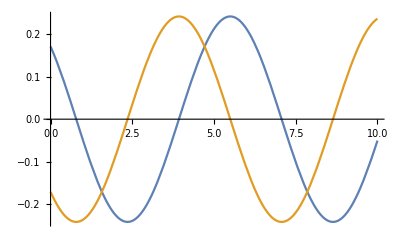

```mathematica
Plot[{Cos[-π/4- t] BesselJ[1,1/2],Sin[-π/4- t] BesselJ[1,1/2]},{t,0,10}]
```

```mathematica
dot[p[1],S[0],S[0],p[1]]
```

```mathematica
(v.e v.e) cosh[L[Y[ν],Subscript[D, a] Y[μ1]]L[Y[ν],Subscript[D, b] Y[μ2]] Subscript[γ, a,b] k[μ1]k[μ2]]+(v.e k.S.e) sinch[L[Y[ν],Subscript[D, a] Y[μ1]]L[Y[ν],Subscript[D, b] Y[μ2]] Subscript[γ, a,b] k[μ1]k[μ2]]
```

```mathematica
c[1](v.e v.e)L[Y[ν],Subscript[D, a] Y[μ1]]L[Y[ν],Subscript[D, b] Y[μ2]] Subscript[γ, a,b] k[μ1]k[μ2] L[Y[ν],Subscript[D, a] Y[μ1]]L[Y[ν],Subscript[D, b] Y[μ2]] Subscript[γ, a,b] k[μ1]k[μ2]
```

```mathematica
dot[p[1],S[0],S[0],p[1]]//expandFS;
%/. dot[p[0],p[1]]->0/.dot[a[0],p[0]]->0/.dot[p[1],p[1]]->0/.dot[p[0],p[0]]->1
```

-dot[a[0],p[1]]^2

```mathematica
k.S.S.k
```

```mathematica
DSolve[r^2 D[D[X[r],r],r]+r D[X[r],r]+Exp[X[r]X[r]]X[r]==0,X[r],r]
```

{Solve[Log[r]+1/(√(-ⅇ^(K[2]^2)+2 C[1]))K[2]1X[r]==C[2],X[r]],Solve[Log[r]+-1/(√(-ⅇ^(K[3]^2)+2 C[1]))K[3]1X[r]==C[2],X[r]]}

```mathematica
Element[n,Integers]
```

n∈ℤ

```mathematica
Assuming[Element[n,Integers],DSolve[r^2 D[D[X[r],r],r]+r D[X[r],r]- 3^2 X[r]==0,X[r],r]//Simplify]
```

{{X[r]→(C[1]+r^6 C[2])/r^3}}

```mathematica
sola=DSolve[r^2 D[D[X[r],r],r]+r D[X[r],r]-r^2(- w^2+e[1])X[r]- 4^2 X[r]==0,X[r],r]
```

{{X[r]→BesselJ[4,ⅈ r √(-w^2+e[1])] C[1]+BesselY[4,-ⅈ r √(-w^2+e[1])] C[2]}}

```mathematica
ta=Assuming[eps>0,X[r]/.sola/.C[2]->0/.f->w^2+eps^2//Simplify]
```

{BesselJ[4,ⅈ eps r] C[1]}

```mathematica
Series[ta,{eps,0,4}]
```

{1/384 r^4 C[1] eps^4+O[eps]^5}

```mathematica
solX=α[n] r^n Exp[I n ϕ]Exp[I e[n,1] t]+αbar[n] r^n Exp[-I n ϕ]Exp[I e[n,2] t]
```

ⅇ^(ⅈ n ϕ+ⅈ t e[n,1]) r^n α[n]+ⅇ^(-ⅈ n ϕ+ⅈ t e[n,2]) r^n αbar[n]

```mathematica
D[solX,t]solX/.e[n,2]->-e[n,1]//Expand
```

ⅈ ⅇ^(2 ⅈ n ϕ+2 ⅈ t e[n,1]) r^(2 n) e[n,1] α[n]^2-ⅈ ⅇ^(-2 ⅈ n ϕ-2 ⅈ t e[n,1]) r^(2 n) e[n,1] αbar[n]^2

# Solution of EOM

## Bulk EOM

```mathematica
ClearAll[EOMOp]
EOMOp[fun_]:=r D[fun,{t,2}]-r D[fun,{r,2}]-D[fun,r]-1/r D[fun,{θ,2}]+r χ fun
```

```mathematica
Sum[c[m,id]Sin[Sqrt[χ]t+m θ]Subscript[f, m][r]+d[m,id]Cos[Sqrt[χ]t+m θ]Subscript[f, m][r],{m,1,10}]
```

c[1] Sin[θ+t √χ] f_1[r]+c[2] Sin[2 θ+t √χ] f_2[r]+c[3] Sin[3 θ+t √χ] f_3[r]+c[4] Sin[4 θ+t √χ] f_4[r]+c[5] Sin[5 θ+t √χ] f_5[r]+c[6] Sin[6 θ+t √χ] f_6[r]+c[7] Sin[7 θ+t √χ] f_7[r]+c[8] Sin[8 θ+t √χ] f_8[r]+c[9] Sin[9 θ+t √χ] f_9[r]+c[10] Sin[10 θ+t √χ] f_10[r]

```mathematica
DSolve[EOMOp[Sin[Sqrt[χ]t+0 θ]f[r]]==0,f[r],r]
DSolve[EOMOp[Sin[Sqrt[χ]t+2θ]f[r]]==0,f[r],r]
```

{{f[r]→C[2]+C[1] Log[r]}}

{{f[r]→C[1]/r^2+r^2 C[2]}}

```mathematica
Y Y Y
```

```mathematica
DSolve[EOMOp[Sin[2/a t+2θ]f[r]]==0/.χ->4/a^2,f[r],r]
```

{{f[r]→C[1]/r^2+r^2 C[2]}}

```mathematica
ClearAll[Ysol,Ysol0]
Ysol[m_,id_]:= β[c,m,id] Cos[m/a t+m θ] r^m/a^(m-1)+ β[s,m,id] Sin[m/a t+m θ] r^m/a^(m-1)
Ysol0[m_,id_]:= β[c,m,id] Cos[1/a t+m θ] r^m/a^(m-1)+ β[s,m,id] Sin[1/a t+m θ] r^m/a^(m-1)
```

```mathematica
ta=Integrate[Cos[f[1]/a t+ θ]Cos[f[2]/a t+ θ]Cos[f[3]/a t+ θ]Cos[f[4]/a t+ θ]Cos[f[5]/a t+ θ]Cos[f[6]/a t+ θ],{θ,0,2π}]
```

1/16 π (Cos[(t (f[1]+f[2]+f[3]-f[4]-f[5]-f[6]))/a]+Cos[(t (f[1]+f[2]-f[3]+f[4]-f[5]-f[6]))/a]+Cos[(t (f[1]-f[2]+f[3]+f[4]-f[5]-f[6]))/a]+Cos[(t (f[1]+f[2]-f[3]-f[4]+f[5]-f[6]))/a]+Cos[(t (f[1]-f[2]+f[3]-f[4]+f[5]-f[6]))/a]+Cos[(t (f[1]-f[2]-f[3]+f[4]+f[5]-f[6]))/a]+Cos[(t (f[1]+f[2]-f[3]-f[4]-f[5]+f[6]))/a]+Cos[(t (f[1]-f[2]+f[3]-f[4]-f[5]+f[6]))/a]+Cos[(t (f[1]-f[2]-f[3]+f[4]-f[5]+f[6]))/a]+Cos[(t (f[1]-f[2]-f[3]-f[4]+f[5]+f[6]))/a])

```mathematica
(ta/.Cos->G//CasesG)/.G[f__]:>(0==f/.a->1/.t->1)//Solve
```

{{f[2]→f[1],f[3]→f[1],f[4]→f[1],f[5]→f[1],f[6]→f[1]}}

```mathematica
Integrate[r D[Ysol[μ],t]Ysol[ν]/.m->2//Expand,{r,0,a},{θ,0,2π}]
```

1/3 a^4 π (β[c,1,ν] β[s,1,μ]-β[c,1,μ] β[s,1,ν])

```mathematica
ta0=Integrate[r Ysol[ν[1]]Ysol[ν[2]]/.m->1//Expand,{θ,0,2π}]//Expand;
ta0/.β[f__,ν[i_]]:>dot[β[f],k]//Simplify
```

π r^3 (dot[k,β[c,1]]^2+dot[k,β[s,1]]^2)

```mathematica
ampOdd=Integrate[r D[(Ysol[1,ν[1]]+1/Sqrt[3] Ysol[3,ν[1]]),t](Ysol[1,ν[2]]+1/Sqrt[3] Ysol[3,ν[2]])(Ysol[1,ν[3]]+1/Sqrt[3] Ysol[3,ν[3]])(Ysol[1,ν[4]]+1/Sqrt[3] Ysol[3,ν[4]])//Expand,{θ,0,2π}]//Expand;
ampOdd/.β[f__,ν[1]]:>dot[β[f],ε]/.β[f__,ν[i_]]:>dot[β[f],k]/;i>1//Simplify
```

1/(4 a^9)π r^5 (-3 a^8 dot[k,β[s,1]]^3 dot[ε,β[c,1]]+√3 a^6 r^2 dot[k,β[s,1]]^2 dot[k,β[s,3]] dot[ε,β[c,1]]-2 a^4 r^4 dot[k,β[s,1]] dot[k,β[s,3]]^2 dot[ε,β[c,1]]+√3 a^6 r^2 dot[k,β[s,1]]^3 dot[ε,β[c,3]]-6 a^4 r^4 dot[k,β[s,1]]^2 dot[k,β[s,3]] dot[ε,β[c,3]]-r^8 dot[k,β[s,3]]^3 dot[ε,β[c,3]]-dot[k,β[c,3]]^2 (2 a^4 r^4 dot[k,β[s,1]] dot[ε,β[c,1]]+r^8 dot[k,β[s,3]] dot[ε,β[c,3]])+r^8 dot[k,β[c,3]]^3 dot[ε,β[s,3]]+dot[k,β[c,1]]^3 (3 a^8 dot[ε,β[s,1]]+√3 a^6 r^2 dot[ε,β[s,3]])+a^4 dot[k,β[c,1]] (2 √3 a^2 r^2 dot[k,β[c,3]] dot[k,β[s,1]] dot[ε,β[c,1]]+2 r^4 dot[k,β[c,3]]^2 dot[ε,β[s,1]]+2 √3 a^2 r^2 dot[k,β[s,1]] dot[k,β[s,3]] dot[ε,β[s,1]]+2 r^4 dot[k,β[s,3]]^2 dot[ε,β[s,1]]+3 dot[k,β[s,1]]^2 (a^4 dot[ε,β[s,1]]-√3 a^2 r^2 dot[ε,β[s,3]]))+dot[k,β[c,3]] (r^8 dot[k,β[s,3]]^2 dot[ε,β[s,3]]+dot[k,β[s,1]]^2 (-√3 a^6 r^2 dot[ε,β[s,1]]+6 a^4 r^4 dot[ε,β[s,3]]))-a^4 dot[k,β[c,1]]^2 (3 dot[k,β[s,1]] (a^4 dot[ε,β[c,1]]+√3 a^2 r^2 dot[ε,β[c,3]])+r^2 (dot[k,β[s,3]] (√3 a^2 dot[ε,β[c,1]]+6 r^2 dot[ε,β[c,3]])-dot[k,β[c,3]] (√3 a^2 dot[ε,β[s,1]]+6 r^2 dot[ε,β[s,3]]))))

```mathematica
ta=ampOdd/.β[f__,ν[1]]:>dot[β[f],ε]/.β[f__,ν[i_]]:>dot[β[f],k]/;i>1/.{β[s,3]->c1 β[c,1],β[c,3]->c1 β[s,1]}//Simplify
```

-1/(4 a^9)π r^5 (-3 a^8+4 a^4 c1^2 r^4+c1^4 r^8) (dot[k,β[c,1]]^2+dot[k,β[s,1]]^2) (-dot[k,β[s,1]] dot[ε,β[c,1]]+dot[k,β[c,1]] dot[ε,β[s,1]])

```mathematica
Integrate[ta,{r,0,a}]//Simplify
```

-1/280 a^5 (-35+28 c1^2+5 c1^4) π (dot[k,β[c,1]]^2+dot[k,β[s,1]]^2) (-dot[k,β[s,1]] dot[ε,β[c,1]]+dot[k,β[c,1]] dot[ε,β[s,1]])

```mathematica
Integrate[ta,{r,0,a}]//Simplify
```

1/280 a^5 π ((35+168 c1^2+45 c1^4) dot[k,β[c,1]]^2+105 c1 dot[k,β[c,1]] dot[k,β[s,1]]+(35+168 c1^2+45 c1^4) dot[k,β[s,1]]^2) (-dot[k,β[s,1]] dot[ε,β[c,1]]+dot[k,β[c,1]] dot[ε,β[s,1]])

```mathematica
Solve[(35+168 c1^2+45 c1^4)==105/2 c1,c1]
```

{{c1→Root-0.170-1.90 ⅈRoot[70-105 #1+336 #1^2+90 #1^4&,1]-0.17047931333960517},{c1→Root-0.170+1.90 ⅈRoot[70-105 #1+336 #1^2+90 #1^4&,2]-0.17047931333960517},{c1→Root0.170-0.430 ⅈRoot[70-105 #1+336 #1^2+90 #1^4&,3]0.17047931333960517},{c1→Root0.170+0.430 ⅈRoot[70-105 #1+336 #1^2+90 #1^4&,4]0.17047931333960517}}

```mathematica
Ysol[3,ν[4]]
```

(r^3 Cos[t/a+3 θ] β[c,3,ν[4]])/a^2+(r^3 Sin[t/a+3 θ] β[s,3,ν[4]])/a^2

```mathematica
Ysol[1,ν[1]]Ysol[1,ν[2]]Ysol[1,ν[3]]Ysol[3,ν[4]]
```

(r Cos[t/a+θ] β[c,1,ν[1]]+r Sin[t/a+θ] β[s,1,ν[1]]) (r Cos[t/a+θ] β[c,1,ν[2]]+r Sin[t/a+θ] β[s,1,ν[2]]) (r Cos[t/a+θ] β[c,1,ν[3]]+r Sin[t/a+θ] β[s,1,ν[3]]) ((r^3 Cos[t/a+3 θ] β[c,3,ν[4]])/a^2+(r^3 Sin[t/a+3 θ] β[s,3,ν[4]])/a^2)

```mathematica
ampEven=Integrate[r( Ysol[1,ν[1]])( Ysol[1,ν[2]])( Ysol[1,ν[3]])( Ysol[1,ν[4]])//Expand,{θ,0,2π}]//Expand;
```

```mathematica
ampEven/.β[f__,ν[i_]]:>dot[β[f],k]//Simplify
```

3/4 π r^5 (dot[k,β[c,1]]^2+dot[k,β[s,1]]^2)^2

```mathematica
ampEven=Integrate[r( Ysol[1,ν[1]]+1/Sqrt[3] Ysol[3,ν[1]])( Ysol[1,ν[2]]+1/Sqrt[3] Ysol[3,ν[2]])( Ysol[1,ν[3]]+ 1/Sqrt[3] Ysol[3,ν[3]])( Ysol[1,ν[4]]+1/Sqrt[3] Ysol[3,ν[4]])//Expand,{θ,0,2π}]//Expand;
```

```mathematica
ampEven/.β[f__,ν[i_]]:>dot[β[f],k]/.{β[c,3]-> c1 β[s,1],β[s,3]->c1  β[c,1]}//Simplify
```

1/(12 a^8)π r^5 ((9 a^8+12 a^4 c1^2 r^4+c1^4 r^8) dot[k,β[c,1]]^4+16 √3 a^6 c1 r^2 dot[k,β[c,1]]^3 dot[k,β[s,1]]+2 (9 a^8+12 a^4 c1^2 r^4+c1^4 r^8) dot[k,β[c,1]]^2 dot[k,β[s,1]]^2-16 √3 a^6 c1 r^2 dot[k,β[c,1]] dot[k,β[s,1]]^3+(9 a^8+12 a^4 c1^2 r^4+c1^4 r^8) dot[k,β[s,1]]^4)

```mathematica
Integrate[1/(100 a^16)3 π r^5 (25 a^16+20 a^8 c1^2 r^8+c1^4 r^16) (dot[k,β[c,1]]^2+dot[k,β[s,1]]^2)^2,{r,0,a}]//Simplify
```

(a^6 (1925+660 c1^2+21 c1^4) π (dot[k,β[c,1]]^2+dot[k,β[s,1]]^2)^2)/15400

```mathematica
Solve[(105+35 √3 c1+84 c1^2+5 c1^4)==(105-105 √3 c1+84 c1^2+5 c1^4) ,c1]
```

{{c1→0}}

```mathematica
1/a^2 π r^7 (dot[k,β[c,1]]^3 dot[k,β[c,3]]-3 dot[k,β[c,1]] dot[k,β[c,3]] dot[k,β[s,1]]^2+3 dot[k,β[c,1]]^2 dot[k,β[s,1]] dot[k,β[s,3]]-dot[k,β[s,1]]^3 dot[k,β[s,3]])/.β[c,3]->- Sqrt[3]β[s,1]/.β[s,3]->1/Sqrt[3] β[c,1]//Simplify
```

(8 π r^7 dot[k,β[c,1]] dot[k,β[s,1]]^3)/(√3 a^2)

## Boundary EOM

```mathematica
Action=a (D[B[t,θ],t]D[B[t,θ],t]-1/a^2 D[B[t,θ],θ]D[B[t,θ],θ]) dθ dt
```

a dt dθ (-(χ B[t,θ]^2)/a^2-((B^(0,1)[t,θ])^2)/a^2+(B^(1,0)[t,θ])^2)

```mathematica
ClearAll[EOMBDOp]
EOMBDOp[fun_]:= D[fun,{t,2}]-1/a^2 D[fun,{θ,2}]
```

```mathematica
ClearAll[Bsol]
Bsol[id_]=a β[c,1,id] Cos[c1/a t+c2 θ]+a  β[s,1,id] Sin[c1/a t+c2 θ]/.Solve[(c1^2-c2^2)==0,c2][[2]]
```

a Cos[(c1 t)/a+c1 θ] β[c,1,id]+a Sin[(c1 t)/a+c1 θ] β[s,1,id]

```mathematica
Integrate[a D[Bsol[μ],t]D[Bsol[ν],t]-a/a^2 D[Bsol[μ],θ]D[Bsol[ν],θ]-χ/a^2 a Bsol[μ]Bsol[ν]//Expand,{θ,0,2π}]//Simplify
```

0

```mathematica
Integrate[a D[Bsol[μ],t]Bsol[ν]/.m->2//Expand,{θ,0,2π}]
```

a^2 π √(1+χ) (β[c,1,ν] β[s,1,μ]-β[c,1,μ] β[s,1,ν])

```mathematica
res=Integrate[a D[Bsol[μ],t]D[Bsol[ν],t]-t1 a/a^2 D[Bsol[μ],θ]D[Bsol[ν],θ]-t2 χ/a^2 a Bsol[μ]Bsol[ν]//Expand,{θ,0,2π}]//Simplify
```

-a π (-1+t1+(-1+t2) χ) (β[c,1,μ] β[c,1,ν]+β[s,1,μ] β[s,1,ν])

```mathematica
res/.t1->0/.t2->0
```

-a π (-1-χ) (β[c,1,μ] β[c,1,ν]+β[s,1,μ] β[s,1,ν])

```mathematica
Coefficient[res,t1]
```

-a π (β[c,1,μ] β[c,1,ν]+β[s,1,μ] β[s,1,ν])

```mathematica
Coefficient[res,t2]
```

-a π χ (β[c,1,μ] β[c,1,ν]+β[s,1,μ] β[s,1,ν])

```mathematica
(D[Bsol[μ[1]],t]D[Bsol[μ[2]],t]-1/a^2 D[Bsol[μ[1]],θ]D[Bsol[μ[2]],θ])//Simplify
```

0

## EOM for S2

```mathematica
ActionS2= (D[Y[t,θ,ϕ],t]D[Y[t,θ,ϕ],t]-1/a^2 D[Y[t,θ,ϕ],θ]D[Y[t,θ,ϕ],θ]-1/(a^2 Sin[θ]^2)D[Y[t,θ,ϕ],ϕ]D[Y[t,θ,ϕ],ϕ]) a Sin[θ]dt dθ dϕ
```

a dt dθ dϕ Sin[θ] (-(Csc[θ]^2 (Y^(0,0,1)[t,θ,ϕ])^2)/a^2-((Y^(0,1,0)[t,θ,ϕ])^2)/a^2+(Y^(1,0,0)[t,θ,ϕ])^2)

```mathematica
ActionS2//Expand
```

-(dt dθ dϕ Csc[θ] (Y^(0,0,1)[t,θ,ϕ])^2)/R-(dt dθ dϕ Sin[θ] (Y^(0,1,0)[t,θ,ϕ])^2)/R+dt dθ dϕ R Sin[θ] (Y^(1,0,0)[t,θ,ϕ])^2

```mathematica
ClearAll[EOMOpS2]
EOMOpS2[fun_]:=-a Sin[θ] D[fun,{t,2}]+ D[ Sin[θ]/a D[fun,θ],θ]+(Csc[θ] D[fun,{ϕ,2}])/a
```

```mathematica
funt=fun[t](SphericalHarmonicY[6,1,θ,ϕ]);
funtest=EOMOpS2[funt]//Simplify;
```

```mathematica
funtest
```

1/(128 R)ⅇ^(ⅈ ϕ) √(273/(2 π)) Cos[θ] (19+12 Cos[2 θ]+33 Cos[4 θ]) Sin[θ]^2 (42 fun[t]+R^2 fun''[t])

```mathematica
funSol=DSolve[funtest==0,fun[t],t]//Simplify
```

{{fun[t]→C[1] Cos[(√2 t)/R]+C[2] Sin[(√2 t)/R]}}

```mathematica
funtSol=funt/.funSol[[1]]//Simplify
```

-1/2 ⅇ^(-ⅈ ϕ) (1+ⅇ^(2 ⅈ ϕ)) √(3/(2 π)) (C[1] Cos[(√2 t)/R]+C[2] Sin[(√2 t)/R]) Sin[θ]

```mathematica
ClearAll[YS2Sol]
YS2Sol[l_,m_,id_]:= (a β[c,l,m,id] Cos[Sqrt[l(l+1)]/a t+m ϕ]LegendreP[l,m,Cos[θ]]+ a β[s,l,m,id] Sin[Sqrt[l(l+1)]/a t+m ϕ]LegendreP[l,m,Cos[θ]])
```

```mathematica
LegendreP[6,2,Cos[θ]]
```

-105/8 (-1+Cos[θ]^2) (1-18 Cos[θ]^2+33 Cos[θ]^4)

```mathematica
Assuming[(n1|n2)∈Integers&&n1>0&&n2>0, Integrate[Cos[x]^n1 Sin[x]^n2,{x,0,2π}]]
```

((1+(-1)^n1) (1+(-1)^(n1+n2)) Gamma[(1+n1)/2] Gamma[(1+n2)/2])/(2 Gamma[1/2 (2+n1+n2)])

```mathematica
Integrate[Cos[x]^4 Sin[x]^4,{x,0,2π}]
```

(3 π)/64

### Check dY dY G(Z) terms

```mathematica
ClearAll[YSol]
YSol[id_]:=YS2Sol[1,1,id]
```

```mathematica
actionY0=(D[YSol[μ[1]],t]D[YSol[μ[2]],t]-1/a^2 D[YSol[μ[1]],θ]D[YSol[μ[2]],θ]-1/(a^2 Sin[θ]^2)D[YSol[μ[1]],ϕ]D[YSol[μ[2]],ϕ]) a Sin[θ]//Simplify;
```

```mathematica
ta=actionY0 /.β[f__,μ[1]]:>dot[β[f],ε]/.β[f__,μ[2]]:>dot[β[f],ε]/.β[f__,μ[i_]]:>dot[β[f],k]/;i>1//Expand//Simplify
Integrate[%//Expand,{ϕ,0,2π}];
Integrate[%,{θ,0,π}]
```

-1/8 a Sin[θ] ((2+6 Cos[2 θ]+2 Cos[2 ((√2 t)/a+ϕ)]-Cos[2 ((√2 t)/a-θ+ϕ)]-Cos[2 ((√2 t)/a+θ+ϕ)]) dot[ε,β[c,1,1]]^2+(2+6 Cos[2 θ]-2 Cos[2 ((√2 t)/a+ϕ)]+Cos[2 ((√2 t)/a-θ+ϕ)]+Cos[2 ((√2 t)/a+θ+ϕ)]) dot[ε,β[s,1,1]]^2+8 dot[ε,β[c,1,1]] dot[ε,β[s,1,1]] Sin[θ]^2 Sin[2 ((√2 t)/a+ϕ)])

0

```mathematica
ta/.θ->π/3/.ϕ->π/3/.a->1//FullSimplify
```

1/32 √3 (-12 Cos[π/6+2 √2 t] dot[ε,β[c,1,1]] dot[ε,β[s,1,1]]+dot[ε,β[s,1,1]]^2 (2-3 Cos[2 √2 t]-3 √3 Sin[2 √2 t])+dot[ε,β[c,1,1]]^2 (2+3 Cos[2 √2 t]+3 √3 Sin[2 √2 t]))

```mathematica
actionY2=actionY0 YSol[μ[3]] YSol[μ[4]]/.β[f__,μ[1]]:>dot[β[f],ε]/.β[f__,μ[2]]:>dot[β[f],ε]/.β[f__,μ[i_]]:>dot[β[f],k]/;i>1//Expand;
Integrate[actionY2//Expand,{ϕ,0,2π}];
Integrate[%,{θ,0,π}]
```

8/15 a^3 π (dot[k,β[s,1,1]] dot[ε,β[c,1,1]]-dot[k,β[c,1,1]] dot[ε,β[s,1,1]])^2

```mathematica
actionY4=actionY0 YSol[μ[3]] YSol[μ[4]]YSol[μ[5]]YSol[μ[6]]/.β[f__,μ[1]]:>dot[β[f],ε]/.β[f__,μ[2]]:>dot[β[f],ε]/.β[f__,μ[i_]]:>dot[β[f],k]/;i>1//Expand;
Integrate[actionY4//Expand,{ϕ,0,2π}];
Integrate[%,{θ,0,π}]
```

1/(35 a^2)16 π R (dot[k,β[c,1,1]]^2+dot[k,β[s,1,1]]^2) (dot[k,β[s,1,1]] dot[ε,β[c,1,1]]-dot[k,β[c,1,1]] dot[ε,β[s,1,1]])^2

```mathematica
dot[k,S[0],ε]^2//expandFS;
%/.dot[k,k]->0/.dot[k,p[0]]->0/.dot[k,ε]->0/.dot[ε,ε]->0
```

-dot[k,a[0]]^2 dot[ε,p[0]]^2

```mathematica
actionY6=actionY0 YSol[μ[3]] YSol[μ[4]]YSol[μ[5]]YSol[μ[6]]YSol[μ[7]]YSol[μ[8]]/.β[f__,μ[1]]:>dot[β[f],ε]/.β[f__,μ[2]]:>dot[β[f],ε]/.β[f__,μ[i_]]:>dot[β[f],k]/;i>1//Expand;
```

```mathematica
ta=List@@actionY6/.a->1/.a_ b_:>b/;NumericQ[a]/.dot[f__]:>1//Union;
```

```mathematica
ta[[12]]
```

```mathematica
Timing[Cos[θ]^6 Cos[ϕ]^6 Cos[2 ϕ] Sin[θ]//Integrate[#,{ϕ,0,2π}]&]
```

{0.024873,15/32 π Cos[θ]^6 Sin[θ]}

```mathematica
Timing[ta[[12]]//Integrate[#,{ϕ,0,2π}]&]
```

{0.112635,15/32 π Cos[θ]^6 Sin[θ]}

```mathematica
Integrate[actionY6,{ϕ,0,2π}];
Integrate[%,{θ,0,π}]
```

### Check dX dX G(Z) terms

```mathematica
ampEven=Integrate[a Sin[θ]( YSol[ν[1]])( YSol[ν[2]])( YSol[ν[3]])( YSol[ν[4]])//Expand,{ϕ,0,2π}]//Expand;
ampEven=ampEven/.β[f__,ν[i_]]:>dot[β[f],k];
```

```mathematica
ampEven2=ampEven//Expand//Integrate[#,{θ,0,π}]&
```

```mathematica
ampOdd=Integrate[r D[Ysol[ν[1]],t]Ysol[ν[2]]Ysol[ν[3]]Ysol[ν[4]]/.m->1//Expand,{θ,0,2π}]//Expand;
ampOdd/.β[f__,ν[1]]:>dot[β[f],ε]/.β[f__,ν[i_]]:>dot[β[f],k]/;i>1//Simplify
```

1/(4 a)3 π r^5 (dot[k,β[c,1]]^2+dot[k,β[s,1]]^2) (-dot[k,β[s,1]] dot[ε,β[c,1]]+dot[k,β[c,1]] dot[ε,β[s,1]])

```mathematica
ampEven=Integrate[r Ysol[ν[1]]Ysol[ν[2]]Ysol[ν[3]]Ysol[ν[4]]/.m->1//Expand,{θ,0,2π}]//Expand;
ampEven/.β[f__,ν[i_]]:>dot[β[f],k]//Simplify
```

3/4 π r^5 (dot[k,β[c,1]]^2+dot[k,β[s,1]]^2)^2

## EOM for S2 elliptic

```mathematica
ActionS2= (D[Y[t,θ,ϕ],t]D[Y[t,θ,ϕ],t]-1/(a^2 Cos[θ]^2+c^2 Sin[θ]^2)D[Y[t,θ,ϕ],θ]D[Y[t,θ,ϕ],θ]-1/(a^2 Sin[θ]^2)D[Y[t,θ,ϕ],ϕ]D[Y[t,θ,ϕ],ϕ]) Sqrt[a^2 Cos[θ]^2+c^2 Sin[θ]^2]a Sin[θ]dt dθ dϕ
```

a dt dθ dϕ Sin[θ] √(a^2 Cos[θ]^2+c^2 Sin[θ]^2) (-(Csc[θ]^2 (Y^(0,0,1)[t,θ,ϕ])^2)/a^2-((Y^(0,1,0)[t,θ,ϕ])^2)/(a^2 Cos[θ]^2+c^2 Sin[θ]^2)+(Y^(1,0,0)[t,θ,ϕ])^2)

```mathematica
ActionS2//Expand
```

-(dt dθ dϕ Csc[θ] (Y^(0,0,1)[t,θ,ϕ])^2)/R-(dt dθ dϕ Sin[θ] (Y^(0,1,0)[t,θ,ϕ])^2)/R+dt dθ dϕ R Sin[θ] (Y^(1,0,0)[t,θ,ϕ])^2

```mathematica
ClearAll[EOMOpS2]
EOMOpS2[fun_]:=-Sqrt[a^2 Cos[θ]^2+c^2 Sin[θ]^2]a Sin[θ] D[fun,{t,2}]+ D[ (Sqrt[a^2 Cos[θ]^2+c^2 Sin[θ]^2]a Sin[θ])/(a^2 Cos[θ]^2+c^2 Sin[θ]^2) D[fun,θ],θ]+(Sqrt[a^2 Cos[θ]^2+c^2 Sin[θ]^2]a Sin[θ] D[fun,{ϕ,2}])/(a^2 Sin[θ]^2)
```

```mathematica
funt=fun[θ](Cos[t/a+ϕ]);
funtest=EOMOpS2[funt]//Simplify;
```

```mathematica
funtest
```

(Cos[t/a+ϕ] Sin[θ] (-1/4 (a^2+c^2+(a^2-c^2) Cos[2 θ])^2 Cot[θ]^2 Csc[θ]^2 fun[θ]+a^4 Cot[θ] Csc[θ]^2 fun'[θ]+a^2 (c^2+a^2 Cot[θ]^2) fun''[θ]))/(a (c^2+a^2 Cot[θ]^2) √(a^2 Cos[θ]^2+c^2 Sin[θ]^2))

```mathematica
funtest2=Series[(-1/4 (a^2+c^2+(a^2-c^2) Cos[2 θ])^2 Cot[θ]^2 Csc[θ]^2 fun[θ]+a^4 Cot[θ] Csc[θ]^2 fun'[θ]+a^2 (c^2+a^2 Cot[θ]^2) fun''[θ]),{c,0,2}]//Normal
```

-1/4 (a^2+a^2 Cos[2 θ])^2 Cot[θ]^2 Csc[θ]^2 fun[θ]+a^4 Cot[θ] Csc[θ]^2 fun'[θ]+a^4 Cot[θ]^2 fun''[θ]+c^2 (1/2 (-1+Cos[2 θ]) (a^2+a^2 Cos[2 θ]) Cot[θ]^2 Csc[θ]^2 fun[θ]+a^2 fun''[θ])

```mathematica
funSol=DSolve[funtest2==0,fun[θ],θ]
```

DSolve[-1/4 (a^2+a^2 Cos[2 θ])^2 Cot[θ]^2 Csc[θ]^2 fun[θ]+a^4 Cot[θ] Csc[θ]^2 fun'[θ]+a^4 Cot[θ]^2 fun''[θ]+c^2 (1/2 (-1+Cos[2 θ]) (a^2+a^2 Cos[2 θ]) Cot[θ]^2 Csc[θ]^2 fun[θ]+a^2 fun''[θ])==0,fun[θ],θ]

```mathematica
funtSol=funt/.funSol[[1]]//Simplify
```

-1/2 ⅇ^(-ⅈ ϕ) (1+ⅇ^(2 ⅈ ϕ)) √(3/(2 π)) (C[1] Cos[(√2 t)/R]+C[2] Sin[(√2 t)/R]) Sin[θ]

```mathematica
ClearAll[YS2Sol]
YS2Sol[l_,m_,id_]:= (β[c,l,m,id] Cos[Sqrt[l(l+1)]/a t+m ϕ]LegendreP[l,m,Cos[θ]]+ β[s,l,m,id] Sin[Sqrt[l(l+1)]/a t+m ϕ]LegendreP[l,m,Cos[θ]])
```

```mathematica
LegendreP[7,1,Cos[θ]]//FullSimplify
```

-7/16 (-5+135 Cos[θ]^2-495 Cos[θ]^4+429 Cos[θ]^6) √(Sin[θ]^2)

### Check dY dY G(Z) terms

```mathematica
ClearAll[YSol]
YSol[id_]:=YS2Sol[1,1,id]
```

```mathematica
actionY0=(D[YSol[μ[1]],t]D[YSol[μ[2]],t]-1/a^2 D[YSol[μ[1]],θ]D[YSol[μ[2]],θ]-1/(a^2 Sin[θ]^2)D[YSol[μ[1]],ϕ]D[YSol[μ[2]],ϕ]) a Sin[θ]//Simplify;
```

```mathematica
actionY0 /.β[f__,μ[1]]:>dot[β[f],ε]/.β[f__,μ[2]]:>dot[β[f],ε]/.β[f__,μ[i_]]:>dot[β[f],k]/;i>1//Expand;
Integrate[%//Expand,{ϕ,0,2π}];
Integrate[%,{θ,0,π}]
```

0

```mathematica
actionY2=actionY0 YSol[μ[3]] YSol[μ[4]]/.β[f__,μ[1]]:>dot[β[f],ε]/.β[f__,μ[2]]:>dot[β[f],ε]/.β[f__,μ[i_]]:>dot[β[f],k]/;i>1//Expand;
Integrate[actionY2//Expand,{ϕ,0,2π}];
Integrate[%,{θ,0,π}]
```

1/(15 a^2)8 π R (dot[k,β[s,1,1]] dot[ε,β[c,1,1]]-dot[k,β[c,1,1]] dot[ε,β[s,1,1]])^2

```mathematica
actionY4=actionY0 YSol[μ[3]] YSol[μ[4]]YSol[μ[5]]YSol[μ[6]]/.β[f__,μ[1]]:>dot[β[f],ε]/.β[f__,μ[2]]:>dot[β[f],ε]/.β[f__,μ[i_]]:>dot[β[f],k]/;i>1//Expand;
Integrate[actionY4//Expand,{ϕ,0,2π}];
Integrate[%,{θ,0,π}]
```

1/(35 a^2)16 π R (dot[k,β[c,1,1]]^2+dot[k,β[s,1,1]]^2) (dot[k,β[s,1,1]] dot[ε,β[c,1,1]]-dot[k,β[c,1,1]] dot[ε,β[s,1,1]])^2

### Check dX dX G(Z) terms

```mathematica
ampEven=Integrate[a Sin[θ]( YSol[ν[1]])( YSol[ν[2]])( YSol[ν[3]])( YSol[ν[4]])//Expand,{ϕ,0,2π}]//Expand;
ampEven=ampEven/.β[f__,ν[i_]]:>dot[β[f],k];
```

```mathematica
ampEven2=ampEven//Expand//Integrate[#,{θ,0,π}]&
```

```mathematica
ampOdd=Integrate[r D[Ysol[ν[1]],t]Ysol[ν[2]]Ysol[ν[3]]Ysol[ν[4]]/.m->1//Expand,{θ,0,2π}]//Expand;
ampOdd/.β[f__,ν[1]]:>dot[β[f],ε]/.β[f__,ν[i_]]:>dot[β[f],k]/;i>1//Simplify
```

1/(4 a)3 π r^5 (dot[k,β[c,1]]^2+dot[k,β[s,1]]^2) (-dot[k,β[s,1]] dot[ε,β[c,1]]+dot[k,β[c,1]] dot[ε,β[s,1]])

```mathematica
ampEven=Integrate[r Ysol[ν[1]]Ysol[ν[2]]Ysol[ν[3]]Ysol[ν[4]]/.m->1//Expand,{θ,0,2π}]//Expand;
ampEven/.β[f__,ν[i_]]:>dot[β[f],k]//Simplify
```

3/4 π r^5 (dot[k,β[c,1]]^2+dot[k,β[s,1]]^2)^2

## EOM for conformal flat space

```mathematica
ActionCF= (D[Y[t,ρ,ϕ],t]D[Y[t,ρ,ϕ],t]-1/f[ρ/a] D[Y[t,ρ,ϕ],ρ]D[Y[t,ρ,ϕ],ρ]-1/f[ρ/a] 1/ρ^2 D[Y[t,ρ,ϕ],ϕ]D[Y[t,ρ,ϕ],ϕ]) f[ρ/a]ρ dt dρ dϕ
```

dt dρ dϕ ρ f[ρ/a] (-((Y^(0,0,1)[t,ρ,ϕ])^2)/(ρ^2 f[ρ/a])-((Y^(0,1,0)[t,ρ,ϕ])^2)/f[ρ/a]+(Y^(1,0,0)[t,ρ,ϕ])^2)

```mathematica
ActionS2//Expand
```

-(dt dθ dϕ Csc[θ] (Y^(0,0,1)[t,θ,ϕ])^2)/R-(dt dθ dϕ Sin[θ] (Y^(0,1,0)[t,θ,ϕ])^2)/R+dt dθ dϕ R Sin[θ] (Y^(1,0,0)[t,θ,ϕ])^2

```mathematica
ClearAll[EOMOpCF]
EOMOpCF[fr_]:=-f[ρ/a]ρ D[fr,{t,2}]+ D[ ρ D[fr,ρ],ρ]+1/ρ D[fr,{ϕ,2}]
```

```mathematica
funt=fun[ρ]Cos[1/a t+ϕ];
funtest=EOMOpCF[funt]/.f[ρ/a]->(ρ/a)^2//Simplify;
```

```mathematica
funtest
```

(Cos[t/a+ϕ] ((-a^4+ρ^4) fun[ρ]+a^4 ρ (fun'[ρ]+ρ fun''[ρ])))/(a^4 ρ)

```mathematica
funSol=DSolve[funtest==0,fun[ρ],ρ]//Simplify
```

{{fun[ρ]→(ⅇ^(-(ⅈ ρ^2)/(2 a^2)) (2 C[1]-ⅈ a^2 ⅇ^((ⅈ ρ^2)/a^2) C[2]))/(2 ρ)}}

```mathematica
funSol/.C[2]->-2/a^2 I C[1]//ExpToTrig//FullSimplify
```

{{fun[ρ]→-(2 ⅈ C[1] Sin[ρ^2/(2 a^2)])/ρ}}

```mathematica
Integrate[Sin[ρ^2/(2 a^2)]/ρ Sin[ρ^2/(2 a^2)]/ρ Sin[ρ^2/(2 a^2)]/ρ Sin[ρ^2/(2 a^2)]/ρ,{ρ,0,a}]
```

-1/(24 a^3)(3-4 Cos[1]+Cos[2]-8 √(2 π) FresnelC[√(2/π)]+8 √π FresnelC[2/(√π)]+8 Sin[1]-4 Sin[2])

```mathematica
funtSol=funt/.funSol[[1]]//Simplify
```

-1/2 ⅇ^(-ⅈ ϕ) (1+ⅇ^(2 ⅈ ϕ)) √(3/(2 π)) (C[1] Cos[(√2 t)/R]+C[2] Sin[(√2 t)/R]) Sin[θ]

```mathematica
ClearAll[YS2Sol]
YS2Sol[l_,m_,id_]:= (β[c,l,m,id] Cos[Sqrt[l(l+1)]/a t+m ϕ]LegendreP[l,m,Cos[θ]]+ β[s,l,m,id] Sin[Sqrt[l(l+1)]/a t+m ϕ]LegendreP[l,m,Cos[θ]])
```

### Check dY dY G(Z) terms

```mathematica
ClearAll[YSol]
YSol[id_]:=YS2Sol[1,1,id]
```

```mathematica
actionY0=(D[YSol[μ[1]],t]D[YSol[μ[2]],t]-1/a^2 D[YSol[μ[1]],θ]D[YSol[μ[2]],θ]-1/(a^2 Sin[θ]^2)D[YSol[μ[1]],ϕ]D[YSol[μ[2]],ϕ]) a Sin[θ]//Simplify;
```

```mathematica
actionY0 /.β[f__,μ[1]]:>dot[β[f],ε]/.β[f__,μ[2]]:>dot[β[f],ε]/.β[f__,μ[i_]]:>dot[β[f],k]/;i>1//Expand;
Integrate[%//Expand,{ϕ,0,2π}];
Integrate[%,{θ,0,π}]
```

0

```mathematica
actionY2=actionY0 YSol[μ[3]] YSol[μ[4]]/.β[f__,μ[1]]:>dot[β[f],ε]/.β[f__,μ[2]]:>dot[β[f],ε]/.β[f__,μ[i_]]:>dot[β[f],k]/;i>1//Expand;
Integrate[actionY2//Expand,{ϕ,0,2π}];
Integrate[%,{θ,0,π}]
```

1/(15 a^2)8 π R (dot[k,β[s,1,1]] dot[ε,β[c,1,1]]-dot[k,β[c,1,1]] dot[ε,β[s,1,1]])^2

```mathematica
actionY4=actionY0 YSol[μ[3]] YSol[μ[4]]YSol[μ[5]]YSol[μ[6]]/.β[f__,μ[1]]:>dot[β[f],ε]/.β[f__,μ[2]]:>dot[β[f],ε]/.β[f__,μ[i_]]:>dot[β[f],k]/;i>1//Expand;
Integrate[actionY4//Expand,{ϕ,0,2π}];
Integrate[%,{θ,0,π}]
```

1/(35 a^2)16 π R (dot[k,β[c,1,1]]^2+dot[k,β[s,1,1]]^2) (dot[k,β[s,1,1]] dot[ε,β[c,1,1]]-dot[k,β[c,1,1]] dot[ε,β[s,1,1]])^2

### Check dX dX G(Z) terms

```mathematica
ampEven=Integrate[a Sin[θ]( YSol[ν[1]])( YSol[ν[2]])( YSol[ν[3]])( YSol[ν[4]])//Expand,{ϕ,0,2π}]//Expand;
ampEven=ampEven/.β[f__,ν[i_]]:>dot[β[f],k];
```

```mathematica
ampEven2=ampEven//Expand//Integrate[#,{θ,0,π}]&
```

```mathematica
ampOdd=Integrate[r D[Ysol[ν[1]],t]Ysol[ν[2]]Ysol[ν[3]]Ysol[ν[4]]/.m->1//Expand,{θ,0,2π}]//Expand;
ampOdd/.β[f__,ν[1]]:>dot[β[f],ε]/.β[f__,ν[i_]]:>dot[β[f],k]/;i>1//Simplify
```

1/(4 a)3 π r^5 (dot[k,β[c,1]]^2+dot[k,β[s,1]]^2) (-dot[k,β[s,1]] dot[ε,β[c,1]]+dot[k,β[c,1]] dot[ε,β[s,1]])

```mathematica
ampEven=Integrate[r Ysol[ν[1]]Ysol[ν[2]]Ysol[ν[3]]Ysol[ν[4]]/.m->1//Expand,{θ,0,2π}]//Expand;
ampEven/.β[f__,ν[i_]]:>dot[β[f],k]//Simplify
```

3/4 π r^5 (dot[k,β[c,1]]^2+dot[k,β[s,1]]^2)^2

# S2*R model

## EOM for S2

```mathematica
ActionS2= (D[Y[t,θ,ϕ],t]D[Y[t,θ,ϕ],t]-1/a^2 D[Y[t,θ,ϕ],θ]D[Y[t,θ,ϕ],θ]-1/(a^2 Sin[θ]^2)D[Y[t,θ,ϕ],ϕ]D[Y[t,θ,ϕ],ϕ]) a^2 Sin[θ]dt dθ dϕ
```

a^2 dt dθ dϕ Sin[θ] (-(Csc[θ]^2 (Y^(0,0,1)[t,θ,ϕ])^2)/a^2-((Y^(0,1,0)[t,θ,ϕ])^2)/a^2+(Y^(1,0,0)[t,θ,ϕ])^2)

```mathematica
ClearAll[EOMOpS2]
EOMOpS2[fun_]:=-a Sin[θ] D[fun,{t,2}]+ D[ Sin[θ]/a D[fun,θ],θ]+(Csc[θ] D[fun,{ϕ,2}])/a
```

```mathematica
ClearAll[YS2Sol,YS2SolSim]
YS2Sol[l_,m_,id_]:=  a Sqrt[Sqrt[l(l+1)]] Sqrt[2l+1]/Sqrt[l(l+1)] Sqrt[((l-m)!!)/((l+m)!!)] 1/Sqrt[Product[l-mm,{mm,-m+1,m-1,2}]](β[c,l,m,id] Cos[Sqrt[l(l+1)]/a t+m ϕ](Assuming[Sin[θ]>0,LegendreP[l,m,Cos[θ]]//Simplify])+ β[s,l,m,id] Sin[Sqrt[l(l+1)]/a t+m ϕ](Assuming[Sin[θ]>0,LegendreP[l,m,Cos[θ]]//Simplify]))
YS2SolSim[l_,m_,id_]:=  a c[l,m](β[c,l,m,id] Cos[Sqrt[l(l+1)]/a t+m ϕ](Assuming[Sin[θ]>0,LegendreP[l,m,Cos[θ]]//Simplify])+ β[s,l,m,id] Sin[Sqrt[l(l+1)]/a t+m ϕ](Assuming[Sin[θ]>0,LegendreP[l,m,Cos[θ]]//Simplify]))
```

### test EOM

```mathematica
funt=fun[t](SphericalHarmonicY[1,1,θ,ϕ]);
funtest=EOMOpS2[funt]//Simplify;
```

```mathematica
funtest
```

(ⅇ^(ⅈ ϕ) √(3/(2 π)) Sin[θ]^2 (2 fun[t]+a^2 fun''[t]))/(2 a)

```mathematica
funSol=DSolve[funtest==0,fun[t],t]//Simplify
```

{{fun[t]→C[1] Cos[(√2 t)/a]+C[2] Sin[(√2 t)/a]}}

```mathematica
funtSol=funt/.funSol[[1]]//Simplify
```

-1/2 ⅇ^(-ⅈ ϕ) (1+ⅇ^(2 ⅈ ϕ)) √(3/(2 π)) (C[1] Cos[(√2 t)/R]+C[2] Sin[(√2 t)/R]) Sin[θ]

### Check dY dY G(Z) terms

```mathematica
actionY0=(D[YSol[μ[1]],t]D[YSol[μ[2]],t]-1/a^2 D[YSol[μ[1]],θ]D[YSol[μ[2]],θ]-1/(a^2 Sin[θ]^2)D[YSol[μ[1]],ϕ]D[YSol[μ[2]],ϕ]) a Sin[θ]//Simplify;
```

```mathematica
ta=actionY0 /.β[f__,μ[1]]:>dot[β[f],ε]/.β[f__,μ[2]]:>dot[β[f],ε]/.β[f__,μ[i_]]:>dot[β[f],k]/;i>1//Expand;
Integrate[%//Expand,{ϕ,0,2π}]
Integrate[%,{θ,0,π}]
```

1/4 a π (dot[ε,β[c,1,1]]^2+dot[ε,β[s,1,1]]^2) (Sin[θ]-3 Sin[3 θ])

0

```mathematica
actionY8=actionY0  Product[YSol[μ[jj]],{jj,3,4}]/.β[f__,μ[1]]:>dot[β[f],ε]/.β[f__,μ[2]]:>dot[β[f],ε]/.β[f__,μ[i_]]:>dot[β[f],k]/;i>1//TrigToExp//Expand;
2π*actionY8/.Power[E,Plus[g___,Times[f_,ϕ]]]:>0//Expand;
%/.Power[E,Times[f_, θ]]:>(Exp[Times[f,π]]-1)/f//Simplify
```

8/15 a^3 π (dot[k,β[s,1,1]] dot[ε,β[c,1,1]]-dot[k,β[c,1,1]] dot[ε,β[s,1,1]])^2

```mathematica
Integrate[actionY6[[332]],{ϕ,0,2π}]
Integrate[%,{θ,0,π}]
```

1/(8192 a)1575 ⅈ ⅇ^(3 ⅈ θ) π dot[k,β[c,1,1]]^2 dot[k,β[s,1,1]]^4 dot[ε,β[c,1,1]]^2

-(525 π dot[k,β[c,1,1]]^2 dot[k,β[s,1,1]]^4 dot[ε,β[c,1,1]]^2)/(4096 a)

```mathematica
Integrate[actionY6,{ϕ,0,2π}];
Integrate[%,{θ,0,π}]
```

1/(21 a)8 π (dot[k,β[c,1,1]]^2+dot[k,β[s,1,1]]^2)^2 (dot[k,β[s,1,1]] dot[ε,β[c,1,1]]-dot[k,β[c,1,1]] dot[ε,β[s,1,1]])^2

### amp 3

```mathematica
ClearAll[YSolv]
YSolv[k_]:=YS2SolSim[1,1,ν[1]]/.β[cs_,f__]:>dot[β[cs],k]
```

```mathematica
YSolv[k[1]]
```

a c[1,1] (-Cos[(√2 t)/a+ϕ] dot[k[1],β[c]] Sin[θ]-dot[k[1],β[s]] Sin[θ] Sin[(√2 t)/a+ϕ])

```mathematica
measure=a^2 Sin[θ]/(4π a^2);
ampodd=2measure*dot[v[0],ϵ[1]](D[YSolv[ϵ[1]],t])YSolv[k[1]]^(2j-1)/.Sin[f__]:>0/;Flatten[Cases[f,ϕ]//Union]=={ϕ}/.Cos[f_]:>Cos[f/.t->0];
```

```mathematica
Assuming[Element[j,Integers]&&j>=0,ampoddRes=ampodd//Integrate[#,{ϕ,0,2π}]&//Integrate[#,{θ,0,π}]&]
```

(2 √2 c[1,1] (a c[1,1] dot[k[1],β[c]])^(-1+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]])/(1+2 j)

```mathematica
ampoddResFinal=Sum[ampoddRes/((2j-1)!),{j,1,∞}]//.nicevs//Simplify//Expand;
```

```mathematica
ampeven=measure*(dot[v[0],ϵ[1]]^2 YSolv[k[1]]^(2j)+(D[YSolv[ϵ[1]],t]D[YSolv[ϵ[1]],t]-1/a^2 D[YSolv[ϵ[1]],θ]D[YSolv[ϵ[1]],θ]-1/(a^2 Sin[θ]^2)D[YSolv[ϵ[1]],ϕ]D[YSolv[ϵ[1]],ϕ])YSolv[k[1]]^(2j))/.dot[β[c],ϵ[1]]->0/.dot[k[1],β[s]]->0/.Sin[f_]:>Sin[f/.t->0]/.Cos[f_]:>Cos[f/.t->0]//PowerExpand;
```

```mathematica
ampeven=ampeven/.Cos[θ]^2->1-Sin[θ]^2/.Sin[ϕ]^2->1-Cos[ϕ]^2//Expand
```

((-1)^(2 j) a^(2 j) c[1,1]^(2 j) Cos[ϕ]^(2 j) dot[k[1],β[c]]^(2 j) dot[v[0],ϵ[1]]^2 Sin[θ]^(1+2 j))/(4 π)+((-1)^(1+2 j) a^(2 j) c[1,1]^(2+2 j) Cos[ϕ]^(2 j) dot[k[1],β[c]]^(2 j) dot[β[s],ϵ[1]]^2 Sin[θ]^(1+2 j))/(4 π)+((-1)^(2 j) a^(2 j) c[1,1]^(2+2 j) Cos[ϕ]^(2 j) dot[k[1],β[c]]^(2 j) dot[β[s],ϵ[1]]^2 Sin[θ]^(3+2 j))/(4 π)+((-1)^(2 j) a^(2 j) c[1,1]^(2+2 j) Cos[ϕ]^(2+2 j) dot[k[1],β[c]]^(2 j) dot[β[s],ϵ[1]]^2 Sin[θ]^(3+2 j))/(4 π)

```mathematica
Assuming[Element[j,Integers]&&j>=0,ampevenRes=ampeven/.Power[Cos[ϕ],ni_]:>Integrate[Power[Cos[ϕ],ni],{ϕ,0,2π}]/.Power[Sin[θ],ni_]:>Integrate[Power[Sin[θ],ni],{θ,0,π}]]
```

((-1)^(2 j) a^(2 j) c[1,1]^(2 j) dot[k[1],β[c]]^(2 j) dot[v[0],ϵ[1]]^2 Gamma[1/2+j])/(2 Gamma[3/2+j])+((-1)^(1+2 j) a^(2 j) c[1,1]^(2+2 j) dot[k[1],β[c]]^(2 j) dot[β[s],ϵ[1]]^2 Gamma[1/2+j])/(2 Gamma[3/2+j])+((-1)^(2 j) a^(2 j) c[1,1]^(2+2 j) dot[k[1],β[c]]^(2 j) dot[β[s],ϵ[1]]^2 Gamma[3/2+j])/(2 Gamma[5/2+j])+((-1)^(2 j) a^(2 j) c[1,1]^(2+2 j) dot[k[1],β[c]]^(2 j) dot[β[s],ϵ[1]]^2 Gamma[1/2+j] Gamma[2+j])/(2 Gamma[1+j] Gamma[5/2+j])

```mathematica
Assuming[Element[j,Integers]&&j>=0,ampevenRes2=ampevenRes//FullSimplify]
```

((a c[1,1] dot[k[1],β[c]])^(2 j) ((3+2 j) dot[v[0],ϵ[1]]^2+2 j c[1,1]^2 dot[β[s],ϵ[1]]^2))/(3+4 j (2+j))

```mathematica
ampevenResFinal=Sum[ampevenRes2/((2j)!),{j,0,∞}]//.nicevs//Simplify//Expand
```

-(3 (β_s·ϵ_1)^2 Cosh[a c[1,1] k_1·β_c])/(a^2 (k_1·β_c)^2)+((v_0·ϵ_1)^2 Sinh[a c[1,1] k_1·β_c])/(a c[1,1] k_1·β_c)+(3 (β_s·ϵ_1)^2 Sinh[a c[1,1] k_1·β_c])/(a^3 c[1,1] (k_1·β_c)^3)+(c[1,1] (β_s·ϵ_1)^2 Sinh[a c[1,1] k_1·β_c])/(a k_1·β_c)

```mathematica
ampevenRes/.β[s]->v[0]//Simplify//FullSimplify//Factor
ampoddRes//FullSimplify
```

1/((1+2 j) (3+2 j))(-1)^(2 j) a^(2 j) c[1,1]^(2 j) (3+2 j+2 j c[1,1]^2) dot[k[1],β[c]]^(2 j) dot[v[0],ϵ[1]]^2

1/(1+2 j)2 √2 c[1,1] (a c[1,1] dot[k[1],β[c]])^(-1+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]]

```mathematica
Assuming[Element[j,Integers]&&j>=0,ta=Integrate[Cos[ϕ]^(2 j),{ϕ,0,2π}];
tb=Integrate[Sin[θ]^(1+2 j),{θ,0,π}];]
```

### Check

```mathematica
actionZAll=measure*(dot[v[0],ϵ[1]]^2+2dot[v[0],ϵ[1]]D[YSolv[ϵ[1]],t]+D[YSolv[ϵ[1]],t]D[YSolv[ϵ[1]],t]-1/a^2 D[YSolv[ϵ[1]],θ]D[YSolv[ϵ[1]],θ]-1/(a^2 Sin[θ]^2)D[YSolv[ϵ[1]],ϕ]D[YSolv[ϵ[1]],ϕ])YSolv[k[1]]^j;
```

```mathematica
actionZAll/.j->5//Expand;
%/.t->0//Integrate[#,{ϕ,0,2π}]&//Integrate[#,{θ,0,π}]&;
%/.v[0]->t v[0]//Collect[#,t,Simplify]&;
%/.dot[k[1],β[c]]^2+dot[k[1],β[s]]^2:>(-dot[k[1],a]^2)/a^2/.(-dot[k[1],β[s]] dot[ϵ[1],β[c]]+dot[k[1],β[c]] dot[ϵ[1],β[s]])->(-dot[k[1],S[0],ϵ[1]])/a/.(dot[k[1],β[s]] dot[ϵ[1],β[c]]-dot[k[1],β[c]] dot[ϵ[1],β[s]])->dot[k[1],S[0],ϵ[1]]/a/.dot[k[1],S[0],ϵ[1]]^2->-dot[k[1],a]^2 dot[ϵ[1],v[0]]^2//Simplify;
%/.t->1
```

-2/7 √2 c[1,1]^6 dot[a,k[1]]^4 dot[v[0],ϵ[1]] dot[k[1],S[0],ϵ[1]]

```mathematica
ampevenRes/.β[s]->v[0]/.j->2/.dot[k[1],β[c]]->I dot[k[1],a]/a//Simplify
```

1/35 c[1,1]^4 (7+4 c[1,1]^2) dot[a,k[1]]^4 dot[v[0],ϵ[1]]^2

```mathematica
ampoddRes/.j->3/.dot[β[s],ϵ[1]]->-dot[k[1],S[0],ϵ[1]]/(a dot[k[1],β[c]])/.dot[k[1],β[c]]->I dot[k[1],a]/a//Simplify
```

-2/7 √2 c[1,1]^6 dot[a,k[1]]^4 dot[v[0],ϵ[1]] dot[k[1],S[0],ϵ[1]]

# Construct a^2dZdZ ddZ Ω

```mathematica
ClearAll[evalG]
evalG[f_Plus]:=Sum[evalG[f[[ii]]],{ii,Length@f}]
evalG[f_]:=Module[{vars={t,θ,ϕ},gdown={{1,0,0},{0,-a^2,0},{0,0,-a^2 Sin[θ]^2}},gup={{1,0,0},{0,-a^-2,0},{0,0,-a^-2 Sin[θ]^-2}},res,allsigma},
allsigma=Cases[f,Subscript[σ, i__],All]//Union;
res=f;
Do[
res=Sum[res/.{di[allsigma[[kk]]]:>Rule[di[allsigma[[kk]]],jj],ui[allsigma[[kk]]]:>Rule[ui[allsigma[[kk]]],jj]},{jj,3}];,{kk,Length@allsigma}];
(*Print[allsigma,res];*)
res=res/.g[Rule[di[j1_],id1_],Rule[di[j2_],id2_]]:>gdown[[id1,id2]]/.g[Rule[ui[j1_],id1_],Rule[ui[j2_],id2_]]:>gup[[id1,id2]]/.dg[Rule[di[j1_],id1_],Rule[di[j2_],id2_],{Rule[di[j3_],id3_]}]:>D[gdown[[id1,id2]],vars[[id3]]];
res
]
ClearAll[evalGTSpace]
evalGTSpace[f_Plus]:=Sum[evalGTSpace[f[[ii]]],{ii,Length@f}]
evalGTSpace[f_]:=Module[{vars={t,θ,ϕ},vb={{1,0,0},{0,-a,0},{0,0,-a Sin[θ]}},etavalue={{1,0,0},{0,-1,0},{0,0,-1}},res,downids,upids,sumids},
downids=f//Cases[#,DI[_],All]&//Union;
upids=f/.DVB[f1_][id__]:>f1/.VB[f1_][id__]:>f1//Cases[#,UI[_],All]&//Union;
sumids=Intersection[downids/.a_[id_]:>id,upids/.a_[id_]:>id];
res=f;
Do[
res=Sum[res/.{DI[sumids[[kk]]]:>Rule[DI[sumids[[kk]]],jj],UI[sumids[[kk]]]:>Rule[UI[sumids[[kk]]],jj]},{jj,3}];,{kk,Length@sumids}];
(*Print[allsigma,res];*)
res=res/.eta[Rule[DI[j1_],id1_],Rule[DI[j2_],id2_]]:>etavalue[[id1,id2]]/.VB[Rule[UI[j1_],id1_]][Rule[di[j2_],id2_]]:>vb[[id1,id2]]/.DVB[Rule[UI[j1_],id1_]][Rule[di[j2_],id2_],{Rule[di[j3_],id3_]}]:>D[vb[[id1,id2]],vars[[id3]]];
res
]
```

```mathematica
ClearAll[evalZ]
evalZ[f_]:=Module[{vars={t,θ,ϕ},res},
res=f/.Rule[id_,varsid_]:>vars[[varsid]]/.{UI->ui,DI->di};
res=res/.Z[id_][varlist__]:>D[Z[id][t,θ,ϕ],varlist]
]
(*ClearAll[evalVB]
evalVB[f_]:=Module[{vars={t,θ,ϕ},res},
res=f/.Rule[id_,varsid_]:>vars[[varsid]]/.{UI->ui,DI->di};
res=res/.DVB[id_][var_,varlist_]:>D[VB[id][var][t,θ,ϕ],varlist]
]*)
```

```mathematica
ClearAll[DcoGen] (*Define covariant derivertive on the tensor*)
declareDistributive[DcoGen,xQ];
DcoGen[f_Times,x[mui_],sumid_]:=Module[{res,flist},flist=List@@f; Sum[DcoGen[flist[[ii]],x[mui],sumid]Times@@Delete[flist,ii],{ii,Length@flist}]]
DcoGen[Power[f_,od_],x[mui_],sumid_]:=od Power[f,od-1]DcoGen[f,x[mui],sumid]
DcoGen[f_?NumericQ,x[mui_],sumid_]:=0
DcoGen[f_?tensorQ,x[id_],sumid_]:=Module[{},DSym[f,x[id]]+Sum[If[Head[(f[[jj]]/.Rule[tis_,tid_]:>tis)]===di,-Γ[f[[jj]],id,ui[Subscript[σ, sumid]]](f/.f[[jj]]->di[Subscript[σ, sumid]]),Γ[di[Subscript[σ, sumid]],id,f[[jj]]](f/.f[[jj]]->ui[Subscript[σ, sumid]])],{jj,Length[f]}]]
DcoGen[DZ,x[id_]]:=DZ[id]
DcoGen[VB,x[id_]]:=VB[id]
```

```mathematica
ClearAll[idDZ,idVB] (*Add the frozeon indices in the covariant derivertive *)
idDZ[id_]:=Rule[DZ,Z[id]]
idVB[id_]:={Rule[VB,VB[id]],Rule[DVB,DVB[id]]}
ClearAll[repDZ]
repDZ:=Derivative[pws__][Z[id_]][vars__]:>D[v[0][id]t+YSolv[id],Sequence@@({{vars},{pws}}//Transpose)]
```

```mathematica
DcoGen[DcoGen[DZ,x[di[Subscript[σ, a]]]],x[di[Subscript[σ, b]]],1]g[ui[Subscript[σ, a]],ui[Subscript[σ, b]]]//Expand;
%/.idDZ[UI[μ]]//evalΓSym//Expand;
%//evalG;
%//evalZ;
%/.repDZ//Simplify
```

0

```mathematica
actionΩ=a^2 measure g[ui[Subscript[σ, a]],ui[Subscript[σ, b]]]g[ui[Subscript[σ, c]],ui[Subscript[σ, d]]](DcoGen[DZ,x[di[Subscript[σ, a]]]]/.idDZ[UI[μ]])(DcoGen[DcoGen[DZ,x[di[Subscript[σ, b]]]],x[di[Subscript[σ, c]]],1]/.idDZ[UI[ν]])(DcoGen[DZ,x[di[Subscript[σ, d]]]]/.idDZ[UI[λ]]);
actionΩ=actionΩ//evalΓSym//Expand;
actionΩ=actionΩ//evalG//evalZ;
actionΩ=actionΩ/.repDZ//Expand;
```

```mathematica
?contractAnti
```

```mathematica
actionΩ0=actionΩ (k[1][di[μ]]ϵ[1][di[ν]]-ϵ[1][di[μ]]k[1][di[ν]])ϵ[1][di[λ]]/.{ui->lI,di->lI}//Expand//contract//Expand;
```

```mathematica
actionΩ0 YSolv[k[1]]^4//Expand;
%//Integrate[#,{ϕ,0,2π}]&//Integrate[#,{θ,0,π}]&;
%/.dot[k[1],v[0]]->0/.v[0]->t v[0]//Collect[#,t,Simplify]&;
%//.nicevs
```

8/35 √2 a^5 t c[1,1]^6 ((k_1·β_c)^2+(k_1·β_s)^2)^2 v_0·ϵ_1 (-(k_1·β_s) β_c·ϵ_1+k_1·β_c β_s·ϵ_1)

```mathematica
ampΩOdd=actionΩ0 YSolv[k[1]]^(2j)/.dot[k[1],v[0]] ->0/.dot[β[c],ϵ[1]]->0/.dot[k[1],β[s]]->0/.Sin[f_]:>Sin[f/.t->0]/.Cos[f_]:>Cos[f/.t->0]/.Cos[θ]^2 ->1-Sin[θ]^2 /.Sin[ϕ]^2 ->1-Cos[ϕ]^2 //Expand//PowerExpand;
```

```mathematica
Assuming[Element[j,Integers]&&j>=0,ampΩOddRes=ampΩOdd/.Power[Cos[ϕ],ni_]:>Integrate[Power[Cos[ϕ],ni],{ϕ,0,2π}]/.Power[Sin[θ],ni_]:>Integrate[Power[Sin[θ],ni],{θ,0,π}]]
```

-(3 (-1)^(2 j) a^(1+2 j) c[1,1]^(2+2 j) dot[k[1],β[c]]^(1+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] Gamma[1/2+j])/(√2 Gamma[3/2+j])+((-1)^(2 j) a^(1+2 j) c[1,1]^(2+2 j) dot[k[1],β[c]]^(1+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] Gamma[3/2+j])/(√2 Gamma[5/2+j])+(2 (-1)^(2 j) √2 a^(1+2 j) c[1,1]^(2+2 j) dot[k[1],β[c]]^(1+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] Gamma[1/2+j] Gamma[2+j])/(Gamma[1+j] Gamma[5/2+j])

```mathematica
Assuming[Element[j,Integers]&&j>=0,ampΩOddResFinal=ampΩOddRes//FullSimplify;]
ampΩOddResFinal=Sum[ampΩOddResFinal/((2j)!)//.nicevs,{j,1,∞}]//FullSimplify
```

1/(a^2 c[1,1] (k_1·β_c)^2)2 √2 v_0·ϵ_1 β_s·ϵ_1 (-3 a c[1,1] k_1·β_c Cosh[a c[1,1] k_1·β_c]+(3+a^2 c[1,1]^2 (k_1·β_c)^2) Sinh[a c[1,1] k_1·β_c])

```mathematica
ampΩEven=actionΩ0 YSolv[k[1]]^(2j-1)/.dot[k[1],v[0]] ->0/.dot[β[c],ϵ[1]]->0/.dot[k[1],β[s]]->0/.Sin[f_]:>Sin[f/.t->0]/.Cos[f_]:>Cos[f/.t->0]/.Cos[θ]^2 ->1-Sin[θ]^2 /.Sin[ϕ]^2 ->1-Cos[ϕ]^2 //Expand//PowerExpand;
```

```mathematica
Assuming[Element[j,Integers]&&j>0,ampΩEvenRes=ampΩEven/.Power[Cos[ϕ],ni_]:>Integrate[Power[Cos[ϕ],ni],{ϕ,0,2π}]/.Power[Sin[θ],ni_]:>Integrate[Power[Sin[θ],ni],{θ,0,π}]]
```

((-1)^(2 j) a^(2 j) c[1,1]^(2 j) dot[k[1],β[c]]^(2 j) dot[v[0],ϵ[1]]^2 Gamma[1/2+j])/Gamma[3/2+j]-(5 (-1)^(2 j) a^(2 j) c[1,1]^(2+2 j) dot[k[1],β[c]]^(2 j) dot[β[s],ϵ[1]]^2 Gamma[1/2+j])/(2 Gamma[3/2+j])+(3 (-1)^(2 j) a^(2 j) c[1,1]^(2+2 j) dot[k[1],β[c]]^(2 j) dot[β[s],ϵ[1]]^2 Gamma[1/2+j] Gamma[2+j])/(Gamma[1+j] Gamma[5/2+j])

```mathematica
Assuming[Element[j,Integers]&&j>0,ampΩEvenResFinal=ampΩEvenRes//FullSimplify;]
ampΩEvenResFinal=Sum[ampΩEvenResFinal/((2j-1)!),{j,1,∞}]//Collect[#,t,Simplify]&
```

(18 Cosh[a c[1,1] dot[k[1],β[c]]] dot[β[s],ϵ[1]]^2)/(a^2 dot[k[1],β[c]]^2)+Cosh[a c[1,1] dot[k[1],β[c]]] (2 dot[v[0],ϵ[1]]^2+c[1,1]^2 dot[β[s],ϵ[1]]^2)-(18 dot[β[s],ϵ[1]]^2 Sinh[a c[1,1] dot[k[1],β[c]]])/(a^3 c[1,1] dot[k[1],β[c]]^3)-((2 dot[v[0],ϵ[1]]^2+7 c[1,1]^2 dot[β[s],ϵ[1]]^2) Sinh[a c[1,1] dot[k[1],β[c]]])/(a c[1,1] dot[k[1],β[c]])

# Construct a^2ω dZdZ dZ Ω

```mathematica
ClearAll[spinConnectionS2]
spinConnectionS2[ida_,idb_,idc_]:=(DcoGen[VB,x[di[a]->ida]]/.idVB[UI[A]])(DcoGen[ DcoGen[VB,x[di[b]->idb]],x[di[c]->idc],1]/.idVB[UI[B]])eta[DI[A],DI[B]]//evalΓSym//Expand//evalG//evalGTSpace
```

```mathematica
spinConnectionS2[2,3,3]/(a^6 Sin[θ]^4)
```

-(Cot[θ] Csc[θ]^2)/a^4

```mathematica
Table[spinConnectionS2[ida,idb,3],{ida,3},{idb,3}]//MatrixForm
```

(0 | 0 | 0
0 | 0 | -a^2 Cos[θ] Sin[θ]
0 | a^2 Cos[θ] Sin[θ] | 0)

```mathematica
actionωΩ=2 a^2 measure spinConnectionS2[2,3,3]/(a^6 Sin[θ]^4)(DcoGen[DZ,x[di[a]->2]]/.idDZ[UI[μ]])(DcoGen[DZ,x[di[b]->3]]/.idDZ[UI[ν]])(DcoGen[DZ,x[di[c]->3]]/.idDZ[UI[λ]]);
```

```mathematica
actionωΩ=actionωΩ//evalZ
actionωΩ=actionωΩ/.repDZ//Expand;
```

-1/(2 a^2 π)Cot[θ] Csc[θ] Z[ui[λ]]^(0,0,1)[t,θ,ϕ] Z[ui[ν]]^(0,0,1)[t,θ,ϕ] Z[ui[μ]]^(0,1,0)[t,θ,ϕ]

```mathematica
actionωΩ0=actionωΩ (k[1][di[μ]]ϵ[1][di[ν]]-ϵ[1][di[μ]]k[1][di[ν]])ϵ[1][di[λ]]/.{ui->lI,di->lI}//Expand//contract//Expand;
```

```mathematica
actionωΩ0//Integrate[#,{ϕ,0,2π}]&//Integrate[#,{θ,0,π}]&
```

0

```mathematica
actionωΩ0 YSolv[k[1]]^4//Expand;
%//Integrate[#,{ϕ,0,2π}]&//Integrate[#,{θ,0,π}]&;
%/.dot[k[1],v[0]]->0/.v[0]->t v[0]//Collect[#,t,Simplify]&;
%//.nicevs
```

8/35 √2 a^5 t c[1,1]^6 ((k_1·β_c)^2+(k_1·β_s)^2)^2 v_0·ϵ_1 (-(k_1·β_s) β_c·ϵ_1+k_1·β_c β_s·ϵ_1)

```mathematica
ampωΩEven=actionωΩ0 YSolv[k[1]]^(2j-1)/.dot[k[1],v[0]] ->0/.dot[β[c],ϵ[1]]->0/.dot[k[1],β[s]]->0/.Sin[f_]:>Sin[f/.t->0]/.Cos[f_]:>Cos[f/.t->0]/.Cos[θ]^2 ->1-Sin[θ]^2 /.Sin[ϕ]^2 ->1-Cos[ϕ]^2 //Expand//PowerExpand;
```

```mathematica
Assuming[Element[j,Integers]&&j>0,ampωΩEvenRes=ampωΩEven/.Power[Cos[ϕ],ni_]:>Integrate[Power[Cos[ϕ],ni],{ϕ,0,2π}]/.Power[Sin[θ],ni_]:>Integrate[Power[Sin[θ],ni],{θ,0,π}]]
```

1/Gamma[1+j](-1)^(-1+2 j) a^(2 j) c[1,1]^(2+2 j) dot[k[1],β[c]]^(2 j) dot[β[s],ϵ[1]]^2 Gamma[j]+1/Gamma[3/2+j](-1)^(2 j) a^(2 j) c[1,1]^(2+2 j) dot[k[1],β[c]]^(2 j) dot[β[s],ϵ[1]]^2 Gamma[1/2+j]

```mathematica
Assuming[Element[j,Integers]&&j>0,td=ampωΩEvenRes//FullSimplify]
```

-(c[1,1]^2 (a c[1,1] dot[k[1],β[c]])^(2 j) dot[β[s],ϵ[1]]^2)/(j+2 j^2)

```mathematica
td1=td/.v[0]->t v[0]//Collect[#,t,Simplify]&
```

-(c[1,1]^2 (a c[1,1] dot[k[1],β[c]])^(2 j) dot[β[s],ϵ[1]]^2)/(j+2 j^2)

```mathematica
td2=Sum[td1/((2j-1)!),{j,1,∞}]//Collect[#,t,Simplify]&
```

(2 c[1,1] dot[β[s],ϵ[1]]^2 (a c[1,1] dot[k[1],β[c]]-Sinh[a c[1,1] dot[k[1],β[c]]]))/(a dot[k[1],β[c]])

```mathematica
td2//.nicevs
```

(2 c[1,1] (β_s·ϵ_1)^2 (a c[1,1] k_1·β_c-Sinh[a c[1,1] k_1·β_c]))/(a k_1·β_c)

```mathematica
td=Sum[ampevenRes/((2j)!)/.v[0]->t v[0]//.nicevs,{j,0,∞}]//FullSimplify
```

1/(a^3 c[1,1] (k_1·β_c)^3)(-3 a c[1,1] k_1·β_c (β_s·ϵ_1)^2 Cosh[a c[1,1] k_1·β_c]+(3 (β_s·ϵ_1)^2+a^2 (k_1·β_c)^2 (t^2 (v_0·ϵ_1)^2+c[1,1]^2 (β_s·ϵ_1)^2)) Sinh[a c[1,1] k_1·β_c])

```mathematica
td+1/6 tc2//.nicevs//Collect[#,t,Simplify]&
```

1/(6 a k_1·β_c)c[1,1] (β_s·ϵ_1)^2 (a c[1,1] k_1·β_c Cosh[a c[1,1] k_1·β_c]-Sinh[a c[1,1] k_1·β_c])+1/3 t^2 (v_0·ϵ_1)^2 (Cosh[a c[1,1] k_1·β_c]+(2 Sinh[a c[1,1] k_1·β_c])/(a c[1,1] k_1·β_c))

```mathematica
R1pm
```

-k[1][lI[ν]] k[1][lI[ρ]] ϵ[1][lI[λ]] ϵ[1][lI[μ]]+k[1][lI[μ]] k[1][lI[ρ]] ϵ[1][lI[λ]] ϵ[1][lI[ν]]+2 k[1][lI[λ]] k[1][lI[ν]] ϵ[1][lI[μ]] ϵ[1][lI[ρ]]-2 k[1][lI[λ]] k[1][lI[μ]] ϵ[1][lI[ν]] ϵ[1][lI[ρ]]

```mathematica
spinC1pm *k[1][lI[ρ]]//Expand
```

-k[1][lI[ν]] k[1][lI[ρ]] ϵ[1][lI[λ]] ϵ[1][lI[μ]]+k[1][lI[μ]] k[1][lI[ρ]] ϵ[1][lI[λ]] ϵ[1][lI[ν]]

# Construct a^2dZdZdZdZ R

```mathematica
actionR=a^2 measure g[ui[Subscript[σ, a]],ui[Subscript[σ, b]]]g[ui[Subscript[σ, c]],ui[Subscript[σ, d]]](DcoGen[DZ,x[di[Subscript[σ, a]]]]/.idDZ[UI[μ]])(DcoGen[DZ,x[di[Subscript[σ, b]]]]/.idDZ[UI[ρ]])(DcoGen[DZ,x[di[Subscript[σ, c]]]]/.idDZ[UI[ν]])(DcoGen[DZ,x[di[Subscript[σ, d]]]]/.idDZ[UI[λ]]);
actionR=actionR//evalΓSym//Expand;
actionR=actionR//evalG//evalZ;
actionR=actionR/.repDZ//Expand;
```

```mathematica
(*R1pm=RtSym[di[μ],di[ν],di[ρ],ui[λ]]//evalΓSym//Expand;
R1pm=R1pm/.g[id1_,id2_]:>eta[id1,id2]+ϵ[1][id1]ϵ[1][id2]/.dg[id1_,id2_,{idds__}]:> ϵ[1][id1]ϵ[1][id2] Times@@(I (k[1]/@{idds}))/. ϵ[1][id_]:>t ϵ[1][id]//Expand;
R1pm=R1pm/.Power[t,od_]:>0/;od>2/.t->1/.{ui->lI,di->lI}//contractAnti;*)
```

```mathematica
R1pm=(k[1][lI[μ]]ϵ[1][lI[ν]]- k[1][lI[ν]]ϵ[1][lI[μ]])(k[1][lI[ρ]]ϵ[1][lI[λ]]-x k[1][lI[λ]]ϵ[1][lI[ρ]])//Expand
```

-k[1][lI[ν]] k[1][lI[ρ]] ϵ[1][lI[λ]] ϵ[1][lI[μ]]+k[1][lI[μ]] k[1][lI[ρ]] ϵ[1][lI[λ]] ϵ[1][lI[ν]]+x k[1][lI[λ]] k[1][lI[ν]] ϵ[1][lI[μ]] ϵ[1][lI[ρ]]-x k[1][lI[λ]] k[1][lI[μ]] ϵ[1][lI[ν]] ϵ[1][lI[ρ]]

```mathematica
actionR0=actionR R1pm /.{ui->lI,di->lI}//Expand//contractAnti//Expand;
actionR0=actionR0/.dot[k[1],v[0]]->0;
```

```mathematica
ampROdd=actionR0 YSolv[k[1]]^(2j-1)/.dot[k[1],v[0]] ->0/.dot[β[c],ϵ[1]]->0/.dot[k[1],β[s]]->0/.Sin[f_]:>Sin[f/.t->0]/.Cos[f_]:>Cos[f/.t->0]/.Cos[θ]^2 ->1-Sin[θ]^2 /.Sin[ϕ]^2 ->1-Cos[ϕ]^2 //Expand//PowerExpand;
```

```mathematica
Assuming[Element[j,Integers]&&j>0,ampROddRes=ampROdd/.Power[Cos[ϕ],ni_]:>Integrate[Power[Cos[ϕ],ni],{ϕ,0,2π}]/.Power[Sin[θ],ni_]:>Integrate[Power[Sin[θ],ni],{θ,0,π}]]
```

((-1)^(1+2 j) √2 a^(1+2 j) c[1,1]^(2+2 j) dot[k[1],β[c]]^(1+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] Gamma[1/2+j])/Gamma[3/2+j]+((-1)^(1+2 j) √2 a^(1+2 j) x c[1,1]^(2+2 j) dot[k[1],β[c]]^(1+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] Gamma[1/2+j])/Gamma[3/2+j]+((-1)^(2 j) √2 a^(1+2 j) c[1,1]^(2+2 j) dot[k[1],β[c]]^(1+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] Gamma[1/2+j] Gamma[2+j])/(Gamma[1+j] Gamma[5/2+j])+((-1)^(2 j) √2 a^(1+2 j) x c[1,1]^(2+2 j) dot[k[1],β[c]]^(1+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] Gamma[1/2+j] Gamma[2+j])/(Gamma[1+j] Gamma[5/2+j])

```mathematica
Assuming[Element[j,Integers]&&j>=0,ampROddRes2=ampROddRes//FullSimplify]
```

-(2 √2 (1+x) c[1,1] (a c[1,1] dot[k[1],β[c]])^(1+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]])/(3+4 j (2+j))

```mathematica
Sum[ampROddRes2/((2j-1)!),{j,1,∞}]//FullSimplify;
ampROddFinal=%//.nicevs
```

-1/(a^2 c[1,1] (k_1·β_c)^2)2 √2 (1+x) v_0·ϵ_1 β_s·ϵ_1 (-3 a c[1,1] k_1·β_c Cosh[a c[1,1] k_1·β_c]+(3+a^2 c[1,1]^2 (k_1·β_c)^2) Sinh[a c[1,1] k_1·β_c])

```mathematica
ampREven=actionR0  YSolv[k[1]]^(2j)/.dot[k[1],v[0]] ->0/.dot[β[c],ϵ[1]]->0/.dot[k[1],β[s]]->0/.Sin[f_]:>Sin[f/.t->0]/.Cos[f_]:>Cos[f/.t->0]/.Cos[θ]^2 ->1-Sin[θ]^2 /.Sin[ϕ]^2 ->1-Cos[ϕ]^2 /.Sin[ϕ]^4 ->(1-Cos[ϕ]^2 )^2//Expand//PowerExpand;
```

```mathematica
Assuming[Element[j,Integers]&&j>=0,ampREvenRes=ampREven/.Power[Cos[ϕ],ni_]:>Integrate[Power[Cos[ϕ],ni],{ϕ,0,2π}]/.Power[Sin[θ],ni_]:>Integrate[Power[Sin[θ],ni],{θ,0,π}]]
```

-((-1)^(2 j) a^(2+2 j) c[1,1]^(2+2 j) dot[k[1],β[c]]^(2+2 j) dot[v[0],ϵ[1]]^2 Gamma[1/2+j])/(2 Gamma[3/2+j])-((-1)^(2 j) a^(2+2 j) x c[1,1]^(2+2 j) dot[k[1],β[c]]^(2+2 j) dot[v[0],ϵ[1]]^2 Gamma[1/2+j])/(2 Gamma[3/2+j])+((-1)^(2 j) a^(2+2 j) c[1,1]^(4+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 Gamma[1/2+j])/(2 Gamma[3/2+j])+((-1)^(2 j) a^(2+2 j) x c[1,1]^(4+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 Gamma[1/2+j])/(2 Gamma[3/2+j])+((-1)^(2 j) a^(2+2 j) c[1,1]^(2+2 j) dot[k[1],β[c]]^(2+2 j) dot[v[0],ϵ[1]]^2 Gamma[3/2+j])/(2 Gamma[5/2+j])+((-1)^(2 j) a^(2+2 j) x c[1,1]^(2+2 j) dot[k[1],β[c]]^(2+2 j) dot[v[0],ϵ[1]]^2 Gamma[3/2+j])/(2 Gamma[5/2+j])-(3 (-1)^(2 j) a^(2+2 j) c[1,1]^(4+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 Gamma[1/2+j] Gamma[2+j])/(2 Gamma[1+j] Gamma[5/2+j])-(3 (-1)^(2 j) a^(2+2 j) x c[1,1]^(4+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 Gamma[1/2+j] Gamma[2+j])/(2 Gamma[1+j] Gamma[5/2+j])+((-1)^(2 j) a^(2+2 j) c[1,1]^(4+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 Gamma[1/2+j] Gamma[3+j])/(Gamma[1+j] Gamma[7/2+j])+((-1)^(2 j) a^(2+2 j) x c[1,1]^(4+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 Gamma[1/2+j] Gamma[3+j])/(Gamma[1+j] Gamma[7/2+j])

```mathematica
Assuming[Element[j,Integers]&&j>0,ampREvenRes2=ampREvenRes//FullSimplify]
```

-1/(8 Gamma[7/2+j])(1+x) (a c[1,1] dot[k[1],β[c]])^(2 (1+j)) (2 (5+2 j) dot[v[0],ϵ[1]]^2+(-1+2 j) c[1,1]^2 dot[β[s],ϵ[1]]^2) Gamma[1/2+j]

```mathematica
ampREvenFinal=Sum[ampREvenRes2/((2j)!),{j,0,∞}]//Collect[#,t,Simplify]&
```

-(((1+x) (18 a c[1,1] Cosh[a c[1,1] dot[k[1],β[c]]] dot[k[1],β[c]] dot[β[s],ϵ[1]]^2+a^3 c[1,1] Cosh[a c[1,1] dot[k[1],β[c]]] dot[k[1],β[c]]^3 (2 dot[v[0],ϵ[1]]^2+c[1,1]^2 dot[β[s],ϵ[1]]^2)-18 dot[β[s],ϵ[1]]^2 Sinh[a c[1,1] dot[k[1],β[c]]]-a^2 dot[k[1],β[c]]^2 (2 dot[v[0],ϵ[1]]^2+7 c[1,1]^2 dot[β[s],ϵ[1]]^2) Sinh[a c[1,1] dot[k[1],β[c]]]))/(a^3 c[1,1] dot[k[1],β[c]]^3))

# Construct a^2rdZdZdZdZ R

```mathematica
actionrR=a^4 measure 1/(a^6 Sin[θ]^2)(DcoGen[DZ,x[di[a]->2]]/.idDZ[UI[μ]])(DcoGen[DZ,x[di[b]->3]]/.idDZ[UI[ν]])(DcoGen[DZ,x[di[c]->2]]/.idDZ[UI[ρ]])(DcoGen[DZ,x[di[d]->3]]/.idDZ[UI[λ]]);
actionrR=actionrR//evalΓSym//Expand;
actionrR=actionrR//evalG//evalZ
actionrR=actionrR/.repDZ//Expand;
```

1/(4 a^2 π)Csc[θ] Z[ui[λ]]^(0,0,1)[t,θ,ϕ] Z[ui[ν]]^(0,0,1)[t,θ,ϕ] Z[ui[μ]]^(0,1,0)[t,θ,ϕ] Z[ui[ρ]]^(0,1,0)[t,θ,ϕ]

```mathematica
(*R1pm=RtSym[di[μ],di[ν],di[ρ],ui[λ]]//evalΓSym//Expand;
R1pm=R1pm/.g[id1_,id2_]:>eta[id1,id2]+ϵ[1][id1]ϵ[1][id2]/.dg[id1_,id2_,{idds__}]:> ϵ[1][id1]ϵ[1][id2] Times@@(I (k[1]/@{idds}))/. ϵ[1][id_]:>t ϵ[1][id]//Expand;
R1pm=R1pm/.Power[t,od_]:>0/;od>2/.t->1/.{ui->lI,di->lI}//contractAnti;*)
```

```mathematica
R1pm=(k[1][lI[μ]]ϵ[1][lI[ν]]- k[1][lI[ν]]ϵ[1][lI[μ]])(k[1][lI[ρ]]ϵ[1][lI[λ]]- k[1][lI[λ]]ϵ[1][lI[ρ]])//Expand
```

-k[1][lI[ν]] k[1][lI[ρ]] ϵ[1][lI[λ]] ϵ[1][lI[μ]]+k[1][lI[μ]] k[1][lI[ρ]] ϵ[1][lI[λ]] ϵ[1][lI[ν]]+k[1][lI[λ]] k[1][lI[ν]] ϵ[1][lI[μ]] ϵ[1][lI[ρ]]-k[1][lI[λ]] k[1][lI[μ]] ϵ[1][lI[ν]] ϵ[1][lI[ρ]]

```mathematica
actionrR0=actionrR R1pm /.{ui->lI,di->lI}//Expand//contractAnti//Expand;
actionrR0=actionrR0/.dot[k[1],v[0]]->0;
```

```mathematica
amprROdd=actionrR0 YSolv[k[1]]^(2j-1)/.dot[k[1],v[0]] ->0/.dot[β[c],ϵ[1]]->0/.dot[k[1],β[s]]->0/.Sin[f_]:>Sin[f/.t->0]/.Cos[f_]:>Cos[f/.t->0]/.Cos[θ]^2 ->1-Sin[θ]^2 /.Sin[ϕ]^2 ->1-Cos[ϕ]^2 //Expand//PowerExpand;
```

```mathematica
Assuming[Element[j,Integers]&&j>0,amprROddRes=amprROdd/.Power[Cos[ϕ],ni_]:>Integrate[Power[Cos[ϕ],ni],{ϕ,0,2π}]/.Power[Sin[θ],ni_]:>Integrate[Power[Sin[θ],ni],{θ,0,π}]]
```

0

```mathematica
amprREven=actionrR0  YSolv[k[1]]^(2j)/.dot[k[1],v[0]] ->0/.dot[β[c],ϵ[1]]->0/.dot[k[1],β[s]]->0/.Sin[f_]:>Sin[f/.t->0]/.Cos[f_]:>Cos[f/.t->0]/.Cos[θ]^2 ->1-Sin[θ]^2 /.Sin[ϕ]^2 ->1-Cos[ϕ]^2 /.Sin[ϕ]^4 ->(1-Cos[ϕ]^2 )^2//Expand//PowerExpand;
amprREven=amprREven/.Cos[θ]^2 ->1-Sin[θ]^2 //Expand
```

((-1)^(2 j) a^(2+2 j) c[1,1]^(4+2 j) Cos[ϕ]^(2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 Sin[θ]^(1+2 j))/(4 π)-((-1)^(2 j) a^(2+2 j) c[1,1]^(4+2 j) Cos[ϕ]^(2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 Sin[θ]^(3+2 j))/(4 π)

```mathematica
Assuming[Element[j,Integers]&&j>=0,amprREvenRes=amprREven/.Power[Cos[ϕ],ni_]:>Integrate[Power[Cos[ϕ],ni],{ϕ,0,2π}]/.Power[Sin[θ],ni_]:>Integrate[Power[Sin[θ],ni],{θ,0,π}]]
```

((-1)^(2 j) a^(2+2 j) c[1,1]^(4+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 Gamma[1/2+j])/(2 Gamma[3/2+j])-((-1)^(2 j) a^(2+2 j) c[1,1]^(4+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 Gamma[1/2+j] Gamma[2+j])/(2 Gamma[1+j] Gamma[5/2+j])

```mathematica
Assuming[Element[j,Integers]&&j>=0,amprREvenRes2=amprREvenRes//FullSimplify]
```

(c[1,1]^2 (a c[1,1] dot[k[1],β[c]])^(2 (1+j)) dot[β[s],ϵ[1]]^2)/(3+4 j (2+j))

```mathematica
amprREvenFinala=Sum[amprREvenRes2/((2j)!),{j,0,∞}]//Collect[#,t,Simplify]&
```

1/(a dot[k[1],β[c]])c[1,1] dot[β[s],ϵ[1]]^2 (a c[1,1] Cosh[a c[1,1] dot[k[1],β[c]]] dot[k[1],β[c]]-Sinh[a c[1,1] dot[k[1],β[c]]])

# Construct a^2(rdZdZdZdZ R)(dZdZG)

```mathematica
actionrR=a^4 measure 1/(a^6 Sin[θ]^2)(DcoGen[DZ,x[di[a]->2]]/.idDZ[UI[μ]])(DcoGen[DZ,x[di[b]->3]]/.idDZ[UI[ν]])(DcoGen[DZ,x[di[c]->2]]/.idDZ[UI[ρ]])(DcoGen[DZ,x[di[d]->3]]/.idDZ[UI[λ]])(g[ui[Subscript[σ, e1]],ui[Subscript[σ, e2]]](DcoGen[DZ,x[di[Subscript[σ, e1]]]]/.idDZ[UI[w1]])(DcoGen[DZ,x[di[Subscript[σ, e2]]]]/.idDZ[UI[w2]]));
actionrR=actionrR//evalΓSym//Expand;
actionrR=actionrR//evalG//evalZ
actionrR=actionrR/.repDZ//Expand;
```

-1/(4 a^4 π)Csc[θ]^3 Z[ui[w1]]^(0,0,1)[t,θ,ϕ] Z[ui[w2]]^(0,0,1)[t,θ,ϕ] Z[ui[λ]]^(0,0,1)[t,θ,ϕ] Z[ui[ν]]^(0,0,1)[t,θ,ϕ] Z[ui[μ]]^(0,1,0)[t,θ,ϕ] Z[ui[ρ]]^(0,1,0)[t,θ,ϕ]-1/(4 a^4 π)Csc[θ] Z[ui[λ]]^(0,0,1)[t,θ,ϕ] Z[ui[ν]]^(0,0,1)[t,θ,ϕ] Z[ui[w1]]^(0,1,0)[t,θ,ϕ] Z[ui[w2]]^(0,1,0)[t,θ,ϕ] Z[ui[μ]]^(0,1,0)[t,θ,ϕ] Z[ui[ρ]]^(0,1,0)[t,θ,ϕ]+1/(4 a^2 π)Csc[θ] Z[ui[λ]]^(0,0,1)[t,θ,ϕ] Z[ui[ν]]^(0,0,1)[t,θ,ϕ] Z[ui[μ]]^(0,1,0)[t,θ,ϕ] Z[ui[ρ]]^(0,1,0)[t,θ,ϕ] Z[ui[w1]]^(1,0,0)[t,θ,ϕ] Z[ui[w2]]^(1,0,0)[t,θ,ϕ]

```mathematica
(*R1pm=RtSym[di[μ],di[ν],di[ρ],ui[λ]]//evalΓSym//Expand;
R1pm=R1pm/.g[id1_,id2_]:>eta[id1,id2]+ϵ[1][id1]ϵ[1][id2]/.dg[id1_,id2_,{idds__}]:> ϵ[1][id1]ϵ[1][id2] Times@@(I (k[1]/@{idds}))/. ϵ[1][id_]:>t ϵ[1][id]//Expand;
R1pm=R1pm/.Power[t,od_]:>0/;od>2/.t->1/.{ui->lI,di->lI}//contractAnti;*)
```

```mathematica
R1pm=(k[1][lI[μ]]ϵ[1][lI[ν]]- k[1][lI[ν]]ϵ[1][lI[μ]])(k[1][lI[ρ]]ϵ[1][lI[λ]]- k[1][lI[λ]]ϵ[1][lI[ρ]])eta[lI[w1],lI[w2]]//Expand
```

-eta[lI[w1],lI[w2]] k[1][lI[ν]] k[1][lI[ρ]] ϵ[1][lI[λ]] ϵ[1][lI[μ]]+eta[lI[w1],lI[w2]] k[1][lI[μ]] k[1][lI[ρ]] ϵ[1][lI[λ]] ϵ[1][lI[ν]]+eta[lI[w1],lI[w2]] k[1][lI[λ]] k[1][lI[ν]] ϵ[1][lI[μ]] ϵ[1][lI[ρ]]-eta[lI[w1],lI[w2]] k[1][lI[λ]] k[1][lI[μ]] ϵ[1][lI[ν]] ϵ[1][lI[ρ]]

```mathematica
actionrR0=actionrR R1pm /.{ui->lI,di->lI}//Expand//contractAnti//Expand;
actionrR0=actionrR0/.dot[k[1],v[0]]->0;
```

```mathematica
actionrR0=actionrR0/. dot[β[c],β[c]]->1/.dot[v[0],v[0]]->1/.dot[β[s],β[s]]->1/.dot[v[0],β[_]]:>0/.dot[β[c],β[s]]->0;
```

```mathematica
amprROdd=actionrR0 YSolv[k[1]]^(2j-1)/.dot[k[1],v[0]] ->0/.dot[β[c],ϵ[1]]->0/.dot[k[1],β[s]]->0/.Sin[f_]:>Sin[f/.t->0]/.Cos[f_]:>Cos[f/.t->0]/.Cos[θ]^2 ->1-Sin[θ]^2 /.Sin[ϕ]^2 ->1-Cos[ϕ]^2 //Expand//PowerExpand;
```

```mathematica
Assuming[Element[j,Integers]&&j>0,amprROddRes=amprROdd/.Power[Cos[ϕ],ni_]:>Integrate[Power[Cos[ϕ],ni],{ϕ,0,2π}]/.Power[Sin[θ],ni_]:>Integrate[Power[Sin[θ],ni],{θ,0,π}]]
```

0

```mathematica
YSolv[k[1]]//Simplify
```

-a c[1,1] Sin[θ] (Cos[(√2 t)/a+ϕ] dot[k[1],β[c]]+dot[k[1],β[s]] Sin[(√2 t)/a+ϕ])

```mathematica
amprREven=actionrR0  YSolv[k[1]]^(2j)/.dot[k[1],v[0]] ->0/.dot[β[c],ϵ[1]]->0/.dot[k[1],β[s]]->0/.Sin[f_]:>Sin[f/.t->0]/.Cos[f_]:>Cos[f/.t->0]//Expand//PowerExpand;
amprREven=amprREven/.Cos[θ]^2 ->1-Sin[θ]^2 /.Cos[θ]^4 ->(1-Sin[θ]^2 )^2/.Sin[ϕ]^2 ->1-Cos[ϕ]^2 /.Sin[ϕ]^4 ->(1-Cos[ϕ]^2 )^2/.Sin[ϕ]^6 ->(1-Cos[ϕ]^2 )^3//Expand;
amprREven=amprREven/.Power[-1,id_]:>Assuming[Element[j,Integers]&&j>0,Simplify[Power[-1,id]]]
```

(a^(2+2 j) c[1,1]^(4+2 j) Cos[ϕ]^(2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 Sin[θ]^(1+2 j))/(4 π)-(a^(2+2 j) c[1,1]^(6+2 j) Cos[ϕ]^(2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 Sin[θ]^(1+2 j))/(2 π)-(a^(2+2 j) c[1,1]^(4+2 j) Cos[ϕ]^(2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 Sin[θ]^(3+2 j))/(4 π)+(5 a^(2+2 j) c[1,1]^(6+2 j) Cos[ϕ]^(2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 Sin[θ]^(3+2 j))/(4 π)-(3 a^(2+2 j) c[1,1]^(6+2 j) Cos[ϕ]^(2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 Sin[θ]^(5+2 j))/(4 π)

```mathematica
Assuming[Element[j,Integers]&&j>=0,amprREvenRes=amprREven/.Power[Cos[ϕ],ni_]:>Integrate[Power[Cos[ϕ],ni],{ϕ,0,2π}]/.Power[Sin[θ],ni_]:>Integrate[Power[Sin[θ],ni],{θ,0,π}]]
```

(a^(2+2 j) c[1,1]^(4+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 Gamma[1/2+j])/(2 Gamma[3/2+j])-(a^(2+2 j) c[1,1]^(6+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 Gamma[1/2+j])/Gamma[3/2+j]-(a^(2+2 j) c[1,1]^(4+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 Gamma[1/2+j] Gamma[2+j])/(2 Gamma[1+j] Gamma[5/2+j])+(5 a^(2+2 j) c[1,1]^(6+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 Gamma[1/2+j] Gamma[2+j])/(2 Gamma[1+j] Gamma[5/2+j])-(3 a^(2+2 j) c[1,1]^(6+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 Gamma[1/2+j] Gamma[3+j])/(2 Gamma[1+j] Gamma[7/2+j])

```mathematica
Assuming[Element[j,Integers]&&j>=0,amprREvenRes2=amprREvenRes//FullSimplify]
```

(c[1,1]^2 (5+2 j+2 (-2+j) c[1,1]^2) (a c[1,1] dot[k[1],β[c]])^(2 (1+j)) dot[β[s],ϵ[1]]^2)/((1+2 j) (3+2 j) (5+2 j))

```mathematica
amprREvenFinal=Sum[amprREvenRes2/((2j)!),{j,0,∞}]//Collect[#,t,Simplify]&
```

1/(a^3 dot[k[1],β[c]]^3)c[1,1] dot[β[s],ϵ[1]]^2 (27 a c[1,1] Cosh[a c[1,1] dot[k[1],β[c]]] dot[k[1],β[c]]+a^3 c[1,1] (1+c[1,1]^2) Cosh[a c[1,1] dot[k[1],β[c]]] dot[k[1],β[c]]^3-27 Sinh[a c[1,1] dot[k[1],β[c]]]-a^2 (1+10 c[1,1]^2) dot[k[1],β[c]]^2 Sinh[a c[1,1] dot[k[1],β[c]]])

```mathematica
amprREvenFinal/.xx->0//Expand;
%//.nicevs
```

c[1,1]^2 (β_s·ϵ_1)^2 Cosh[a c[1,1] k_1·β_c]+(12 (β_s·ϵ_1)^2 Cosh[a c[1,1] k_1·β_c])/(a^2 (k_1·β_c)^2)-(12 (β_s·ϵ_1)^2 Sinh[a c[1,1] k_1·β_c])/(a^3 c[1,1] (k_1·β_c)^3)-(5 c[1,1] (β_s·ϵ_1)^2 Sinh[a c[1,1] k_1·β_c])/(a k_1·β_c)

# Construct a^2rdZdZdZdZ RAnsatz

```mathematica
actionRAnsatz=a^2 measure g[ui[Subscript[σ, a]],ui[Subscript[σ, b]]]g[ui[Subscript[σ, c]],ui[Subscript[σ, d]]](DcoGen[DZ,x[di[Subscript[σ, a]]]]/.idDZ[UI[μ]])(DcoGen[DZ,x[di[Subscript[σ, b]]]]/.idDZ[UI[ρ]])(DcoGen[DZ,x[di[Subscript[σ, c]]]]/.idDZ[UI[ν]])(DcoGen[DZ,x[di[Subscript[σ, d]]]]/.idDZ[UI[λ]])//evalG;
actionList=List@@actionRAnsatz;
actionRAnsatzt=(e/@Range[Length[actionList]]).actionList;
```

```mathematica
actionRAnsatz=actionRAnsatzt//evalG//evalZ;
actionRAnsatz=actionRAnsatz/.repDZ//Expand;
```

```mathematica
(*R1pm=RtSym[di[μ],di[ν],di[ρ],ui[λ]]//evalΓSym//Expand;
R1pm=R1pm/.g[id1_,id2_]:>eta[id1,id2]+ϵ[1][id1]ϵ[1][id2]/.dg[id1_,id2_,{idds__}]:> ϵ[1][id1]ϵ[1][id2] Times@@(I (k[1]/@{idds}))/. ϵ[1][id_]:>t ϵ[1][id]//Expand;
R1pm=R1pm/.Power[t,od_]:>0/;od>2/.t->1/.{ui->lI,di->lI}//contractAnti;*)
```

```mathematica
R1pm=(k[1][lI[μ]]ϵ[1][lI[ν]]-k[1][lI[ν]]ϵ[1][lI[μ]])(k[1][lI[ρ]]ϵ[1][lI[λ]]-xx k[1][lI[λ]]ϵ[1][lI[ρ]])//Expand
```

-k[1][lI[ν]] k[1][lI[ρ]] ϵ[1][lI[λ]] ϵ[1][lI[μ]]+k[1][lI[μ]] k[1][lI[ρ]] ϵ[1][lI[λ]] ϵ[1][lI[ν]]+xx k[1][lI[λ]] k[1][lI[ν]] ϵ[1][lI[μ]] ϵ[1][lI[ρ]]-xx k[1][lI[λ]] k[1][lI[μ]] ϵ[1][lI[ν]] ϵ[1][lI[ρ]]

```mathematica
actionRAnsatz0=actionRAnsatz R1pm /.{ui->lI,di->lI}//Expand//contractAnti//Expand;
actionRAnsatz0=actionRAnsatz0/.dot[k[1],v[0]]->0;
```

```mathematica
amprROdd=actionRAnsatz0 YSolv[k[1]]^(2j-1)/.dot[k[1],v[0]] ->0/.dot[β[c],ϵ[1]]->0/.dot[k[1],β[s]]->0/.Sin[f_]:>Sin[f/.t->0]/.Cos[f_]:>Cos[f/.t->0]/.Cos[θ]^2 ->1-Sin[θ]^2 /.Sin[ϕ]^2 ->1-Cos[ϕ]^2 //Expand//PowerExpand;
```

```mathematica
Assuming[Element[j,Integers]&&j>0,amprROddRes=amprROdd/.Power[Cos[ϕ],ni_]:>Integrate[Power[Cos[ϕ],ni],{ϕ,0,2π}]/.Power[Sin[θ],ni_]:>Integrate[Power[Sin[θ],ni],{θ,0,π}]]
```

-1/(√2 Gamma[3/2+j])81 (-1)^(2 j) a^(1+2 j) c[1,1]^(2+2 j) dot[k[1],β[c]]^(1+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] e[2] Gamma[1/2+j]-1/(√2 Gamma[3/2+j])81 (-1)^(2 j) a^(1+2 j) xx c[1,1]^(2+2 j) dot[k[1],β[c]]^(1+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] e[2] Gamma[1/2+j]+1/(√2 Gamma[3/2+j])81 (-1)^(2 j) a^(1+2 j) c[1,1]^(2+2 j) dot[k[1],β[c]]^(1+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] e[3] Gamma[1/2+j]-1/(√2 Gamma[3/2+j])81 (-1)^(2 j) a^(1+2 j) xx c[1,1]^(2+2 j) dot[k[1],β[c]]^(1+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] e[3] Gamma[1/2+j]-1/(√2 Gamma[3/2+j])81 (-1)^(2 j) a^(1+2 j) c[1,1]^(2+2 j) dot[k[1],β[c]]^(1+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] e[4] Gamma[1/2+j]-1/(√2 Gamma[3/2+j])81 (-1)^(2 j) a^(1+2 j) xx c[1,1]^(2+2 j) dot[k[1],β[c]]^(1+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] e[4] Gamma[1/2+j]-1/(√2 Gamma[3/2+j])81 (-1)^(2 j) a^(1+2 j) c[1,1]^(2+2 j) dot[k[1],β[c]]^(1+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] e[7] Gamma[1/2+j]+1/(√2 Gamma[3/2+j])81 (-1)^(2 j) a^(1+2 j) xx c[1,1]^(2+2 j) dot[k[1],β[c]]^(1+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] e[7] Gamma[1/2+j]+1/(√2 Gamma[2+j])81 (-1)^(2 j) a^(1+2 j) c[1,1]^(2+2 j) dot[k[1],β[c]]^(1+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] e[2] Gamma[1+j]-1/(√2 Gamma[2+j])81 (-1)^(2 j) a^(1+2 j) xx c[1,1]^(2+2 j) dot[k[1],β[c]]^(1+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] e[2] Gamma[1+j]-1/(√2 Gamma[2+j])81 (-1)^(2 j) a^(1+2 j) c[1,1]^(2+2 j) dot[k[1],β[c]]^(1+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] e[3] Gamma[1+j]+1/(√2 Gamma[2+j])81 (-1)^(2 j) a^(1+2 j) xx c[1,1]^(2+2 j) dot[k[1],β[c]]^(1+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] e[3] Gamma[1+j]-1/(√2 Gamma[2+j])81 (-1)^(2 j) a^(1+2 j) c[1,1]^(2+2 j) dot[k[1],β[c]]^(1+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] e[4] Gamma[1+j]+1/(√2 Gamma[2+j])81 (-1)^(2 j) a^(1+2 j) xx c[1,1]^(2+2 j) dot[k[1],β[c]]^(1+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] e[4] Gamma[1+j]+1/(√2 Gamma[2+j])81 (-1)^(2 j) a^(1+2 j) c[1,1]^(2+2 j) dot[k[1],β[c]]^(1+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] e[7] Gamma[1+j]-1/(√2 Gamma[2+j])81 (-1)^(2 j) a^(1+2 j) xx c[1,1]^(2+2 j) dot[k[1],β[c]]^(1+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] e[7] Gamma[1+j]-1/(√2 Gamma[5/2+j])81 (-1)^(2 j) a^(1+2 j) c[1,1]^(2+2 j) dot[k[1],β[c]]^(1+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] e[2] Gamma[3/2+j]+1/(√2 Gamma[5/2+j])81 (-1)^(2 j) a^(1+2 j) xx c[1,1]^(2+2 j) dot[k[1],β[c]]^(1+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] e[2] Gamma[3/2+j]+1/(√2 Gamma[5/2+j])81 (-1)^(2 j) a^(1+2 j) c[1,1]^(2+2 j) dot[k[1],β[c]]^(1+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] e[4] Gamma[3/2+j]-1/(√2 Gamma[5/2+j])81 (-1)^(2 j) a^(1+2 j) xx c[1,1]^(2+2 j) dot[k[1],β[c]]^(1+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] e[4] Gamma[3/2+j]+(81 (-1)^(2 j) a^(1+2 j) c[1,1]^(2+2 j) dot[k[1],β[c]]^(1+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] e[2] Gamma[1/2+j] Gamma[2+j])/(√2 Gamma[1+j] Gamma[5/2+j])+(81 (-1)^(2 j) a^(1+2 j) xx c[1,1]^(2+2 j) dot[k[1],β[c]]^(1+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] e[2] Gamma[1/2+j] Gamma[2+j])/(√2 Gamma[1+j] Gamma[5/2+j])+(81 (-1)^(2 j) a^(1+2 j) c[1,1]^(2+2 j) dot[k[1],β[c]]^(1+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] e[4] Gamma[1/2+j] Gamma[2+j])/(√2 Gamma[1+j] Gamma[5/2+j])+(81 (-1)^(2 j) a^(1+2 j) xx c[1,1]^(2+2 j) dot[k[1],β[c]]^(1+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] e[4] Gamma[1/2+j] Gamma[2+j])/(√2 Gamma[1+j] Gamma[5/2+j])

```mathematica
Assuming[Element[j,Integers]&&j>0,amprROddRes2=amprROddRes//FullSimplify]
```

-((81 c[1,1] (a c[1,1] dot[k[1],β[c]])^(1+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] (e[2]+(3+4 j) xx e[2]+(3+2 j) (-1+xx) e[3]+(3+4 j+xx) e[4]-(3+2 j) (-1+xx) e[7]))/(√2 (1+j) (1+2 j) (3+2 j)))

```mathematica
amprROddFinal=Sum[amprROddRes2/((2j-1)!),{j,1,∞}]//Collect[#,t,Simplify]&
```

-((81 √2 dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] (-a c[1,1] dot[k[1],β[c]] (2 (-1+xx) (e[2]-e[3]-e[4]+e[7])+Cosh[a c[1,1] dot[k[1],β[c]]] ((-1+7 xx) e[2]+2 (-1+xx) e[3]+7 e[4]-xx e[4]+2 e[7]-2 xx e[7]))+3 ((-1+3 xx) e[2]-(-3+xx) e[4]) Sinh[a c[1,1] dot[k[1],β[c]]]+a^2 c[1,1]^2 dot[k[1],β[c]]^2 (-e[3]+2 e[4]+xx (2 e[2]+e[3]-e[7])+e[7]) Sinh[a c[1,1] dot[k[1],β[c]]]))/(a^2 c[1,1] dot[k[1],β[c]]^2))

```mathematica
amprREven=actionRAnsatz0  YSolv[k[1]]^(2j)/.dot[k[1],v[0]] ->0/.dot[β[c],ϵ[1]]->0/.dot[k[1],β[s]]->0/.Sin[f_]:>Sin[f/.t->0]/.Cos[f_]:>Cos[f/.t->0]/.Cos[θ]^2 ->1-Sin[θ]^2 /.Sin[ϕ]^2 ->1-Cos[ϕ]^2 /.Sin[ϕ]^4 ->(1-Cos[ϕ]^2 )^2//Expand//PowerExpand;
amprREven=amprREven/.Cos[θ]^2 ->1-Sin[θ]^2 //Expand
```

-(81 (-1)^(2 j) a^(2+2 j) xx c[1,1]^(2+2 j) Cos[ϕ]^(2+2 j) dot[k[1],β[c]]^(2+2 j) dot[v[0],ϵ[1]]^2 e[2] Sin[θ]^(1+2 j))/(4 π)-(81 (-1)^(2 j) a^(2+2 j) xx c[1,1]^(2+2 j) Cos[ϕ]^(2 j) dot[k[1],β[c]]^(2+2 j) dot[v[0],ϵ[1]]^2 e[3] Sin[θ]^(1+2 j))/(4 π)+(81 (-1)^(2 j) a^(2+2 j) xx c[1,1]^(2+2 j) Cos[ϕ]^(2+2 j) dot[k[1],β[c]]^(2+2 j) dot[v[0],ϵ[1]]^2 e[3] Sin[θ]^(1+2 j))/(4 π)-(81 (-1)^(2 j) a^(2+2 j) c[1,1]^(2+2 j) Cos[ϕ]^(2+2 j) dot[k[1],β[c]]^(2+2 j) dot[v[0],ϵ[1]]^2 e[4] Sin[θ]^(1+2 j))/(4 π)+(81 (-1)^(2 j) a^(2+2 j) xx c[1,1]^(4+2 j) Cos[ϕ]^(2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 e[6] Sin[θ]^(1+2 j))/(4 π)+(81 (-1)^(2 j) a^(2+2 j) c[1,1]^(4+2 j) Cos[ϕ]^(2+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 e[6] Sin[θ]^(1+2 j))/(4 π)-(81 (-1)^(2 j) a^(2+2 j) xx c[1,1]^(4+2 j) Cos[ϕ]^(2+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 e[6] Sin[θ]^(1+2 j))/(4 π)-(81 (-1)^(2 j) a^(2+2 j) c[1,1]^(2+2 j) Cos[ϕ]^(2 j) dot[k[1],β[c]]^(2+2 j) dot[v[0],ϵ[1]]^2 e[7] Sin[θ]^(1+2 j))/(4 π)+(81 (-1)^(2 j) a^(2+2 j) c[1,1]^(2+2 j) Cos[ϕ]^(2+2 j) dot[k[1],β[c]]^(2+2 j) dot[v[0],ϵ[1]]^2 e[7] Sin[θ]^(1+2 j))/(4 π)+(81 (-1)^(2 j) a^(2+2 j) c[1,1]^(4+2 j) Cos[ϕ]^(2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 e[8] Sin[θ]^(1+2 j))/(4 π)-(81 (-1)^(2 j) a^(2+2 j) c[1,1]^(4+2 j) Cos[ϕ]^(2+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 e[8] Sin[θ]^(1+2 j))/(4 π)+(81 (-1)^(2 j) a^(2+2 j) xx c[1,1]^(4+2 j) Cos[ϕ]^(2+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 e[8] Sin[θ]^(1+2 j))/(4 π)+1/(2 √2 π)81 (-1)^(2 j) a^(2+2 j) c[1,1]^(3+2 j) Cos[ϕ]^(1+2 j) dot[k[1],β[c]]^(2+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] e[2] Sin[θ]^(2+2 j)+1/(2 √2 π)81 (-1)^(2 j) a^(2+2 j) xx c[1,1]^(3+2 j) Cos[ϕ]^(1+2 j) dot[k[1],β[c]]^(2+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] e[2] Sin[θ]^(2+2 j)-1/(2 √2 π)81 (-1)^(2 j) a^(2+2 j) c[1,1]^(3+2 j) Cos[ϕ]^(3+2 j) dot[k[1],β[c]]^(2+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] e[2] Sin[θ]^(2+2 j)+1/(2 √2 π)81 (-1)^(2 j) a^(2+2 j) xx c[1,1]^(3+2 j) Cos[ϕ]^(3+2 j) dot[k[1],β[c]]^(2+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] e[2] Sin[θ]^(2+2 j)-1/(2 √2 π)81 (-1)^(2 j) a^(2+2 j) c[1,1]^(3+2 j) Cos[ϕ]^(1+2 j) dot[k[1],β[c]]^(2+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] e[3] Sin[θ]^(2+2 j)+1/(2 √2 π)81 (-1)^(2 j) a^(2+2 j) xx c[1,1]^(3+2 j) Cos[ϕ]^(1+2 j) dot[k[1],β[c]]^(2+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] e[3] Sin[θ]^(2+2 j)+1/(2 √2 π)81 (-1)^(2 j) a^(2+2 j) c[1,1]^(3+2 j) Cos[ϕ]^(3+2 j) dot[k[1],β[c]]^(2+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] e[3] Sin[θ]^(2+2 j)-1/(2 √2 π)81 (-1)^(2 j) a^(2+2 j) xx c[1,1]^(3+2 j) Cos[ϕ]^(3+2 j) dot[k[1],β[c]]^(2+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] e[3] Sin[θ]^(2+2 j)+1/(2 √2 π)81 (-1)^(2 j) a^(2+2 j) c[1,1]^(3+2 j) Cos[ϕ]^(1+2 j) dot[k[1],β[c]]^(2+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] e[4] Sin[θ]^(2+2 j)+1/(2 √2 π)81 (-1)^(2 j) a^(2+2 j) xx c[1,1]^(3+2 j) Cos[ϕ]^(1+2 j) dot[k[1],β[c]]^(2+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] e[4] Sin[θ]^(2+2 j)+1/(2 √2 π)81 (-1)^(2 j) a^(2+2 j) c[1,1]^(3+2 j) Cos[ϕ]^(3+2 j) dot[k[1],β[c]]^(2+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] e[4] Sin[θ]^(2+2 j)-1/(2 √2 π)81 (-1)^(2 j) a^(2+2 j) xx c[1,1]^(3+2 j) Cos[ϕ]^(3+2 j) dot[k[1],β[c]]^(2+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] e[4] Sin[θ]^(2+2 j)+1/(2 √2 π)81 (-1)^(2 j) a^(2+2 j) c[1,1]^(3+2 j) Cos[ϕ]^(1+2 j) dot[k[1],β[c]]^(2+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] e[7] Sin[θ]^(2+2 j)-1/(2 √2 π)81 (-1)^(2 j) a^(2+2 j) xx c[1,1]^(3+2 j) Cos[ϕ]^(1+2 j) dot[k[1],β[c]]^(2+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] e[7] Sin[θ]^(2+2 j)-1/(2 √2 π)81 (-1)^(2 j) a^(2+2 j) c[1,1]^(3+2 j) Cos[ϕ]^(3+2 j) dot[k[1],β[c]]^(2+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] e[7] Sin[θ]^(2+2 j)+1/(2 √2 π)81 (-1)^(2 j) a^(2+2 j) xx c[1,1]^(3+2 j) Cos[ϕ]^(3+2 j) dot[k[1],β[c]]^(2+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] e[7] Sin[θ]^(2+2 j)+(81 (-1)^(2 j) a^(2+2 j) xx c[1,1]^(2+2 j) Cos[ϕ]^(2+2 j) dot[k[1],β[c]]^(2+2 j) dot[v[0],ϵ[1]]^2 e[2] Sin[θ]^(3+2 j))/(4 π)-(81 (-1)^(2 j) a^(2+2 j) c[1,1]^(4+2 j) Cos[ϕ]^(2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 e[2] Sin[θ]^(3+2 j))/(2 π)+(81 (-1)^(2 j) a^(2+2 j) c[1,1]^(4+2 j) Cos[ϕ]^(2+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 e[2] Sin[θ]^(3+2 j))/(2 π)-(81 (-1)^(2 j) a^(2+2 j) xx c[1,1]^(4+2 j) Cos[ϕ]^(2+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 e[2] Sin[θ]^(3+2 j))/(2 π)+(81 (-1)^(2 j) a^(2+2 j) c[1,1]^(2+2 j) Cos[ϕ]^(2+2 j) dot[k[1],β[c]]^(2+2 j) dot[v[0],ϵ[1]]^2 e[4] Sin[θ]^(3+2 j))/(4 π)-(81 (-1)^(2 j) a^(2+2 j) xx c[1,1]^(4+2 j) Cos[ϕ]^(2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 e[4] Sin[θ]^(3+2 j))/(2 π)-(81 (-1)^(2 j) a^(2+2 j) c[1,1]^(4+2 j) Cos[ϕ]^(2+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 e[4] Sin[θ]^(3+2 j))/(2 π)+(81 (-1)^(2 j) a^(2+2 j) xx c[1,1]^(4+2 j) Cos[ϕ]^(2+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 e[4] Sin[θ]^(3+2 j))/(2 π)-(81 (-1)^(2 j) a^(2+2 j) xx c[1,1]^(4+2 j) Cos[ϕ]^(2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 e[6] Sin[θ]^(3+2 j))/(4 π)-(81 (-1)^(2 j) a^(2+2 j) c[1,1]^(4+2 j) Cos[ϕ]^(2+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 e[6] Sin[θ]^(3+2 j))/(4 π)+(81 (-1)^(2 j) a^(2+2 j) xx c[1,1]^(4+2 j) Cos[ϕ]^(2+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 e[6] Sin[θ]^(3+2 j))/(4 π)-(81 (-1)^(2 j) a^(2+2 j) c[1,1]^(4+2 j) Cos[ϕ]^(2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 e[8] Sin[θ]^(3+2 j))/(4 π)+(81 (-1)^(2 j) a^(2+2 j) c[1,1]^(4+2 j) Cos[ϕ]^(2+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 e[8] Sin[θ]^(3+2 j))/(4 π)-(81 (-1)^(2 j) a^(2+2 j) xx c[1,1]^(4+2 j) Cos[ϕ]^(2+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 e[8] Sin[θ]^(3+2 j))/(4 π)-1/(2 √2 π)81 (-1)^(2 j) a^(2+2 j) c[1,1]^(3+2 j) Cos[ϕ]^(1+2 j) dot[k[1],β[c]]^(2+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] e[2] Sin[θ]^(4+2 j)-1/(2 √2 π)81 (-1)^(2 j) a^(2+2 j) xx c[1,1]^(3+2 j) Cos[ϕ]^(1+2 j) dot[k[1],β[c]]^(2+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] e[2] Sin[θ]^(4+2 j)+1/(2 √2 π)81 (-1)^(2 j) a^(2+2 j) c[1,1]^(3+2 j) Cos[ϕ]^(3+2 j) dot[k[1],β[c]]^(2+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] e[2] Sin[θ]^(4+2 j)-1/(2 √2 π)81 (-1)^(2 j) a^(2+2 j) xx c[1,1]^(3+2 j) Cos[ϕ]^(3+2 j) dot[k[1],β[c]]^(2+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] e[2] Sin[θ]^(4+2 j)-1/(2 √2 π)81 (-1)^(2 j) a^(2+2 j) c[1,1]^(3+2 j) Cos[ϕ]^(1+2 j) dot[k[1],β[c]]^(2+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] e[4] Sin[θ]^(4+2 j)-1/(2 √2 π)81 (-1)^(2 j) a^(2+2 j) xx c[1,1]^(3+2 j) Cos[ϕ]^(1+2 j) dot[k[1],β[c]]^(2+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] e[4] Sin[θ]^(4+2 j)-1/(2 √2 π)81 (-1)^(2 j) a^(2+2 j) c[1,1]^(3+2 j) Cos[ϕ]^(3+2 j) dot[k[1],β[c]]^(2+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] e[4] Sin[θ]^(4+2 j)+1/(2 √2 π)81 (-1)^(2 j) a^(2+2 j) xx c[1,1]^(3+2 j) Cos[ϕ]^(3+2 j) dot[k[1],β[c]]^(2+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] e[4] Sin[θ]^(4+2 j)+(81 (-1)^(2 j) a^(2+2 j) c[1,1]^(4+2 j) Cos[ϕ]^(2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 e[2] Sin[θ]^(5+2 j))/(2 π)-(81 (-1)^(2 j) a^(2+2 j) c[1,1]^(4+2 j) Cos[ϕ]^(2+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 e[2] Sin[θ]^(5+2 j))/(2 π)+(81 (-1)^(2 j) a^(2+2 j) xx c[1,1]^(4+2 j) Cos[ϕ]^(2+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 e[2] Sin[θ]^(5+2 j))/(2 π)+(81 (-1)^(2 j) a^(2+2 j) xx c[1,1]^(4+2 j) Cos[ϕ]^(2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 e[4] Sin[θ]^(5+2 j))/(2 π)+(81 (-1)^(2 j) a^(2+2 j) c[1,1]^(4+2 j) Cos[ϕ]^(2+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 e[4] Sin[θ]^(5+2 j))/(2 π)-(81 (-1)^(2 j) a^(2+2 j) xx c[1,1]^(4+2 j) Cos[ϕ]^(2+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 e[4] Sin[θ]^(5+2 j))/(2 π)

```mathematica
amprREven
```

((-1)^(2 j) a^(2+2 j) c[1,1]^(4+2 j) Cos[ϕ]^(2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 Sin[θ]^(1+2 j))/(4 π)-((-1)^(2 j) a^(2+2 j) c[1,1]^(4+2 j) Cos[ϕ]^(2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 Sin[θ]^(3+2 j))/(4 π)

```mathematica
Assuming[Element[j,Integers]&&j>=0,amprREvenRes=amprREven/.Power[Cos[ϕ],ni_]:>Integrate[Power[Cos[ϕ],ni],{ϕ,0,2π}]/.Power[Sin[θ],ni_]:>Integrate[Power[Sin[θ],ni],{θ,0,π}]]
```

-(81 (-1)^(2 j) a^(2+2 j) xx c[1,1]^(2+2 j) dot[k[1],β[c]]^(2+2 j) dot[v[0],ϵ[1]]^2 e[3] Gamma[1/2+j])/(2 Gamma[3/2+j])+(81 (-1)^(2 j) a^(2+2 j) xx c[1,1]^(4+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 e[6] Gamma[1/2+j])/(2 Gamma[3/2+j])-(81 (-1)^(2 j) a^(2+2 j) c[1,1]^(2+2 j) dot[k[1],β[c]]^(2+2 j) dot[v[0],ϵ[1]]^2 e[7] Gamma[1/2+j])/(2 Gamma[3/2+j])+(81 (-1)^(2 j) a^(2+2 j) c[1,1]^(4+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 e[8] Gamma[1/2+j])/(2 Gamma[3/2+j])-(81 (-1)^(2 j) a^(2+2 j) xx c[1,1]^(2+2 j) dot[k[1],β[c]]^(2+2 j) dot[v[0],ϵ[1]]^2 e[2] Gamma[1+j])/(2 Gamma[2+j])+(81 (-1)^(2 j) a^(2+2 j) xx c[1,1]^(2+2 j) dot[k[1],β[c]]^(2+2 j) dot[v[0],ϵ[1]]^2 e[3] Gamma[1+j])/(2 Gamma[2+j])-(81 (-1)^(2 j) a^(2+2 j) c[1,1]^(2+2 j) dot[k[1],β[c]]^(2+2 j) dot[v[0],ϵ[1]]^2 e[4] Gamma[1+j])/(2 Gamma[2+j])+(81 (-1)^(2 j) a^(2+2 j) c[1,1]^(4+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 e[6] Gamma[1+j])/(2 Gamma[2+j])-(81 (-1)^(2 j) a^(2+2 j) xx c[1,1]^(4+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 e[6] Gamma[1+j])/(2 Gamma[2+j])+(81 (-1)^(2 j) a^(2+2 j) c[1,1]^(2+2 j) dot[k[1],β[c]]^(2+2 j) dot[v[0],ϵ[1]]^2 e[7] Gamma[1+j])/(2 Gamma[2+j])-(81 (-1)^(2 j) a^(2+2 j) c[1,1]^(4+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 e[8] Gamma[1+j])/(2 Gamma[2+j])+(81 (-1)^(2 j) a^(2+2 j) xx c[1,1]^(4+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 e[8] Gamma[1+j])/(2 Gamma[2+j])+(81 (-1)^(2 j) a^(2+2 j) xx c[1,1]^(2+2 j) dot[k[1],β[c]]^(2+2 j) dot[v[0],ϵ[1]]^2 e[2] Gamma[3/2+j])/(2 Gamma[5/2+j])+(81 (-1)^(2 j) a^(2+2 j) c[1,1]^(4+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 e[2] Gamma[3/2+j])/Gamma[5/2+j]-(81 (-1)^(2 j) a^(2+2 j) xx c[1,1]^(4+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 e[2] Gamma[3/2+j])/Gamma[5/2+j]+(81 (-1)^(2 j) a^(2+2 j) c[1,1]^(2+2 j) dot[k[1],β[c]]^(2+2 j) dot[v[0],ϵ[1]]^2 e[4] Gamma[3/2+j])/(2 Gamma[5/2+j])-(81 (-1)^(2 j) a^(2+2 j) c[1,1]^(4+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 e[4] Gamma[3/2+j])/Gamma[5/2+j]+(81 (-1)^(2 j) a^(2+2 j) xx c[1,1]^(4+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 e[4] Gamma[3/2+j])/Gamma[5/2+j]-(81 (-1)^(2 j) a^(2+2 j) c[1,1]^(4+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 e[6] Gamma[3/2+j])/(2 Gamma[5/2+j])+(81 (-1)^(2 j) a^(2+2 j) xx c[1,1]^(4+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 e[6] Gamma[3/2+j])/(2 Gamma[5/2+j])+(81 (-1)^(2 j) a^(2+2 j) c[1,1]^(4+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 e[8] Gamma[3/2+j])/(2 Gamma[5/2+j])-(81 (-1)^(2 j) a^(2+2 j) xx c[1,1]^(4+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 e[8] Gamma[3/2+j])/(2 Gamma[5/2+j])-(81 (-1)^(2 j) a^(2+2 j) c[1,1]^(4+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 e[2] Gamma[1/2+j] Gamma[2+j])/(Gamma[1+j] Gamma[5/2+j])-(81 (-1)^(2 j) a^(2+2 j) xx c[1,1]^(4+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 e[4] Gamma[1/2+j] Gamma[2+j])/(Gamma[1+j] Gamma[5/2+j])-(81 (-1)^(2 j) a^(2+2 j) xx c[1,1]^(4+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 e[6] Gamma[1/2+j] Gamma[2+j])/(2 Gamma[1+j] Gamma[5/2+j])-(81 (-1)^(2 j) a^(2+2 j) c[1,1]^(4+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 e[8] Gamma[1/2+j] Gamma[2+j])/(2 Gamma[1+j] Gamma[5/2+j])+(81 (-1)^(2 j) a^(2+2 j) c[1,1]^(4+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 e[2] Gamma[1/2+j] Gamma[3+j])/(Gamma[1+j] Gamma[7/2+j])+(81 (-1)^(2 j) a^(2+2 j) xx c[1,1]^(4+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 e[4] Gamma[1/2+j] Gamma[3+j])/(Gamma[1+j] Gamma[7/2+j])-(81 (-1)^(2 j) a^(2+2 j) c[1,1]^(4+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 e[2] Gamma[3/2+j] Gamma[3+j])/(Gamma[2+j] Gamma[7/2+j])+(81 (-1)^(2 j) a^(2+2 j) xx c[1,1]^(4+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 e[2] Gamma[3/2+j] Gamma[3+j])/(Gamma[2+j] Gamma[7/2+j])+(81 (-1)^(2 j) a^(2+2 j) c[1,1]^(4+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 e[4] Gamma[3/2+j] Gamma[3+j])/(Gamma[2+j] Gamma[7/2+j])-(81 (-1)^(2 j) a^(2+2 j) xx c[1,1]^(4+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 e[4] Gamma[3/2+j] Gamma[3+j])/(Gamma[2+j] Gamma[7/2+j])

```mathematica
Assuming[Element[j,Integers]&&j>0,amprREvenRes2=amprREvenRes//FullSimplify]
```

-((81 (a c[1,1] dot[k[1],β[c]])^(2 (1+j)) ((5+2 j) dot[v[0],ϵ[1]]^2 ((1+2 j) xx e[2]+(3+2 j) xx e[3]+e[4]+3 e[7]+2 j (e[4]+e[7]))+c[1,1]^2 dot[β[s],ϵ[1]]^2 (4 (1+j) (1+xx+2 j xx) e[2]+4 (1+j) (1+2 j+xx) e[4]-(5+2 j) ((1+2 j+xx) e[6]+(1+xx+2 j xx) e[8]))))/(2 (1+j) (1+2 j) (3+2 j) (5+2 j)))

```mathematica
((2 j)!)/(Gamma[4+2 j]Gamma[2 j+1])//FullSimplify
```

```mathematica
Gamma[2 j+1]/Gamma[4+2 j]*(2j+3)(2j+1)(2j+2)//FullSimplify
```

1

```mathematica
amprREvenFinal=Sum[amprREvenRes2/((2j)!),{j,0,∞}]//Collect[#,t,Simplify]&
```

-((81 (6 a c[1,1] Cosh[a c[1,1] dot[k[1],β[c]]] dot[k[1],β[c]] dot[β[s],ϵ[1]]^2 ((-1+4 xx) e[2]-(-4+xx) e[4])+a^3 c[1,1] dot[k[1],β[c]]^3 (dot[v[0],ϵ[1]]^2 (xx (e[2]-e[3])+e[4]-e[7]+Cosh[a c[1,1] dot[k[1],β[c]]] (xx (e[2]+e[3])+e[4]+e[7]))+c[1,1]^2 dot[β[s],ϵ[1]]^2 ((-1+xx) (e[6]-e[8])+Cosh[a c[1,1] dot[k[1],β[c]]] (2 xx e[2]+2 e[4]-e[6]-xx e[8])))+6 dot[β[s],ϵ[1]]^2 ((1-4 xx) e[2]+(-4+xx) e[4]) Sinh[a c[1,1] dot[k[1],β[c]]]-a^2 dot[k[1],β[c]]^2 (2 dot[v[0],ϵ[1]]^2 (xx e[2]+e[4])+c[1,1]^2 dot[β[s],ϵ[1]]^2 (2 (-1+5 xx) e[2]-2 (-5+xx) e[4]-2 e[6]+xx e[6]+e[8]-2 xx e[8])) Sinh[a c[1,1] dot[k[1],β[c]]]))/(a^3 c[1,1] dot[k[1],β[c]]^3))

```mathematica
Coefficient[actionRAnsatzt,e[4]]//evalZ
```

-1/(4 π)Sin[θ] Z[ui[μ]]^(0,1,0)[t,θ,ϕ] Z[ui[ρ]]^(0,1,0)[t,θ,ϕ] Z[ui[λ]]^(1,0,0)[t,θ,ϕ] Z[ui[ν]]^(1,0,0)[t,θ,ϕ]

```mathematica
Coefficient[amprREvenFinal//Expand,e[4]]/.xx->2//Expand
```

-81 dot[v[0],ϵ[1]]^2-81 Cosh[a c[1,1] dot[k[1],β[c]]] dot[v[0],ϵ[1]]^2-162 c[1,1]^2 Cosh[a c[1,1] dot[k[1],β[c]]] dot[β[s],ϵ[1]]^2-(972 Cosh[a c[1,1] dot[k[1],β[c]]] dot[β[s],ϵ[1]]^2)/(a^2 dot[k[1],β[c]]^2)+(162 dot[v[0],ϵ[1]]^2 Sinh[a c[1,1] dot[k[1],β[c]]])/(a c[1,1] dot[k[1],β[c]])+(972 dot[β[s],ϵ[1]]^2 Sinh[a c[1,1] dot[k[1],β[c]]])/(a^3 c[1,1] dot[k[1],β[c]]^3)+(486 c[1,1] dot[β[s],ϵ[1]]^2 Sinh[a c[1,1] dot[k[1],β[c]]])/(a dot[k[1],β[c]])

# Construct a^2dZdZdZdZdZdZ ∇∇R

```mathematica
actionddR=a^4 measure g[ui[Subscript[σ, a]],ui[Subscript[σ, b]]]g[ui[Subscript[σ, c]],ui[Subscript[σ, d]]]g[ui[Subscript[σ, e]],ui[Subscript[σ, f]]](DcoGen[DZ,x[di[Subscript[σ, a]]]]/.idDZ[UI[μ]])(DcoGen[DZ,x[di[Subscript[σ, b]]]]/.idDZ[UI[ρ]])(DcoGen[DZ,x[di[Subscript[σ, c]]]]/.idDZ[UI[ν]])(DcoGen[DZ,x[di[Subscript[σ, d]]]]/.idDZ[UI[λ]])(DcoGen[DZ,x[di[Subscript[σ, e]]]]/.idDZ[UI[λ1]])(DcoGen[DZ,x[di[Subscript[σ, f]]]]/.idDZ[UI[λ2]]);
actionddR=actionddR//evalΓSym//Expand;
actionddR=actionddR//evalG//evalZ;
actionddR=actionddR/.repDZ//Expand;
```

```mathematica
R1pm=RtSym[di[μ],di[ν],di[ρ],ui[λ]]//evalΓSym//Expand;
R1pm=R1pm/.g[id1_,id2_]:>eta[id1,id2]+ϵ[1][id1]ϵ[1][id2]/.dg[id1_,id2_,{idds__}]:> ϵ[1][id1]ϵ[1][id2] Times@@(I (k[1]/@{idds}))/. ϵ[1][id_]:>t ϵ[1][id]//Expand;
R1pm=R1pm*k[1][di[λ1]]*k[1][di[λ2]]/.Power[t,od_]:>0/;od>2/.t->1/.{ui->lI,di->lI}//contractAnti;
```

```mathematica
actionddR0=actionddR R1pm /.{ui->lI,di->lI}//Expand//contractAnti;
actionddR0=actionddR0/.dot[k[1],v[0]]->0;
```

```mathematica
ampddROdd=actionddR0 YSolv[k[1]]^(2j-1)/.dot[k[1],v[0]] ->0/.dot[β[c],ϵ[1]]->0/.dot[k[1],β[s]]->0/.Sin[f_]:>Sin[f/.t->0]/.Cos[f_]:>Cos[f/.t->0]/.Cos[θ]^2 ->1-Sin[θ]^2 /.Cos[θ]^4 ->(1-Sin[θ]^2 )^2/.Sin[ϕ]^2 ->1-Cos[ϕ]^2 /.Sin[ϕ]^4 ->(1-Cos[ϕ]^2 )^2/.Sin[ϕ]^6 ->(1-Cos[ϕ]^2 )^3//Expand//PowerExpand;
```

```mathematica
Assuming[Element[j,Integers]&&j>0,ampddROddRes=ampddROdd/.Power[Cos[ϕ],ni_]:>Integrate[Power[Cos[ϕ],ni],{ϕ,0,2π}]/.Power[Sin[θ],ni_]:>Integrate[Power[Sin[θ],ni],{θ,0,π}]]
```

(3 (-1)^(2 j) √2 a^(3+2 j) c[1,1]^(4+2 j) dot[k[1],β[c]]^(3+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] Gamma[1/2+j])/Gamma[3/2+j]+(3 (-1)^(2 j) √2 a^(3+2 j) c[1,1]^(4+2 j) dot[k[1],β[c]]^(3+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] Gamma[3/2+j])/Gamma[5/2+j]-(9 (-1)^(2 j) √2 a^(3+2 j) c[1,1]^(4+2 j) dot[k[1],β[c]]^(3+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] Gamma[1/2+j] Gamma[2+j])/(Gamma[1+j] Gamma[5/2+j])+(6 (-1)^(2 j) √2 a^(3+2 j) c[1,1]^(4+2 j) dot[k[1],β[c]]^(3+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] Gamma[1/2+j] Gamma[3+j])/(Gamma[1+j] Gamma[7/2+j])-(3 (-1)^(2 j) √2 a^(3+2 j) c[1,1]^(4+2 j) dot[k[1],β[c]]^(3+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] Gamma[3/2+j] Gamma[3+j])/(Gamma[2+j] Gamma[7/2+j])

```mathematica
Assuming[Element[j,Integers]&&j>0,ampddROddRes2=ampddROddRes//FullSimplify]
```

(12 √2 c[1,1]^(4+2 j) (a dot[k[1],β[c]])^(3+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]])/((1+2 j) (3+2 j) (5+2 j))

```mathematica
Sum[ampddROddRes2/((2j-1)!),{j,1,∞}]//FullSimplify;
ampddROddFinal=%//.nicevs
```

1/(a^2 c[1,1] (k_1·β_c)^2)12 √2 v_0·ϵ_1 β_s·ϵ_1 (a c[1,1] k_1·β_c (15+a^2 c[1,1]^2 (k_1·β_c)^2) Cosh[a c[1,1] k_1·β_c]-3 (5+2 a^2 c[1,1]^2 (k_1·β_c)^2) Sinh[a c[1,1] k_1·β_c])

```mathematica
ampddREven=actionddR0  YSolv[k[1]]^(2j)/.dot[k[1],v[0]] ->0/.dot[β[c],ϵ[1]]->0/.dot[k[1],β[s]]->0/.Sin[f_]:>Sin[f/.t->0]/.Cos[f_]:>Cos[f/.t->0]/.Cos[θ]^2 ->1-Sin[θ]^2 /.Cos[θ]^4 ->(1-Sin[θ]^2 )^2/.Sin[ϕ]^2 ->1-Cos[ϕ]^2 /.Sin[ϕ]^4 ->(1-Cos[ϕ]^2 )^2/.Sin[ϕ]^6 ->(1-Cos[ϕ]^2 )^3//Expand//PowerExpand;
```

```mathematica
Assuming[Element[j,Integers]&&j>=0,ampddREvenRes=ampddREven/.Power[Cos[ϕ],ni_]:>Integrate[Power[Cos[ϕ],ni],{ϕ,0,2π}]/.Power[Sin[θ],ni_]:>Integrate[Power[Sin[θ],ni],{θ,0,π}]]
```

(3 (-1)^(2 j) a^(4+2 j) c[1,1]^(4+2 j) dot[k[1],β[c]]^(4+2 j) dot[v[0],ϵ[1]]^2 Gamma[1/2+j])/(2 Gamma[3/2+j])-(3 (-1)^(2 j) a^(4+2 j) c[1,1]^(6+2 j) dot[k[1],β[c]]^(4+2 j) dot[β[s],ϵ[1]]^2 Gamma[1/2+j])/(2 Gamma[3/2+j])-(3 (-1)^(2 j) a^(4+2 j) c[1,1]^(6+2 j) dot[k[1],β[c]]^(4+2 j) dot[β[s],ϵ[1]]^2 Gamma[3/2+j])/(2 Gamma[5/2+j])-(3 (-1)^(2 j) a^(4+2 j) c[1,1]^(4+2 j) dot[k[1],β[c]]^(4+2 j) dot[v[0],ϵ[1]]^2 Gamma[1/2+j] Gamma[2+j])/(Gamma[1+j] Gamma[5/2+j])+(15 (-1)^(2 j) a^(4+2 j) c[1,1]^(6+2 j) dot[k[1],β[c]]^(4+2 j) dot[β[s],ϵ[1]]^2 Gamma[1/2+j] Gamma[2+j])/(2 Gamma[1+j] Gamma[5/2+j])-(3 (-1)^(2 j) a^(4+2 j) c[1,1]^(4+2 j) dot[k[1],β[c]]^(4+2 j) dot[v[0],ϵ[1]]^2 Gamma[5/2+j])/(2 Gamma[7/2+j])-(12 (-1)^(2 j) a^(4+2 j) c[1,1]^(6+2 j) dot[k[1],β[c]]^(4+2 j) dot[β[s],ϵ[1]]^2 Gamma[1/2+j] Gamma[3+j])/(Gamma[1+j] Gamma[7/2+j])+(3 (-1)^(2 j) a^(4+2 j) c[1,1]^(4+2 j) dot[k[1],β[c]]^(4+2 j) dot[v[0],ϵ[1]]^2 Gamma[3/2+j] Gamma[3+j])/(Gamma[2+j] Gamma[7/2+j])+(9 (-1)^(2 j) a^(4+2 j) c[1,1]^(6+2 j) dot[k[1],β[c]]^(4+2 j) dot[β[s],ϵ[1]]^2 Gamma[3/2+j] Gamma[3+j])/(2 Gamma[2+j] Gamma[7/2+j])+(6 (-1)^(2 j) a^(4+2 j) c[1,1]^(6+2 j) dot[k[1],β[c]]^(4+2 j) dot[β[s],ϵ[1]]^2 Gamma[1/2+j] Gamma[4+j])/(Gamma[1+j] Gamma[9/2+j])-(3 (-1)^(2 j) a^(4+2 j) c[1,1]^(6+2 j) dot[k[1],β[c]]^(4+2 j) dot[β[s],ϵ[1]]^2 Gamma[3/2+j] Gamma[4+j])/(Gamma[2+j] Gamma[9/2+j])

```mathematica
Assuming[Element[j,Integers]&&j>0,ampddREvenRes2=ampddREvenRes//FullSimplify]
```

(6 (-5+2 j) c[1,1]^(6+2 j) (a dot[k[1],β[c]])^(2 (2+j)) dot[β[s],ϵ[1]]^2)/((1+2 j) (3+2 j) (5+2 j) (7+2 j))

```mathematica
ampddREvenFinal=Sum[ampddREvenRes2/((2j)!),{j,0,∞}]//Expand
```

-90 c[1,1]^2 Cosh[a c[1,1] dot[k[1],β[c]]] dot[β[s],ϵ[1]]^2-(1080 Cosh[a c[1,1] dot[k[1],β[c]]] dot[β[s],ϵ[1]]^2)/(a^2 dot[k[1],β[c]]^2)+(1080 dot[β[s],ϵ[1]]^2 Sinh[a c[1,1] dot[k[1],β[c]]])/(a^3 c[1,1] dot[k[1],β[c]]^3)+(450 c[1,1] dot[β[s],ϵ[1]]^2 Sinh[a c[1,1] dot[k[1],β[c]]])/(a dot[k[1],β[c]])+6 a c[1,1]^3 dot[k[1],β[c]] dot[β[s],ϵ[1]]^2 Sinh[a c[1,1] dot[k[1],β[c]]]

# Construct a^2dZdZdZdZdZdZdZdZ ∇∇∇∇R

```mathematica
actionddddR=a^4 measure g[ui[Subscript[σ, a]],ui[Subscript[σ, b]]]g[ui[Subscript[σ, c]],ui[Subscript[σ, d]]]g[ui[Subscript[σ, e]],ui[Subscript[σ, f]]]g[ui[Subscript[σ, e1]],ui[Subscript[σ, f1]]](DcoGen[DZ,x[di[Subscript[σ, a]]]]/.idDZ[UI[μ]])(DcoGen[DZ,x[di[Subscript[σ, b]]]]/.idDZ[UI[ρ]])(DcoGen[DZ,x[di[Subscript[σ, c]]]]/.idDZ[UI[ν]])(DcoGen[DZ,x[di[Subscript[σ, d]]]]/.idDZ[UI[λ]])(DcoGen[DZ,x[di[Subscript[σ, e]]]]/.idDZ[UI[λ1]])(DcoGen[DZ,x[di[Subscript[σ, f]]]]/.idDZ[UI[λ2]])(DcoGen[DZ,x[di[Subscript[σ, e1]]]]/.idDZ[UI[λ3]])(DcoGen[DZ,x[di[Subscript[σ, f1]]]]/.idDZ[UI[λ4]]);
actionddddR=actionddddR//evalΓSym//Expand;
actionddddR=actionddddR//evalG//evalZ;
actionddddR=actionddddR/.repDZ//Expand;
```

```mathematica
R1pm=RtSym[di[μ],di[ν],di[ρ],ui[λ]]//evalΓSym//Expand;
R1pm=R1pm/.g[id1_,id2_]:>eta[id1,id2]+ϵ[1][id1]ϵ[1][id2]/.dg[id1_,id2_,{idds__}]:> ϵ[1][id1]ϵ[1][id2] Times@@(I (k[1]/@{idds}))/. ϵ[1][id_]:>t ϵ[1][id]//Expand;
R1pm=R1pm*k[1][di[λ1]]*k[1][di[λ2]]k[1][di[λ3]]*k[1][di[λ4]]/.Power[t,od_]:>0/;od>2/.t->1/.{ui->lI,di->lI}//contractAnti;
```

```mathematica
actiond4R0=actionddddR R1pm /.{ui->lI,di->lI}//Expand//contractAnti;
actiond4R0=actiond4R0/.dot[k[1],v[0]]->0;
```

```mathematica
ampd4ROdd=actiond4R0 YSolv[k[1]]^(2j-1)/.dot[k[1],v[0]] ->0/.dot[β[c],ϵ[1]]->0/.dot[k[1],β[s]]->0/.Sin[f_]:>Sin[f/.t->0]/.Cos[f_]:>Cos[f/.t->0]/.Cos[θ]^2 ->1-Sin[θ]^2 /.Cos[θ]^4 ->(1-Sin[θ]^2 )^2/.Cos[θ]^6 ->(1-Sin[θ]^2 )^3/.Sin[ϕ]^2 ->1-Cos[ϕ]^2 /.Sin[ϕ]^4 ->(1-Cos[ϕ]^2 )^2/.Sin[ϕ]^6 ->(1-Cos[ϕ]^2 )^3//Expand//PowerExpand;
```

```mathematica
Assuming[Element[j,Integers]&&j>0,ampd4ROddRes=ampd4ROdd/.Power[Cos[ϕ],ni_]:>Integrate[Power[Cos[ϕ],ni],{ϕ,0,2π}]/.Power[Sin[θ],ni_]:>Integrate[Power[Sin[θ],ni],{θ,0,π}]]
```

-(3 (-1)^(2 j) √2 a^(3+2 j) c[1,1]^(6+2 j) dot[k[1],β[c]]^(5+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] Gamma[1/2+j])/Gamma[3/2+j]-(6 (-1)^(2 j) √2 a^(3+2 j) c[1,1]^(6+2 j) dot[k[1],β[c]]^(5+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] Gamma[3/2+j])/Gamma[5/2+j]+(15 (-1)^(2 j) √2 a^(3+2 j) c[1,1]^(6+2 j) dot[k[1],β[c]]^(5+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] Gamma[1/2+j] Gamma[2+j])/(Gamma[1+j] Gamma[5/2+j])-(3 (-1)^(2 j) √2 a^(3+2 j) c[1,1]^(6+2 j) dot[k[1],β[c]]^(5+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] Gamma[5/2+j])/Gamma[7/2+j]-(24 (-1)^(2 j) √2 a^(3+2 j) c[1,1]^(6+2 j) dot[k[1],β[c]]^(5+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] Gamma[1/2+j] Gamma[3+j])/(Gamma[1+j] Gamma[7/2+j])+(18 (-1)^(2 j) √2 a^(3+2 j) c[1,1]^(6+2 j) dot[k[1],β[c]]^(5+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] Gamma[3/2+j] Gamma[3+j])/(Gamma[2+j] Gamma[7/2+j])+(12 (-1)^(2 j) √2 a^(3+2 j) c[1,1]^(6+2 j) dot[k[1],β[c]]^(5+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] Gamma[1/2+j] Gamma[4+j])/(Gamma[1+j] Gamma[9/2+j])-(12 (-1)^(2 j) √2 a^(3+2 j) c[1,1]^(6+2 j) dot[k[1],β[c]]^(5+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] Gamma[3/2+j] Gamma[4+j])/(Gamma[2+j] Gamma[9/2+j])+(3 (-1)^(2 j) √2 a^(3+2 j) c[1,1]^(6+2 j) dot[k[1],β[c]]^(5+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] Gamma[5/2+j] Gamma[4+j])/(Gamma[3+j] Gamma[9/2+j])

```mathematica
Assuming[Element[j,Integers]&&j>0,ampd4ROddRes2=ampd4ROddRes//FullSimplify]
```

-(9 a^(3+2 j) c[1,1]^(6+2 j) dot[k[1],β[c]]^(5+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] Gamma[1/2+j])/(√2 Gamma[9/2+j])

```mathematica
Sum[ampd4ROddRes2/((2j-1)!),{j,1,∞}]//FullSimplify;
ampd4ROddFinal=%//.nicevs
```

1/(a^4 c[1,1] (k_1·β_c)^2)72 √2 v_0·ϵ_1 β_s·ϵ_1 (5 a c[1,1] k_1·β_c (21+2 a^2 c[1,1]^2 (k_1·β_c)^2) Cosh[a c[1,1] k_1·β_c]-(105+45 a^2 c[1,1]^2 (k_1·β_c)^2+a^4 c[1,1]^4 (k_1·β_c)^4) Sinh[a c[1,1] k_1·β_c])

```mathematica
ampd4REven=actiond4R0  YSolv[k[1]]^(2j)/.dot[k[1],v[0]] ->0/.dot[β[c],ϵ[1]]->0/.dot[k[1],β[s]]->0/.Sin[f_]:>Sin[f/.t->0]/.Cos[f_]:>Cos[f/.t->0]/.Cos[θ]^2 ->1-Sin[θ]^2 /.Cos[θ]^4 ->(1-Sin[θ]^2 )^2/.Cos[θ]^6 ->(1-Sin[θ]^2 )^3/.Sin[ϕ]^2 ->1-Cos[ϕ]^2 /.Sin[ϕ]^4 ->(1-Cos[ϕ]^2 )^2/.Sin[ϕ]^6 ->(1-Cos[ϕ]^2 )^3/.Sin[ϕ]^8 ->(1-Cos[ϕ]^2 )^4//Expand//PowerExpand;
```

```mathematica
Assuming[Element[j,Integers]&&j>=0,ampd4REvenRes=ampd4REven/.Power[Cos[ϕ],ni_]:>Integrate[Power[Cos[ϕ],ni],{ϕ,0,2π}]/.Power[Sin[θ],ni_]:>Integrate[Power[Sin[θ],ni],{θ,0,π}]]
```

-(3 (-1)^(2 j) a^(4+2 j) c[1,1]^(6+2 j) dot[k[1],β[c]]^(6+2 j) dot[v[0],ϵ[1]]^2 Gamma[1/2+j])/(2 Gamma[3/2+j])+(3 (-1)^(2 j) a^(4+2 j) c[1,1]^(8+2 j) dot[k[1],β[c]]^(6+2 j) dot[β[s],ϵ[1]]^2 Gamma[1/2+j])/(2 Gamma[3/2+j])-(3 (-1)^(2 j) a^(4+2 j) c[1,1]^(6+2 j) dot[k[1],β[c]]^(6+2 j) dot[v[0],ϵ[1]]^2 Gamma[3/2+j])/(2 Gamma[5/2+j])+(3 (-1)^(2 j) a^(4+2 j) c[1,1]^(8+2 j) dot[k[1],β[c]]^(6+2 j) dot[β[s],ϵ[1]]^2 Gamma[3/2+j])/Gamma[5/2+j]+(6 (-1)^(2 j) a^(4+2 j) c[1,1]^(6+2 j) dot[k[1],β[c]]^(6+2 j) dot[v[0],ϵ[1]]^2 Gamma[1/2+j] Gamma[2+j])/(Gamma[1+j] Gamma[5/2+j])-(21 (-1)^(2 j) a^(4+2 j) c[1,1]^(8+2 j) dot[k[1],β[c]]^(6+2 j) dot[β[s],ϵ[1]]^2 Gamma[1/2+j] Gamma[2+j])/(2 Gamma[1+j] Gamma[5/2+j])+(3 (-1)^(2 j) a^(4+2 j) c[1,1]^(6+2 j) dot[k[1],β[c]]^(6+2 j) dot[v[0],ϵ[1]]^2 Gamma[5/2+j])/(2 Gamma[7/2+j])+(3 (-1)^(2 j) a^(4+2 j) c[1,1]^(8+2 j) dot[k[1],β[c]]^(6+2 j) dot[β[s],ϵ[1]]^2 Gamma[5/2+j])/(2 Gamma[7/2+j])-(6 (-1)^(2 j) a^(4+2 j) c[1,1]^(6+2 j) dot[k[1],β[c]]^(6+2 j) dot[v[0],ϵ[1]]^2 Gamma[1/2+j] Gamma[3+j])/(Gamma[1+j] Gamma[7/2+j])+(27 (-1)^(2 j) a^(4+2 j) c[1,1]^(8+2 j) dot[k[1],β[c]]^(6+2 j) dot[β[s],ϵ[1]]^2 Gamma[1/2+j] Gamma[3+j])/(Gamma[1+j] Gamma[7/2+j])-(15 (-1)^(2 j) a^(4+2 j) c[1,1]^(8+2 j) dot[k[1],β[c]]^(6+2 j) dot[β[s],ϵ[1]]^2 Gamma[3/2+j] Gamma[3+j])/(Gamma[2+j] Gamma[7/2+j])+(3 (-1)^(2 j) a^(4+2 j) c[1,1]^(6+2 j) dot[k[1],β[c]]^(6+2 j) dot[v[0],ϵ[1]]^2 Gamma[7/2+j])/(2 Gamma[9/2+j])-(30 (-1)^(2 j) a^(4+2 j) c[1,1]^(8+2 j) dot[k[1],β[c]]^(6+2 j) dot[β[s],ϵ[1]]^2 Gamma[1/2+j] Gamma[4+j])/(Gamma[1+j] Gamma[9/2+j])+(6 (-1)^(2 j) a^(4+2 j) c[1,1]^(6+2 j) dot[k[1],β[c]]^(6+2 j) dot[v[0],ϵ[1]]^2 Gamma[3/2+j] Gamma[4+j])/(Gamma[2+j] Gamma[9/2+j])+(24 (-1)^(2 j) a^(4+2 j) c[1,1]^(8+2 j) dot[k[1],β[c]]^(6+2 j) dot[β[s],ϵ[1]]^2 Gamma[3/2+j] Gamma[4+j])/(Gamma[2+j] Gamma[9/2+j])-(6 (-1)^(2 j) a^(4+2 j) c[1,1]^(6+2 j) dot[k[1],β[c]]^(6+2 j) dot[v[0],ϵ[1]]^2 Gamma[5/2+j] Gamma[4+j])/(Gamma[3+j] Gamma[9/2+j])-(9 (-1)^(2 j) a^(4+2 j) c[1,1]^(8+2 j) dot[k[1],β[c]]^(6+2 j) dot[β[s],ϵ[1]]^2 Gamma[5/2+j] Gamma[4+j])/(2 Gamma[3+j] Gamma[9/2+j])+(12 (-1)^(2 j) a^(4+2 j) c[1,1]^(8+2 j) dot[k[1],β[c]]^(6+2 j) dot[β[s],ϵ[1]]^2 Gamma[1/2+j] Gamma[5+j])/(Gamma[1+j] Gamma[11/2+j])-(12 (-1)^(2 j) a^(4+2 j) c[1,1]^(8+2 j) dot[k[1],β[c]]^(6+2 j) dot[β[s],ϵ[1]]^2 Gamma[3/2+j] Gamma[5+j])/(Gamma[2+j] Gamma[11/2+j])+(3 (-1)^(2 j) a^(4+2 j) c[1,1]^(8+2 j) dot[k[1],β[c]]^(6+2 j) dot[β[s],ϵ[1]]^2 Gamma[5/2+j] Gamma[5+j])/(Gamma[3+j] Gamma[11/2+j])

```mathematica
Assuming[Element[j,Integers]&&j>0,ampd4REvenRes2=ampd4REvenRes//FullSimplify]
```

-((36 a^(4+2 j) (c[1,1] dot[k[1],β[c]])^(2 (3+j)) (2 (9+2 j) dot[v[0],ϵ[1]]^2+(-5+2 j) c[1,1]^2 dot[β[s],ϵ[1]]^2))/((1+2 j) (3+2 j) (5+2 j) (7+2 j) (9+2 j)))

```mathematica
ampd4REvenFinal=Sum[ampd4REvenRes2/((2j)!),{j,0,∞}]//Expand
```

-(1080 Cosh[a c[1,1] dot[k[1],β[c]]] dot[v[0],ϵ[1]]^2)/a^2-72 c[1,1]^2 Cosh[a c[1,1] dot[k[1],β[c]]] dot[k[1],β[c]]^2 dot[v[0],ϵ[1]]^2-(5580 c[1,1]^2 Cosh[a c[1,1] dot[k[1],β[c]]] dot[β[s],ϵ[1]]^2)/a^2-(52920 Cosh[a c[1,1] dot[k[1],β[c]]] dot[β[s],ϵ[1]]^2)/(a^4 dot[k[1],β[c]]^2)-36 c[1,1]^4 Cosh[a c[1,1] dot[k[1],β[c]]] dot[k[1],β[c]]^2 dot[β[s],ϵ[1]]^2+(1080 dot[v[0],ϵ[1]]^2 Sinh[a c[1,1] dot[k[1],β[c]]])/(a^3 c[1,1] dot[k[1],β[c]])+(432 c[1,1] dot[k[1],β[c]] dot[v[0],ϵ[1]]^2 Sinh[a c[1,1] dot[k[1],β[c]]])/a+(52920 dot[β[s],ϵ[1]]^2 Sinh[a c[1,1] dot[k[1],β[c]]])/(a^5 c[1,1] dot[k[1],β[c]]^3)+(23220 c[1,1] dot[β[s],ϵ[1]]^2 Sinh[a c[1,1] dot[k[1],β[c]]])/(a^3 dot[k[1],β[c]])+(720 c[1,1]^3 dot[k[1],β[c]] dot[β[s],ϵ[1]]^2 Sinh[a c[1,1] dot[k[1],β[c]]])/a

# Construct a^2dZdZdZdZ ∇Ω

```mathematica
DcoGen[DcoGen[DZ,x[di[Subscript[σ, a]]]],x[di[Subscript[σ, b]]],1]g[ui[Subscript[σ, a]],ui[Subscript[σ, b]]]//Expand;
%/.idDZ[UI[μ]]//evalΓSym//Expand;
%//evalG;
%//evalZ;
%/.repDZ//Simplify
```

0

```mathematica
actiondΩ=a^2 measure g[ui[Subscript[σ, a]],ui[Subscript[σ, b]]]g[ui[Subscript[σ, c]],ui[Subscript[σ, d]]](DcoGen[DZ,x[di[Subscript[σ, a]]]]/.idDZ[UI[μ]])(DcoGen[DZ,x[di[Subscript[σ, b]]]]/.idDZ[UI[ρ]])(DcoGen[DZ,x[di[Subscript[σ, c]]]]/.idDZ[UI[ν]])(DcoGen[DZ,x[di[Subscript[σ, d]]]]/.idDZ[UI[λ]]);
actiondΩ=actiondΩ//evalΓSym//Expand;
actiondΩ=actiondΩ//evalG//evalZ;
actiondΩ=actiondΩ/.repDZ//Expand;
```

```mathematica
spinC1pm=(k[1][di[μ]]ϵ[1][di[ν]]-ϵ[1][di[μ]]k[1][di[ν]])ϵ[1][di[λ]]k[1][di[ρ]]/.{ui->lI,di->lI}//contractAnti;
```

```mathematica
actiondΩ0=actiondΩ R1pm /.{ui->lI,di->lI}//Expand//contractAnti//Expand;
actiondΩ0=actiondΩ0/.dot[k[1],v[0]]->0;
```

```mathematica
actionR0//Integrate[#,{ϕ,0,2π}]&//Integrate[#,{θ,0,π}]&
```

1/5 a^2 c[1,1]^2 (dot[k[1],β[s]]^2 (-10 dot[v[0],ϵ[1]]^2+c[1,1]^2 dot[β[c],ϵ[1]]^2)-2 c[1,1]^2 dot[k[1],β[c]] dot[k[1],β[s]] dot[β[c],ϵ[1]] dot[β[s],ϵ[1]]+dot[k[1],β[c]]^2 (-10 dot[v[0],ϵ[1]]^2+c[1,1]^2 dot[β[s],ϵ[1]]^2))

```mathematica
actionΩ0 YSolv[k[1]]^4//Expand;
%//Integrate[#,{ϕ,0,2π}]&//Integrate[#,{θ,0,π}]&;
%/.dot[k[1],v[0]]->0/.v[0]->t v[0]//Collect[#,t,Simplify]&;
%//.nicevs
```

8/35 √2 a^5 t c[1,1]^6 ((k_1·β_c)^2+(k_1·β_s)^2)^2 v_0·ϵ_1 (-(k_1·β_s) β_c·ϵ_1+k_1·β_c β_s·ϵ_1)

```mathematica
ampdΩOdd=actiondΩ0 YSolv[k[1]]^(2j-1)/.dot[k[1],v[0]] ->0/.dot[β[c],ϵ[1]]->0/.dot[k[1],β[s]]->0/.Sin[f_]:>Sin[f/.t->0]/.Cos[f_]:>Cos[f/.t->0]/.Cos[θ]^2 ->1-Sin[θ]^2 /.Sin[ϕ]^2 ->1-Cos[ϕ]^2 //Expand//PowerExpand;
```

```mathematica
Assuming[Element[j,Integers]&&j>0,ampdΩOddRes=ampdΩOdd/.Power[Cos[ϕ],ni_]:>Integrate[Power[Cos[ϕ],ni],{ϕ,0,2π}]/.Power[Sin[θ],ni_]:>Integrate[Power[Sin[θ],ni],{θ,0,π}]]
```

-(3 (-1)^(2 j) √2 a^(1+2 j) c[1,1]^(2+2 j) dot[k[1],β[c]]^(1+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] Gamma[1/2+j])/Gamma[3/2+j]+(3 (-1)^(2 j) √2 a^(1+2 j) c[1,1]^(2+2 j) dot[k[1],β[c]]^(1+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] Gamma[1/2+j] Gamma[2+j])/(Gamma[1+j] Gamma[5/2+j])

```mathematica
Assuming[Element[j,Integers]&&j>=0,ampdΩOddRes2=ampdΩOddRes//FullSimplify]
```

-(6 √2 c[1,1] (a c[1,1] dot[k[1],β[c]])^(1+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]])/(3+4 j (2+j))

```mathematica
Sum[ampdΩOddRes2/((2j-1)!),{j,1,∞}]//FullSimplify;
ampdΩOddFinal=%//.nicevs
```

-1/(a^2 c[1,1] (k_1·β_c)^2)6 √2 v_0·ϵ_1 β_s·ϵ_1 (-3 a c[1,1] k_1·β_c Cosh[a c[1,1] k_1·β_c]+(3+a^2 c[1,1]^2 (k_1·β_c)^2) Sinh[a c[1,1] k_1·β_c])

-((6 √2 v_0·ϵ_1 β_s·ϵ_1 (-3 a c[1,1] k_1·β_c Cosh[a c[1,1] k_1·β_c]+(3+a^2 c[1,1]^2 (k_1·β_c)^2) Sinh[a c[1,1] k_1·β_c]))/(a^2 c[1,1] (k_1·β_c)^2))

```mathematica
ampdΩEven=actiondΩ0 I YSolv[k[1]]^(2j)/.dot[k[1],v[0]] ->0/.dot[β[c],ϵ[1]]->0/.dot[k[1],β[s]]->0/.Sin[f_]:>Sin[f/.t->0]/.Cos[f_]:>Cos[f/.t->0]/.Cos[θ]^2 ->1-Sin[θ]^2 /.Sin[ϕ]^2 ->1-Cos[ϕ]^2 /.Sin[ϕ]^4 ->(1-Cos[ϕ]^2 )^2//Expand//PowerExpand;
```

```mathematica
Assuming[Element[j,Integers]&&j>=0,ampdΩEvenRes=ampdΩEven/.Power[Cos[ϕ],ni_]:>Integrate[Power[Cos[ϕ],ni],{ϕ,0,2π}]/.Power[Sin[θ],ni_]:>Integrate[Power[Sin[θ],ni],{θ,0,π}]]
```

-(3 ⅈ (-1)^(2 j) a^(2+2 j) c[1,1]^(2+2 j) dot[k[1],β[c]]^(2+2 j) dot[v[0],ϵ[1]]^2 Gamma[1/2+j])/(2 Gamma[3/2+j])+(3 ⅈ (-1)^(2 j) a^(2+2 j) c[1,1]^(4+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 Gamma[1/2+j])/(2 Gamma[3/2+j])+(3 ⅈ (-1)^(2 j) a^(2+2 j) c[1,1]^(2+2 j) dot[k[1],β[c]]^(2+2 j) dot[v[0],ϵ[1]]^2 Gamma[3/2+j])/(2 Gamma[5/2+j])-(9 ⅈ (-1)^(2 j) a^(2+2 j) c[1,1]^(4+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 Gamma[1/2+j] Gamma[2+j])/(2 Gamma[1+j] Gamma[5/2+j])+(3 ⅈ (-1)^(2 j) a^(2+2 j) c[1,1]^(4+2 j) dot[k[1],β[c]]^(2+2 j) dot[β[s],ϵ[1]]^2 Gamma[1/2+j] Gamma[3+j])/(Gamma[1+j] Gamma[7/2+j])

```mathematica
Assuming[Element[j,Integers]&&j>0,ampdΩEvenRes2=ampdΩEvenRes//FullSimplify]
```

-1/(8 Gamma[7/2+j])3 ⅈ (a c[1,1] dot[k[1],β[c]])^(2 (1+j)) (2 (5+2 j) dot[v[0],ϵ[1]]^2+(-1+2 j) c[1,1]^2 dot[β[s],ϵ[1]]^2) Gamma[1/2+j]

```mathematica
ampdΩEvenFinal=Sum[ampdΩEvenRes2/((2j)!),{j,0,∞}]//Collect[#,t,Simplify]&
```

-((3 ⅈ (18 a c[1,1] Cosh[a c[1,1] dot[k[1],β[c]]] dot[k[1],β[c]] dot[β[s],ϵ[1]]^2+a^3 c[1,1] Cosh[a c[1,1] dot[k[1],β[c]]] dot[k[1],β[c]]^3 (2 dot[v[0],ϵ[1]]^2+c[1,1]^2 dot[β[s],ϵ[1]]^2)-18 dot[β[s],ϵ[1]]^2 Sinh[a c[1,1] dot[k[1],β[c]]]-a^2 dot[k[1],β[c]]^2 (2 dot[v[0],ϵ[1]]^2+7 c[1,1]^2 dot[β[s],ϵ[1]]^2) Sinh[a c[1,1] dot[k[1],β[c]]]))/(a^3 c[1,1] dot[k[1],β[c]]^3))

```mathematica
Coefficient[tb,Subscript[v, 0]·Subscript[ϵ, 1]Subscript[β, s]·Subscript[ϵ, 1]]//Simplify
```

1/(a^2 c[1,1] (k_1·β_c)^2)2 √2 (a c[1,1] k_1·β_c (9+a^2 c[1,1]^2 (k_1·β_c)^2) Cosh[a c[1,1] k_1·β_c]-(9+4 a^2 c[1,1]^2 (k_1·β_c)^2) Sinh[a c[1,1] k_1·β_c])

```mathematica
Coefficient[tb,Subscript[v, 0]·Subscript[ϵ, 1]Subscript[β, s]·Subscript[ϵ, 1]Sinh[a c[1,1] Subscript[k, 1]·Subscript[β, c]]]
```

-(2 √2 (9+4 a^2 c[1,1]^2 (k_1·β_c)^2))/(a^2 c[1,1] (k_1·β_c)^2)

```mathematica
ta+3 tb//Simplify
```

1/(a^2 c[1,1] (k_1·β_c)^2)6 √2 v_0·ϵ_1 β_s·ϵ_1 (12 a c[1,1] k_1·β_c Cosh[a c[1,1] k_1·β_c]+a^3 c[1,1]^3 (k_1·β_c)^3 Cosh[a c[1,1] k_1·β_c]-12 Sinh[a c[1,1] k_1·β_c]-5 a^2 c[1,1]^2 (k_1·β_c)^2 Sinh[a c[1,1] k_1·β_c])

# Construct aϵ dZdZdZ Ω

```mathematica
DcoGen[DcoGen[DZ,x[di[Subscript[σ, a]]]],x[di[Subscript[σ, b]]],1]g[ui[Subscript[σ, a]],ui[Subscript[σ, b]]]//Expand;
%/.idDZ[UI[μ]]//evalΓSym//Expand;
%//evalG;
%//evalZ;
%/.repDZ//Simplify
```

0

```mathematica
actionϵ=a measure 2/(a^2 Sin[θ])((DcoGen[DZ,x[di[a]->1]]/.idDZ[UI[μ]])(DcoGen[DZ,x[di[b]->2]]/.idDZ[UI[λ]])(DcoGen[DZ,x[di[c]->3]]/.idDZ[UI[ν]])-(DcoGen[DZ,x[di[a]->2]]/.idDZ[UI[μ]])(DcoGen[DZ,x[di[b]->1]]/.idDZ[UI[λ]])(DcoGen[DZ,x[di[c]->3]]/.idDZ[UI[ν]])-(DcoGen[DZ,x[di[a]->1]]/.idDZ[UI[μ]])(DcoGen[DZ,x[di[b]->3]]/.idDZ[UI[λ]])(DcoGen[DZ,x[di[c]->2]]/.idDZ[UI[ν]]));
actionϵ=actionϵ//evalZ;
actionϵ=actionϵ/.repDZ//Expand;
```

```mathematica
spinC1pm=(k[1][di[μ]]ϵ[1][di[ν]]-ϵ[1][di[μ]]k[1][di[ν]])ϵ[1][di[λ]]/.{ui->lI,di->lI}//contractAnti;
```

```mathematica
actionϵ0=actionϵ spinC1pm /.{ui->lI,di->lI}//Expand//contractAnti//Expand;
actionϵ0=actionϵ0/.dot[k[1],v[0]]->0;
```

```mathematica
actionϵ0//Integrate[#,{ϕ,0,2π}]&//Integrate[#,{θ,0,π}]&
```

0

```mathematica
actionΩ0 YSolv[k[1]]^4//Expand;
%//Integrate[#,{ϕ,0,2π}]&//Integrate[#,{θ,0,π}]&;
%/.dot[k[1],v[0]]->0/.v[0]->t v[0]//Collect[#,t,Simplify]&;
%//.nicevs
```

8/35 √2 a^5 t c[1,1]^6 ((k_1·β_c)^2+(k_1·β_s)^2)^2 v_0·ϵ_1 (-(k_1·β_s) β_c·ϵ_1+k_1·β_c β_s·ϵ_1)

```mathematica
ampϵOdd=actionϵ0 YSolv[k[1]]^(2j)/.dot[k[1],v[0]] ->0/.dot[β[c],ϵ[1]]->0/.dot[k[1],β[s]]->0/.Sin[f_]:>Sin[f/.t->0]/.Cos[f_]:>Cos[f/.t->0]/.Cos[θ]^2 ->1-Sin[θ]^2 /.Sin[ϕ]^2 ->1-Cos[ϕ]^2 //Expand//PowerExpand;
```

```mathematica
Assuming[Element[j,Integers]&&j>=0,ampϵOddRes=ampϵOdd/.Power[Cos[ϕ],ni_]:>Integrate[Power[Cos[ϕ],ni],{ϕ,0,2π}]]
```

0

```mathematica
Assuming[Element[j,Integers]&&j>=0,ampϵOddRes2=ampϵOddRes//Integrate[#,{θ,0,π}]&]
```

0

```mathematica
Assuming[Element[j,Integers]&&j>=0,ampϵOddRes=ampϵOdd/.Power[Cos[ϕ],ni_]:>Integrate[Power[Cos[ϕ],ni],{ϕ,0,2π}]/.Power[Sin[θ],ni_]:>Integrate[Power[Sin[θ],ni],{θ,0,π}]]
```

((-1)^(2 j) a^(1+2 j) c[1,1]^(2+2 j) Cos[θ] dot[k[1],β[c]]^(1+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] Gamma[1/2+j])/(2 Gamma[3/2+j])-((-1)^(2 j) a^(1+2 j) c[1,1]^(2+2 j) Cos[θ] dot[k[1],β[c]]^(1+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] Gamma[1+j])/(2 Gamma[2+j])

```mathematica
Assuming[Element[j,Integers]&&j>=0,ampϵOddRes2=ampϵOddRes//FullSimplify]
```

(c[1,1] Cos[θ] (a c[1,1] dot[k[1],β[c]])^(1+2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] (2 j)!)/Gamma[3+2 j]

```mathematica
Sum[ampROddRes2/((2j-1)!),{j,1,∞}]//FullSimplify;
ampROddFinal=%//.nicevs
```

-((6 √2 v_0·ϵ_1 β_s·ϵ_1 (-3 a c[1,1] k_1·β_c Cosh[a c[1,1] k_1·β_c]+(3+a^2 c[1,1]^2 (k_1·β_c)^2) Sinh[a c[1,1] k_1·β_c]))/(a^2 c[1,1] (k_1·β_c)^2))

```mathematica
ampϵEven=actionϵ0  YSolv[k[1]]^(2j-1)/.dot[k[1],v[0]] ->0/.dot[β[c],ϵ[1]]->0/.dot[k[1],β[s]]->0/.Sin[f_]:>Sin[f/.t->0]/.Cos[f_]:>Cos[f/.t->0]/.Cos[θ]^2 ->1-Sin[θ]^2 /.Sin[ϕ]^2 ->1-Cos[ϕ]^2 /.Sin[ϕ]^4 ->(1-Cos[ϕ]^2 )^2//Expand//PowerExpand;
```

```mathematica
actionϵ0  YSolv[k[1]]^(2j-1)/.dot[v[0],ϵ[1]]->0//Expand
```

0

```mathematica
actionϵ0
```

-(a c[1,1]^2 Cos[θ] Cos[(√2 t)/a+ϕ]^2 dot[k[1],β[s]] dot[v[0],ϵ[1]] dot[β[c],ϵ[1]] Sin[θ])/(4 π)+1/(4 π)a c[1,1]^2 Cos[θ] Cos[(√2 t)/a+ϕ] dot[k[1],β[c]] dot[v[0],ϵ[1]] dot[β[c],ϵ[1]] Sin[θ] Sin[(√2 t)/a+ϕ]-1/(4 π)a c[1,1]^2 Cos[θ] Cos[(√2 t)/a+ϕ] dot[k[1],β[s]] dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] Sin[θ] Sin[(√2 t)/a+ϕ]+(a c[1,1]^2 Cos[θ] dot[k[1],β[c]] dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] Sin[θ] Sin[(√2 t)/a+ϕ]^2)/(4 π)

```mathematica
ampϵEven
```

1/(4 π)(-1)^(-1+2 j) a^(2 j) c[1,1]^(1+2 j) Cos[θ] Cos[ϕ]^(-1+2 j) dot[k[1],β[c]]^(2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] Sin[θ]^(2 j)-1/(4 π)(-1)^(-1+2 j) a^(2 j) c[1,1]^(1+2 j) Cos[θ] Cos[ϕ]^(1+2 j) dot[k[1],β[c]]^(2 j) dot[v[0],ϵ[1]] dot[β[s],ϵ[1]] Sin[θ]^(2 j)

```mathematica
Assuming[Element[j,Integers]&&j>=0,ampϵEvenRes=ampϵEven/.Power[Cos[ϕ],ni_]:>Integrate[Power[Cos[ϕ],ni],{ϕ,0,2π}]]
```

ConditionalExpression[0, j>0]

```mathematica
Assuming[Element[j,Integers]&&j>0,ampREvenRes2=ampREvenRes//FullSimplify]
```

-1/(8 Gamma[7/2+j])3 (a c[1,1] dot[k[1],β[c]])^(2 (1+j)) (2 (5+2 j) dot[v[0],ϵ[1]]^2+(-1+2 j) c[1,1]^2 dot[β[s],ϵ[1]]^2) Gamma[1/2+j]

```mathematica
ampREvenFinal=Sum[ampREvenRes2/((2j)!),{j,0,∞}]//Collect[#,t,Simplify]&
```

-(54 Cosh[a c[1,1] dot[k[1],β[c]]] dot[β[s],ϵ[1]]^2)/(a^2 dot[k[1],β[c]]^2)-3 Cosh[a c[1,1] dot[k[1],β[c]]] (2 dot[v[0],ϵ[1]]^2+c[1,1]^2 dot[β[s],ϵ[1]]^2)+(54 dot[β[s],ϵ[1]]^2 Sinh[a c[1,1] dot[k[1],β[c]]])/(a^3 c[1,1] dot[k[1],β[c]]^3)+(3 (2 dot[v[0],ϵ[1]]^2+7 c[1,1]^2 dot[β[s],ϵ[1]]^2) Sinh[a c[1,1] dot[k[1],β[c]]])/(a c[1,1] dot[k[1],β[c]])

```mathematica
ta=ampREvenFinal+ampROddFinal//.nicevs
```

-(54 (β_s·ϵ_1)^2 Cosh[a c[1,1] k_1·β_c])/(a^2 (k_1·β_c)^2)-3 (2 (v_0·ϵ_1)^2+c[1,1]^2 (β_s·ϵ_1)^2) Cosh[a c[1,1] k_1·β_c]+(54 (β_s·ϵ_1)^2 Sinh[a c[1,1] k_1·β_c])/(a^3 c[1,1] (k_1·β_c)^3)+(3 (2 (v_0·ϵ_1)^2+7 c[1,1]^2 (β_s·ϵ_1)^2) Sinh[a c[1,1] k_1·β_c])/(a c[1,1] k_1·β_c)-1/(a^2 c[1,1] (k_1·β_c)^2)6 √2 v_0·ϵ_1 β_s·ϵ_1 (-3 a c[1,1] k_1·β_c Cosh[a c[1,1] k_1·β_c]+(3+a^2 c[1,1]^2 (k_1·β_c)^2) Sinh[a c[1,1] k_1·β_c])

```mathematica
tb=ampΩEvenResFinal+ampΩOddResFinal//.nicevs
```

(18 (β_s·ϵ_1)^2 Cosh[a c[1,1] k_1·β_c])/(a^2 (k_1·β_c)^2)+(2 (v_0·ϵ_1)^2+c[1,1]^2 (β_s·ϵ_1)^2) Cosh[a c[1,1] k_1·β_c]-(18 (β_s·ϵ_1)^2 Sinh[a c[1,1] k_1·β_c])/(a^3 c[1,1] (k_1·β_c)^3)-((2 (v_0·ϵ_1)^2+7 c[1,1]^2 (β_s·ϵ_1)^2) Sinh[a c[1,1] k_1·β_c])/(a c[1,1] k_1·β_c)+1/(a^2 c[1,1] (k_1·β_c)^2)2 √2 v_0·ϵ_1 β_s·ϵ_1 (a c[1,1] k_1·β_c (9+a^2 c[1,1]^2 (k_1·β_c)^2) Cosh[a c[1,1] k_1·β_c]-(9+4 a^2 c[1,1]^2 (k_1·β_c)^2) Sinh[a c[1,1] k_1·β_c])

```mathematica
Coefficient[tb,Subscript[v, 0]·Subscript[ϵ, 1]Subscript[β, s]·Subscript[ϵ, 1]]//Simplify
```

1/(a^2 c[1,1] (k_1·β_c)^2)2 √2 (a c[1,1] k_1·β_c (9+a^2 c[1,1]^2 (k_1·β_c)^2) Cosh[a c[1,1] k_1·β_c]-(9+4 a^2 c[1,1]^2 (k_1·β_c)^2) Sinh[a c[1,1] k_1·β_c])

```mathematica
Coefficient[tb,Subscript[v, 0]·Subscript[ϵ, 1]Subscript[β, s]·Subscript[ϵ, 1]Sinh[a c[1,1] Subscript[k, 1]·Subscript[β, c]]]
```

-(2 √2 (9+4 a^2 c[1,1]^2 (k_1·β_c)^2))/(a^2 c[1,1] (k_1·β_c)^2)

```mathematica
ta+3 tb//Simplify
```

1/(a^2 c[1,1] (k_1·β_c)^2)6 √2 v_0·ϵ_1 β_s·ϵ_1 (12 a c[1,1] k_1·β_c Cosh[a c[1,1] k_1·β_c]+a^3 c[1,1]^3 (k_1·β_c)^3 Cosh[a c[1,1] k_1·β_c]-12 Sinh[a c[1,1] k_1·β_c]-5 a^2 c[1,1]^2 (k_1·β_c)^2 Sinh[a c[1,1] k_1·β_c])

# Total amplitude

```mathematica
ta=ampoddResFinal+ampevenResFinal//.nicevs
```

(2 √2 v_0·ϵ_1 β_s·ϵ_1 Cosh[a c[1,1] k_1·β_c])/(a k_1·β_c)-(3 (β_s·ϵ_1)^2 Cosh[a c[1,1] k_1·β_c])/(a^2 (k_1·β_c)^2)+((v_0·ϵ_1)^2 Sinh[a c[1,1] k_1·β_c])/(a c[1,1] k_1·β_c)-(2 √2 v_0·ϵ_1 β_s·ϵ_1 Sinh[a c[1,1] k_1·β_c])/(a^2 c[1,1] (k_1·β_c)^2)+(3 (β_s·ϵ_1)^2 Sinh[a c[1,1] k_1·β_c])/(a^3 c[1,1] (k_1·β_c)^3)+(c[1,1] (β_s·ϵ_1)^2 Sinh[a c[1,1] k_1·β_c])/(a k_1·β_c)

```mathematica
tb=ampROddFinal+ampREvenFinal//.nicevs
```

-(36 (β_s·ϵ_1)^2 Cosh[a c[1,1] k_1·β_c])/(a^2 (k_1·β_c)^2)-2 (2 (v_0·ϵ_1)^2+c[1,1]^2 (β_s·ϵ_1)^2) Cosh[a c[1,1] k_1·β_c]+(36 (β_s·ϵ_1)^2 Sinh[a c[1,1] k_1·β_c])/(a^3 c[1,1] (k_1·β_c)^3)+(2 (2 (v_0·ϵ_1)^2+7 c[1,1]^2 (β_s·ϵ_1)^2) Sinh[a c[1,1] k_1·β_c])/(a c[1,1] k_1·β_c)-1/(a^2 c[1,1] (k_1·β_c)^2)4 √2 v_0·ϵ_1 β_s·ϵ_1 (-3 a c[1,1] k_1·β_c Cosh[a c[1,1] k_1·β_c]+(3+a^2 c[1,1]^2 (k_1·β_c)^2) Sinh[a c[1,1] k_1·β_c])

```mathematica
tc=amprREvenFinal//.nicevs
```

1/(a^3 (k_1·β_c)^3)c[1,1] (β_s·ϵ_1)^2 (27 a c[1,1] k_1·β_c Cosh[a c[1,1] k_1·β_c]+a^3 c[1,1] (1+c[1,1]^2) (k_1·β_c)^3 Cosh[a c[1,1] k_1·β_c]-27 Sinh[a c[1,1] k_1·β_c]-a^2 (1+10 c[1,1]^2) (k_1·β_c)^2 Sinh[a c[1,1] k_1·β_c])

```mathematica
td=amprREvenFinala//.nicevs;
```

```mathematica
ta-1/6 tb+y tc+z td/.y->-1/(9 c[1,1]^2)/.z->(3 (Subscript[v, 0]·Subscript[ϵ, 1])^2+(Subscript[β, s]·Subscript[ϵ, 1])^2-2 c[1,1]^2 (Subscript[β, s]·Subscript[ϵ, 1])^2)/(9 c[1,1]^2 (Subscript[β, s]·Subscript[ϵ, 1])^2)//Simplify
```

(v_0·ϵ_1)^2 Cosh[a c[1,1] k_1·β_c]+2/3 √2 c[1,1] v_0·ϵ_1 β_s·ϵ_1 Sinh[a c[1,1] k_1·β_c]

```mathematica
Solve[(3 (Subscript[v, 0]·Subscript[ϵ, 1])^2+(1-(2+9 z) c[1,1]^2) (Subscript[β, s]·Subscript[ϵ, 1])^2)==0,z]
```

{{z→(3 (v_0·ϵ_1)^2+(β_s·ϵ_1)^2-2 c[1,1]^2 (β_s·ϵ_1)^2)/(9 c[1,1]^2 (β_s·ϵ_1)^2)}}

```mathematica
Coefficient[ta-1/6 tb+y tc,Subscript[v, 0]·Subscript[ϵ, 1]]//Simplify
```

2/3 √2 c[1,1] β_s·ϵ_1 Sinh[a c[1,1] k_1·β_c]

```mathematica
ta-1/6 tb+y tc//Collect[#,Subscript[v, 0]·Subscript[ϵ, 1],Simplify]&//Expand
```

2/3 (v_0·ϵ_1)^2 Cosh[a c[1,1] k_1·β_c]+1/3 c[1,1]^2 (β_s·ϵ_1)^2 Cosh[a c[1,1] k_1·β_c]+y c[1,1]^2 (β_s·ϵ_1)^2 Cosh[a c[1,1] k_1·β_c]+(3 (β_s·ϵ_1)^2 Cosh[a c[1,1] k_1·β_c])/(a^2 (k_1·β_c)^2)+((v_0·ϵ_1)^2 Sinh[a c[1,1] k_1·β_c])/(3 a c[1,1] k_1·β_c)+2/3 √2 c[1,1] v_0·ϵ_1 β_s·ϵ_1 Sinh[a c[1,1] k_1·β_c]-(3 (β_s·ϵ_1)^2 Sinh[a c[1,1] k_1·β_c])/(a^3 c[1,1] (k_1·β_c)^3)-(4 c[1,1] (β_s·ϵ_1)^2 Sinh[a c[1,1] k_1·β_c])/(3 a k_1·β_c)-(y c[1,1] (β_s·ϵ_1)^2 Sinh[a c[1,1] k_1·β_c])/(a k_1·β_c)

```mathematica
ta+x tb//Simplify
```

1/(a^3 c[1,1] (k_1·β_c)^3)(3 (1+12 x) (β_s·ϵ_1)^2 Sinh[a c[1,1] k_1·β_c]-a k_1·β_c β_s·ϵ_1 (3 (1+12 x) c[1,1] β_s·ϵ_1 Cosh[a c[1,1] k_1·β_c]+2 √2 (1+6 x) v_0·ϵ_1 Sinh[a c[1,1] k_1·β_c])-2 a^3 x c[1,1] (k_1·β_c)^3 (2 (v_0·ϵ_1)^2 Cosh[a c[1,1] k_1·β_c]+c[1,1]^2 (β_s·ϵ_1)^2 Cosh[a c[1,1] k_1·β_c]+2 √2 c[1,1] v_0·ϵ_1 β_s·ϵ_1 Sinh[a c[1,1] k_1·β_c])+a^2 (k_1·β_c)^2 (2 √2 (1+6 x) c[1,1] v_0·ϵ_1 β_s·ϵ_1 Cosh[a c[1,1] k_1·β_c]+(1+4 x) (v_0·ϵ_1)^2 Sinh[a c[1,1] k_1·β_c]+(1+14 x) c[1,1]^2 (β_s·ϵ_1)^2 Sinh[a c[1,1] k_1·β_c]))

```mathematica
ampΩEvenResFinal+x ampevenResFinal//.nicevs//Simplify;
%/.x->6
```

(2 (v_0·ϵ_1)^2+c[1,1]^2 (β_s·ϵ_1)^2) Cosh[a c[1,1] k_1·β_c]+((4 (v_0·ϵ_1)^2-c[1,1]^2 (β_s·ϵ_1)^2) Sinh[a c[1,1] k_1·β_c])/(a c[1,1] k_1·β_c)

```mathematica
ampΩEvenResFinal//Expand
 ampevenResFinal//Expand
```

2 Cosh[a c[1,1] dot[k[1],β[c]]] dot[v[0],ϵ[1]]^2+c[1,1]^2 Cosh[a c[1,1] dot[k[1],β[c]]] dot[β[s],ϵ[1]]^2+(18 Cosh[a c[1,1] dot[k[1],β[c]]] dot[β[s],ϵ[1]]^2)/(a^2 dot[k[1],β[c]]^2)-(2 dot[v[0],ϵ[1]]^2 Sinh[a c[1,1] dot[k[1],β[c]]])/(a c[1,1] dot[k[1],β[c]])-(18 dot[β[s],ϵ[1]]^2 Sinh[a c[1,1] dot[k[1],β[c]]])/(a^3 c[1,1] dot[k[1],β[c]]^3)-(7 c[1,1] dot[β[s],ϵ[1]]^2 Sinh[a c[1,1] dot[k[1],β[c]]])/(a dot[k[1],β[c]])

-(3 (β_s·ϵ_1)^2 Cosh[a c[1,1] k_1·β_c])/(a^2 (k_1·β_c)^2)+((v_0·ϵ_1)^2 Sinh[a c[1,1] k_1·β_c])/(a c[1,1] k_1·β_c)+(3 (β_s·ϵ_1)^2 Sinh[a c[1,1] k_1·β_c])/(a^3 c[1,1] (k_1·β_c)^3)+(c[1,1] (β_s·ϵ_1)^2 Sinh[a c[1,1] k_1·β_c])/(a k_1·β_c)